### Final h expression

```mathematica
{hnn[]==-(Θ[{3,-NP}][#]-τDyad[](#))&@(Θ[{3,-NP}][#]+3τDyad[](#))&@HertzΨ[LI[ℓ],LI[𝓂]],hnmbar[]==-1/2((Θ[{3,-NP}][#]-(πDyad†[]+τDyad[])(#))&@(Θ[{1,-NP}][#]+3ρDyad[](#))&@HertzΨ[LI[ℓ],LI[𝓂]]+(Θ[{1,-NP}][#]+(ρDyad†[]-ρDyad[])(#))&@(Θ[{3,-NP}][#]+3τDyad[](#))&@HertzΨ[LI[ℓ],LI[𝓂]]),hmbarmbar[]==-(Θ[{1,-NP}][#]-ρDyad[](#))&@(Θ[{1,-NP}][#]+3ρDyad[](#))&@HertzΨ[LI[ℓ],LI[𝓂]]};
(*%/.HertzRule;*)
%/.KerrGHPDerivsOfSpinCoeffRules;(*/.SecondDerivsofGRules/.DerivsofGRules*)
(*%/.GHPToNP/.GHPToNP/.KerrRules/.SafeNPToGHP/.SafeNPToGHP/.SafeNPToGHP/.KerrGHPDerivsOfSpinCoeffRules//Replace[#,KerrRules,All]&;*)
%//Expand;
{αDyad[]->πDyad[]-βDyad†[],τDyad[]ρDyad†[]->πDyad†[]ρDyad[],(*τDyad[]ρDyad[]->-πDyad[]ρDyad†[],*)τDyad[]ρDyad†[]^2->πDyad†[]ρDyad[]ρDyad†[],(*τDyad[]ρDyad[]^2->-πDyad[]ρDyad†[]ρDyad[],*)τDyad[]^2ρDyad†[]->τDyad[]πDyad†[]ρDyad[],(*τDyad[]^2ρDyad[]->τDyad[]πDyad[]ρDyad†[],*)τDyad[]^2ρDyad†[]^2->πDyad†[]^2ρDyad[]^2(*,τDyad[]^2ρDyad[]^2->πDyad[]^2ρDyad†[]^2*)};
Collect[Replace[%%/.KerrGHPDerivsOfSpinCoeffRules(*/.GHPToNP/.KerrGHPDerivsOfSpinCoeffRules/.GHPToNP/.KerrGHPDerivsOfSpinCoeffRules/.{Dβ->-ρ̄β ,δβ->(𝒶^2 ρDyad[]^2 (ρDyad†[])^4)/(8 τDyad[]^2)(*a^2 8β βbar ρ ρbar^3/(ρ-ρbar)^2*)-βDyad[] πDyad†[]}*)//.Join[%,Map[Dagger,%,{2}]],Join[%,Map[Dagger,%,{2}]],All],{Gr[___],sY[___]}]/.KerrRules/.KerrGHPDerivsOfSpinCoeffRules/.πDyad†[]ρDyad[]->τDyad[]ρDyad†[];
(*Replace[%/.(Reverse[#]&/@Join[%%,Map[Dagger,%%,{2}]]),(Reverse[#]&/@Join[%%,Map[Dagger,%%,{2}]]),All];*)
Join[%,Map[Dagger,%,{2}]];
htetcomps=Collect[#,{Gr[___],𝓆,sY[___]}]&/@%/.SecondDerivsofGRules/.DerivsofGRules
(*Map[GHPWeightOf,%,{2}]*)
%%/.HertzRule/.Hertz†Rule;
%/.KerrGHPDerivsOfSpinCoeffRules/.SecondDerivsofGRules/.DerivsofGRules;
(*%/.GHPToNP/.GHPToNP/.KerrRules/.SafeNPToGHP/.SafeNPToGHP/.SafeNPToGHP/.KerrGHPDerivsOfSpinCoeffRules//Replace[#,KerrRules,All]&;*)
%//Expand;
{αDyad[]->πDyad[]-βDyad†[],τDyad[]ρDyad†[]->πDyad†[]ρDyad[],(*τDyad[]ρDyad[]->-πDyad[]ρDyad†[],*)τDyad[]ρDyad†[]^2->πDyad†[]ρDyad[]ρDyad†[],(*τDyad[]ρDyad[]^2->-πDyad[]ρDyad†[]ρDyad[],*)τDyad[]^2ρDyad†[]->τDyad[]πDyad†[]ρDyad[],(*τDyad[]^2ρDyad[]->τDyad[]πDyad[]ρDyad†[],*)τDyad[]^2ρDyad†[]^2->πDyad†[]^2ρDyad[]^2(*,τDyad[]^2ρDyad[]^2->πDyad[]^2ρDyad†[]^2*)};
Collect[Replace[%%/.KerrGHPDerivsOfSpinCoeffRules(*/.GHPToNP/.KerrGHPDerivsOfSpinCoeffRules/.GHPToNP/.KerrGHPDerivsOfSpinCoeffRules/.{Dβ->-ρ̄β ,δβ->(𝒶^2 ρDyad[]^2 (ρDyad†[])^4)/(8 τDyad[]^2)(*a^2 8β βbar ρ ρbar^3/(ρ-ρbar)^2*)-βDyad[] πDyad†[]}*)//.Join[%,Map[Dagger,%,{2}]],Join[%,Map[Dagger,%,{2}]],All],{Gr[___],sY[___]}]/.KerrRules/.KerrGHPDerivsOfSpinCoeffRules/.πDyad†[]ρDyad[]->τDyad[]ρDyad†[];
hijℓ𝓂Rules=Simplify[%(*%*)(*/.HertzΨ†[LI[ℓ],LI[𝓂]]->HertzΨ[LI[ℓ],LI[-𝓂]]*)/.Equal->Rule]
Map[GHPWeightOf,%,{2}]
```

{h_nn==-2 τ (ðHertzΨ | ℓ | 𝓂
  |  )-ððHertzΨ | ℓ | 𝓂
  |  ,h_(n m̄)==1/2 π̄ (þHertzΨ | ℓ | 𝓂
  |  )-τ (þHertzΨ | ℓ | 𝓂
  |  )-1/2 (þðHertzΨ | ℓ | 𝓂
  |  )-ρ (ðHertzΨ | ℓ | 𝓂
  |  )-1/2 ρ̄ (ðHertzΨ | ℓ | 𝓂
  |  )-1/2 (ðþHertzΨ | ℓ | 𝓂
  |  ),h_(m̄ m̄)==-2 ρ (þHertzΨ | ℓ | 𝓂
  |  )-þþHertzΨ | ℓ | 𝓂
  |  ,h_nn†==-2 τ̄ (ð'HertzΨ† | ℓ | 𝓂
  |  )-ð'ð'HertzΨ† | ℓ | 𝓂
  |  ,h_nm==1/2 π (þHertzΨ† | ℓ | 𝓂
  |  )-τ̄ (þHertzΨ† | ℓ | 𝓂
  |  )-1/2 (þð'HertzΨ† | ℓ | 𝓂
  |  )-1/2 ρ (ð'HertzΨ† | ℓ | 𝓂
  |  )-ρ̄ (ð'HertzΨ† | ℓ | 𝓂
  |  )-1/2 (ð'þHertzΨ† | ℓ | 𝓂
  |  ),h_mm==-2 ρ̄ (þHertzΨ† | ℓ | 𝓂
  |  )-þþHertzΨ† | ℓ | 𝓂
  |  }

{h_nn→-1/2 √(-2+ℓ+ℓ^2) Gr | 𝓆
  zu | ℓ | -𝓂
  |   ρ̄ (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   τ),h_(n m̄)→-1/2 zu | ℓ | -𝓂
  |   ((√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄-2 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (π̄-τ)) (þGr | 𝓆
 )+Gr | 𝓆
  (√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (-√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (π̄-2 τ))-ⅈ 𝓂 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (ðl | 3
 ))),h_(m̄ m̄)→sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   zu | ℓ | -𝓂
  |   (2 ⅈ 𝓂 l | 3
  (þGr | 𝓆
 )-2 ρ (þGr | 𝓆
 )+𝓂 Gr | 𝓆
  (𝓂 (l | 3)^2+2 ⅈ l | 3
  ρ+ⅈ (þl | 3
 ))-þþGr | 𝓆
 ),h_nn†→-1/2 √(-2+ℓ+ℓ^2) Gr | 𝓆
  zu | ℓ | 𝓂
  |   (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ^2-2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   π ρ̄),h_nm→1/2 zu | ℓ | 𝓂
  |   ((√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+2 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-τ̄)) (þGr | 𝓆
 )+Gr | 𝓆
  (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-2 τ̄))-ⅈ 𝓂 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ð'l | 3
 ))),h_mm→sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   zu | ℓ | 𝓂
  |   (-2 ⅈ 𝓂 l | 3
  (þGr | 𝓆
 )-2 ρ̄ (þGr | 𝓆
 )+𝓂 Gr | 𝓆
  (𝓂 (l | 3)^2-2 ⅈ l | 3
  ρ̄-ⅈ (þl | 3
 ))-þþGr | 𝓆
 )}

{{-2,-2}→{-2,-2},{-2,0}→{-2,0},{-2,2}→{-2,2},{-2,-2}→{-2,-2},{0,-2}→{0,-2},{2,-2}→{2,-2}}

Some checks

```mathematica
{hnn†[]==-(Θ[{4,-NP}][#]-τDyad†[](#))&@(Θ[{4,-NP}][#]+3τDyad†[](#))&@HertzΨ†[LI[ℓ],LI[𝓂]](*Sum[z2[[m+3]](-Delta[r]^2)(ρDyad†[]^2Sqrt[24]sYlm[0,2,m,θ,ϕ]/2+2*2τDyad[] ρDyad†[] sYlm[-1,2,m,θ,ϕ]/Sqrt[2])/12,{m,-2,2}]*),hnmbar†[]==-1/2((Θ[{4,-NP}][#]-(πDyad[]+τDyad†[])(#))&@(Θ[{1,-NP}][#]+3ρDyad†[](#))&@HertzΨ†[LI[ℓ],LI[𝓂]]+(Θ[{1,-NP}][#]-(ρDyad†[]-ρDyad[])(#))&@(Θ[{4,-NP}][#]+3τDyad†[](#))&@HertzΨ†[LI[ℓ],LI[𝓂]])(*Sum[z2[[m+3]](-1)(-a^2 (m)^2-6 ⅈ a (m) (r-M)+8(r-M)^2+(4+2 (4 (r-M)-I a (m))ρDyad[]) Delta[r])sYlm[-2,2,m,θ,ϕ]/12,{m,-2,2}]*),hmbarmbar†[]==-(Θ[{1,-NP}][#]-ρDyad†[](#))&@(Θ[{1,-NP}][#]+3ρDyad†[](#))&@HertzΨ†[LI[ℓ],LI[𝓂]](*Sum[z2[[m+3]]((4 (r-M)+I a (m))Delta[r]((τDyad[]-πDyad†[])sYlm[-2,2,m,θ,ϕ]+2ρDyad†[] sYlm[-1,2,m,θ,ϕ]/Sqrt[2])+(ρDyad†[]+ρDyad[])Delta[r]^2 2ρDyad†[] sYlm[-1,2,m,θ,ϕ]/Sqrt[2])/12,{m,-2,2}]*)};
%/.Hertz†Rule;
%/.KerrGHPDerivsOfSpinCoeffRules/.SecondDerivsofGRules/.DerivsofGRules;
(*%/.GHPToNP/.GHPToNP/.KerrRules/.NPToGHP/.NPToGHP/.NPToGHP/.KerrGHPDerivsOfSpinCoeffRules//Replace[#,KerrRules,All]&;*)
%//Expand;
{αDyad[]->πDyad[]-βDyad†[],τDyad[]ρDyad†[]->πDyad†[]ρDyad[],(*τDyad[]ρDyad[]->-πDyad[]ρDyad†[],*)τDyad[]ρDyad†[]^2->πDyad†[]ρDyad[]ρDyad†[],(*τDyad[]ρDyad[]^2->-πDyad[]ρDyad†[]ρDyad[],*)τDyad[]^2ρDyad†[]->τDyad[]πDyad†[]ρDyad[],(*τDyad[]^2ρDyad[]->τDyad[]πDyad[]ρDyad†[],*)τDyad[]^2ρDyad†[]^2->πDyad†[]^2ρDyad[]^2(*,τDyad[]^2ρDyad[]^2->πDyad[]^2ρDyad†[]^2*)};
Collect[Replace[%%//.Join[%,Map[Dagger,%,{2}]],Join[%,Map[Dagger,%,{2}]],All],{Gr[___],sY[___]}]/.KerrGHPDerivsOfSpinCoeffRules/.πDyad†[]ρDyad[]->τDyad[]ρDyad†[];
(*Replace[%/.(Reverse[#]&/@Join[%%,Map[Dagger,%%,{2}]]),(Reverse[#]&/@Join[%%,Map[Dagger,%%,{2}]]),All];*)
Join[%,Map[Dagger,%,{2}]];
(*Gr is assumed to be real*)
htetcompsdag=Collect[#,{Gr[___],𝓆,sY[___]}]&/@%/.SecondDerivsofGRules/.DerivsofGRules;
Map[GHPWeightOf,%,{2}]
hijℓ𝓂Rulesdag=%%/.Equal->Rule//Simplify
Map[GHPWeightOf,%,{2}]
```

Dagger::unknown: Unknown conjugate of symbol OKerrC.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

Hold[(Collect[#1,{Gr | _
 ,𝓆,sY | _
 }]&)[GHPWeightOf[Throw[Null]]]]

Hold[(Collect[#1,{Gr | _
 ,𝓆,sY | _
 }]&)[Throw[Null]]]

Hold[(Collect[#1,{Gr | _
 ,𝓆,sY | _
 }]&)[GHPWeightOf[Throw[Null]]]]

```mathematica
hijℓ𝓂Rules[[All,2]]-Dagger[hijℓ𝓂Rulesdag[[All,2]]]//Simplify
FullSimplify[%,Assumptions->{π̄ ρ==τDyad[]ρDyad†[],π ρ̄ ==τDyad†[]ρDyad[],μ̄ ρ==μ ρ̄}]
hijℓ𝓂Rules[[1;;3,2]]-hijℓ𝓂Rulesdag[[4;;6,2]]//Simplify
FullSimplify[%,Assumptions->{π̄ ρ==τDyad[]ρDyad†[],π ρ̄ ==τDyad†[]ρDyad[],μ̄ ρ==μ ρ̄}]
hijℓ𝓂Rules[[4;;6,2]]-hijℓ𝓂Rulesdag[[1;;3,2]]//Simplify
FullSimplify[%,Assumptions->{π̄ ρ==τDyad[]ρDyad†[],π ρ̄ ==τDyad†[]ρDyad[],μ̄ ρ==μ ρ̄}]
```

{√2 √(-2+ℓ+ℓ^2) Gr | 𝓆
  sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   zu | ℓ | -𝓂
  |   (π̄ ρ-ρ̄ τ),0,0,-√2 √(-2+ℓ+ℓ^2) Gr | 𝓆
  sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   zu | ℓ | 𝓂
  |   (π ρ̄-ρ τ̄),0,0}

{0,0,0,0,0,0}

{√2 √(-2+ℓ+ℓ^2) Gr | 𝓆
  sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   zu | ℓ | -𝓂
  |   (π̄ ρ-ρ̄ τ),0,0}

{0,0,0}

{√2 √(-2+ℓ+ℓ^2) Gr | 𝓆
  sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   zu | ℓ | 𝓂
  |   (-π ρ̄+ρ τ̄),0,0}

{0,0,0}

These are actually hnn_lm

```mathematica
"Y"<>ToString[-1]<>"lm"
```

Y-1lm

```mathematica
Table[ToPython@hijℓ𝓂Rules[[i,1]]<>"="<>ToPython@((hijℓ𝓂Rules[[i,2]]/.zu[LI[ℓ],LI[-𝓂]]:>z2negm/.zu[LI[ℓ],LI[𝓂]]:>z2m/.Gr[LI[𝓆]]->Gqlm/.sY[LI[{p_,q_}],LI[ℓ],LI[-𝓂]]:>ToExpression["Y"<>If[(p-q)<0,"n"<>ToString[Abs[(p-q)/2]],ToString[(p-q)/2],"failed"]<>"2negm"]/.sY[LI[{p_,q_}],LI[ℓ],LI[𝓂]]:>ToExpression["Y"<>ToString[(p-q)/2]<>"lm"]//.PyNamesRules//Replace[#,PyNamesRules,All]&//Replace[#,MakePyDtermsRules,All]&)//.MakePyDtermsRules)<>"\n",{i,3}]//Flatten;
StringJoin@@%;
%//StringReplace[{"Dyad"->"","𝓆"->"q"(*,"1/2"->"0.5"*)}]
```

hnn()=-1/2 * Gqlm * z2negm * ( ( -2 + ( ℓ + ( ℓ*ℓ ) ) ) )**( 1/2 ) * rhobar * ( Y02negm * ( ℓ * ( 1 + ℓ ) )**( 1/2 ) * rhobar + 2 * ( 2 )**( 1/2 ) * Yn12negm * tau )
hnmbar()=-1/2 * z2negm * ( ThornGqlm * ( ( 2 )**( 1/2 ) * Yn12negm * ( ( -2 + ( ℓ + ( ℓ*ℓ ) ) ) )**( 1/2 ) * rhobar + -2 * Yn22negm * ( pibar + -1 * tau ) ) + Gqlm * ( ( 2 )**( 1/2 ) * Yn12negm * ( ( -2 + ( ℓ + ( ℓ*ℓ ) ) ) )**( 1/2 ) * rhobar * ( rhobar + rho ) + ( complex( 0,-1 ) * Yn22negm * 𝓂 * np.ethlnp( np.array( [3,BLC,] ) ) + complex( 0,1 ) * 𝓂 * ( -1 * ( 2 )**( 1/2 ) * Yn12negm * ( ( -2 + ( ℓ + ( ℓ*ℓ ) ) ) )**( 1/2 ) * rhobar + Yn22negm * ( pibar + -2 * tau ) ) * np.lnp( np.array( [3,BLC,] ) ) ) ) )
hmbarmbar()=Yn22negm * z2negm * ( -1 * ThornThornGqlm + ( -2 * ThornGqlm * rho + ( complex( 0,2 ) * ThornGqlm * 𝓂 * np.lnp( np.array( [3,BLC,] ) ) + Gqlm * 𝓂 * ( complex( 0,2 ) * rho * np.lnp( np.array( [3,BLC,] ) ) + ( 𝓂 * ( np.lnp( np.array( [3,BLC,] ) )*np.lnp( np.array( [3,BLC,] ) ) ) + complex( 0,1 ) * np.thornlnp( np.array( [3,BLC,] ) ) ) ) ) ) )

```mathematica
hij2𝓂Rules=hijℓ𝓂Rules/.ℓ->2//Simplify
```

{h_nn→-Gr | 𝓆
  zu | 2 | -𝓂
  |   ρ̄ (√6 sY | {-4 + 𝓆, -4 + 𝓆} | 2 | -𝓂
  |   |   ρ̄+2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | 2 | -𝓂
  |   |   τ),h_(n m̄)→-1/2 zu | 2 | -𝓂
  |   ((2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | 2 | -𝓂
  |   |   ρ̄-2 sY | {-4 + 𝓆, 𝓆} | 2 | -𝓂
  |   |   (π̄-τ)) (þGr | 𝓆
 )+Gr | 𝓆
  (2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | 2 | -𝓂
  |   |   ρ̄ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (-2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | 2 | -𝓂
  |   |   ρ̄+sY | {-4 + 𝓆, 𝓆} | 2 | -𝓂
  |   |   (π̄-2 τ))-ⅈ 𝓂 sY | {-4 + 𝓆, 𝓆} | 2 | -𝓂
  |   |   (ðl | 3
 ))),h_(m̄ m̄)→sY | {-4 + 𝓆, 𝓆} | 2 | -𝓂
  |   |   zu | 2 | -𝓂
  |   (2 ⅈ 𝓂 l | 3
  (þGr | 𝓆
 )-2 ρ (þGr | 𝓆
 )+𝓂 Gr | 𝓆
  (𝓂 (l | 3)^2+2 ⅈ l | 3
  ρ+ⅈ (þl | 3
 ))-þþGr | 𝓆
 ),h_nn†→-Gr | 𝓆
  zu | 2 | 𝓂
  |   (√6 sY | {-4 + 𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |   ρ^2-2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |   π ρ̄),h_nm→1/2 zu | 2 | 𝓂
  |   (2 (√2 sY | {-2 + 𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |   ρ+sY | {𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |   (π-τ̄)) (þGr | 𝓆
 )+Gr | 𝓆
  (2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |   ρ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |   ρ+sY | {𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |   (π-2 τ̄))-ⅈ 𝓂 sY | {𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |   (ð'l | 3
 ))),h_mm→sY | {𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |   zu | 2 | 𝓂
  |   (-2 ⅈ 𝓂 l | 3
  (þGr | 𝓆
 )-2 ρ̄ (þGr | 𝓆
 )+𝓂 Gr | 𝓆
  (𝓂 (l | 3)^2-2 ⅈ l | 3
  ρ̄-ⅈ (þl | 3
 ))-þþGr | 𝓆
 )}

```mathematica
Table[ToPython@hij2𝓂Rules[[i,1]]<>"="<>ToPython@((hij2𝓂Rules[[i,2]]/.zu[LI[2],LI[-𝓂]]:>z2negm/.zu[LI[2],LI[𝓂]]:>z2m/.Gr[LI[𝓆]]->Gqlm/.sY[LI[{p_,q_}],LI[2],LI[-𝓂]]:>ToExpression["Y"<>If[(p-q)<0,"n"<>ToString[Abs[(p-q)/2]],ToString[(p-q)/2],"failed"]<>"2negm"]/.sY[LI[{p_,q_}],LI[2],LI[𝓂]]:>ToExpression["Y"<>If[(p-q)<0,"n"<>ToString[Abs[(p-q)/2]],ToString[(p-q)/2],"failed"]<>"2m"]//.PyNamesRules//Replace[#,PyNamesRules,All]&//Replace[#,MakePyDtermsRules,All]&)//.MakePyDtermsRules)<>"\n",{i,6}]//Flatten;
StringJoin@@%;
%//StringReplace[{"n†"->"ndag","mbarmbar†"->"mm","bar†"->"","()"->"","Dyad"->"","𝒶"->"a","𝓂"->"m","𝓆"->"q","( 2 )**( 1/2 )"->"sqrtof2","( 3 )**( 1/2 )"->"sqrtof3","( 5 )**( 1/2 )"->"sqrtof5","( 6 )**( 1/2 )"-> "sqrtof6" ,"1/2"->"0.5","-1 * "->"0 - ","+ -2"->"-2","+ 0 -"->"-"}]
```

hnn=0 - Gqlm * z2negm * rhobar * ( sqrtof6 * Y02negm * rhobar + 2 * sqrtof2 * Yn12negm * tau )
hnmbar=-0.5 * z2negm * ( 2 * ThornGqlm * ( sqrtof2 * Yn12negm * rhobar + Yn22negm * ( 0 - pibar + tau ) ) + 2 * Gqlm * ( sqrtof2 * rhobar * ( Yn12negm * ( rhobar + rho ) + complex( 0,-2 ) * Yn12negm * m * drsdr ) + complex( 0,1 ) * Yn22negm * m * ( 2 * ( pibar + 0 - tau ) * drsdr + 0 - Ethdrsdr ) ) )
hmbarmbar=z2negm * ( 0 - Yn22negm * ( ThornThornGqlm + 2 * ThornGqlm * rho ) + ( complex( 0,4 ) * ThornGqlm * Yn22negm * m * drsdr + 2 * Gqlm * m * ( 2 * Yn22negm * m * ( drsdr*drsdr ) + complex( 0,1 ) * Yn22negm * ( 2 * rho * drsdr + Thorndrsdr ) ) ) )
hnndag=0 - Gqlm * z2m * rho * ( sqrtof6 * Y02m * rho -2 * sqrtof2 * Y12m * taubar )
hnm=z2m * ( ThornGqlm * ( sqrtof2 * Y12m * rho + Y22m * ( pi + 0 - taubar ) ) + Gqlm * ( sqrtof2 * rho * ( Y12m * ( rhobar + rho ) + complex( 0,2 ) * Y12m * m * drsdr ) + complex( 0,1 ) * Y22m * m * ( 2 * ( pi + 0 - taubar ) * drsdr + 0 - Ethpdrsdr ) ) )
hmm=z2m * ( 0 - Y22m * ( ThornThornGqlm + 2 * ThornGqlm * rhobar ) + ( complex( 0,-4 ) * ThornGqlm * Y22m * m * drsdr + 2 * Gqlm * m * ( 2 * Y22m * m * ( drsdr*drsdr ) + complex( 0,-1 ) * Y22m * ( 2 * rhobar * drsdr + Thorndrsdr ) ) ) )

Some checks

```mathematica
Dagger[Θ[{2,-NP}][hnmbar[]]/.hijℓ𝓂Rules/.KerrGHPDerivsOfSpinCoeffRules]/.DerivsofGRules/.SecondDerivsofGRules//Simplify;
Dagger[Θ[{2,-NP}][hnmbar[]]/.hijℓ𝓂Rules/.KerrGHPDerivsOfSpinCoeffRules/.DerivsofGRules/.SecondDerivsofGRules]//Simplify;
FullSimplify[%-%%,Assumptions->{π̄ ρ==τDyad[]ρDyad†[],π ρ̄ ==τDyad†[]ρDyad[],μ̄ ρ==μ ρ̄}]
```

0

```mathematica
Dagger[Θ[{2,-NP}][hnmbar[]]/.hijℓ𝓂Rules/.KerrGHPDerivsOfSpinCoeffRules]/.ThirdDerivsofGRules/.SecondDerivsofGRules//Simplify;
Θ[{2,-NP}][hnmbar†[]]/.hijℓ𝓂Rules/.KerrGHPDerivsOfSpinCoeffRules/.ThirdDerivsofGRules/.SecondDerivsofGRules;
FullSimplify[%-%%,Assumptions->{π̄ ρ==τDyad[]ρDyad†[],π ρ̄ ==τDyad†[]ρDyad[],μ̄ ρ==μ ρ̄}]
```

0

```mathematica
Derivsofhijℓ𝓂={};
MapThread[ListΘ[#1]==FullSimplify[ListΘ[#2](*,Assumptions->{
PsiCDe2Dyad[]==M ρDyad[]^3,PsiCDe2Dyad†[]==M ρDyad†[]^3,τDyad[]==-ρDyad[]*ρDyad†[]*(I*𝒶*SinTH)/Sqrt[2],τDyad†[]==-τDyad[],
πDyad[]==τDyad†[]*ρDyad[]/ρDyad†[],
πDyad†[]==τDyad[]*ρDyad†[]/ρDyad[],
μDyad[]==ρDyad[]*ρDyad[]*ρDyad†[]*(rad^2-2M rad+𝒶^2)/2,
μDyad†[]==μDyad[]*ρDyad†[]/ρDyad[],
γDyad[]==μDyad[]+ρDyad[]*ρDyad†[]*(rad-M)/2,
γDyad†[]==γDyad[]-μDyad[]+μDyad†[]}*)]&,{hijℓ𝓂Rules[[All,1]],hijℓ𝓂Rules[[All,2]]}]/.KerrGHPDerivsOfSpinCoeffRules/.ThirdDerivsofGRules/.SecondDerivsofGRules/.DerivsofGRules/. Λ->0;
For[it=1,it<=Length[%],it++,AppendTo[Derivsofhijℓ𝓂,MapThread[#1==#2&,{%[[it,1]],%[[it,2]]}]]]
Derivsofhijℓ𝓂Rules=Derivsofhijℓ𝓂/.Equal->Rule
```

{{þ h_nn→-1/2 √(-2+ℓ+ℓ^2) zu | ℓ | -𝓂
  |   (-ⅈ √(ℓ (1+ℓ)) 𝓂 Gr | 𝓆
  l | 3
  sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   (ρ̄)^2+2 √(ℓ (1+ℓ)) Gr | 𝓆
  sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   (ρ̄)^3+√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   (ρ̄)^2 (þGr | 𝓆
 )+2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (Gr | 𝓆
  (-ⅈ 𝓂 l | 3
  ρ̄ τ+(ρ̄)^2 τ+ρ ρ̄ (π̄+τ))+ρ̄ τ (þGr | 𝓆
 ))),þ' h_nn→1/2 √(-2+ℓ+ℓ^2) zu | ℓ | -𝓂
  |   (Gr | 𝓆
  (ⅈ 𝓂 n | 3
  ρ̄ (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   τ)+√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄ ((-4+𝓆) (γ+γ̄) ρ̄-2 (-((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 μ̄ ρ ρ̄)/(2 ρ)-(π̄+τ) τ̄))+2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (((-4+𝓆) γ+(-2+𝓆) γ̄) ρ̄ τ+2 μ ρ̄ τ-τ (-((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 μ̄ ρ ρ̄)/(2 ρ)-(π̄+τ) τ̄)))-ρ̄ (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   τ) ((𝓆 Gr | 𝓆
  ((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 τ (π+τ̄))))/(2 ρ ρ̄)+((-μ+μ̄) (þGr | 𝓆
 ))/(ρ-ρ̄))),ð h_nn→-1/(4 ρ)√(-2+ℓ+ℓ^2) zu | ℓ | -𝓂
  |   (2 𝓆 Gr | 𝓆
  π̄ ρ ρ̄ (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   τ)+Gr | 𝓆
  (√2 ℓ (1+ℓ) sY | {-4 + 𝓆, -6 + 𝓆} | ℓ | -𝓂
  |   |   ρ (ρ̄)^3+2 √(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄ (-4 π̄ ρ ρ̄+ρ̄ (2 ρ+4 ρ̄-𝓆 ρ̄) τ)+4 √2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (-2 π̄ ρ ρ̄ τ+ρ̄ (ρ τ^2-(-2+𝓆) ρ̄ τ^2)))),ð' h_nn→-1/2 √(-2+ℓ+ℓ^2) zu | ℓ | -𝓂
  |   (𝓆 Gr | 𝓆
  π ρ̄ (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   τ)+Gr | 𝓆
  (-(ℓ (1+ℓ) sY | {-6 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ (ρ̄)^2)/(√2)-2 √(-2+ℓ+ℓ^2) sY | {-6 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ ρ̄ τ+(-ρ+ρ̄) (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   τ) τ̄+√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄ (-((-4+𝓆) ρ τ̄)+(-ρ+ρ̄) τ̄)+2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (ρ̄ (-(3 Ψ_2)/2-μ ρ-((Ψ̄)_2 ρ)/(2 ρ̄)+μ ρ̄-π τ)-(-4+𝓆) ρ τ τ̄)))},{þ h_(n m̄)→1/2 zu | ℓ | -𝓂
  |   (-√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ ρ̄ (þGr | 𝓆
 )-2 √2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (ρ̄)^2 (þGr | 𝓆
 )-ⅈ 𝓂 l | 3
  (-2 √2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (3 π̄-4 τ)) (þGr | 𝓆
 )-√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄ (þþGr | 𝓆
 )+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (2 (π̄-τ) (þþGr | 𝓆
 )+(þGr | 𝓆
 ) (4 π̄ ρ̄-2 ρ (π̄+τ)+ⅈ 𝓂 (ðl | 3
 )))+Gr | 𝓆
  (𝓂^2 (l | 3)^2 (√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄-sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (π̄-2 τ))+√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (-ρ^2 ρ̄-(ρ̄)^2 (ρ+2 ρ̄)+ⅈ 𝓂 ρ̄ (þl | 3
 ))-ⅈ 𝓂 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   ((π̄-2 τ) (þl | 3
 )-þðl | 3
 )+𝓂 l | 3
  (ⅈ √2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ((ρ̄)^2+ρ̄ (ρ+ρ̄))+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (-2 ⅈ π̄ ρ̄+2 ⅈ ρ (π̄+τ)+𝓂 (ðl | 3
 ))))),þ' h_(n m̄)→-1/2 zu | ℓ | -𝓂
  |   ((-2 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   ((-ⅈ 𝓂 n | 3
 -(-4+𝓆) γ-𝓆 γ̄) (π̄-τ)+2 μ τ-μ̄ (π̄+τ))+√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (-ⅈ 𝓂 n | 3
  ρ̄-((-4+𝓆) γ+(-2+𝓆) γ̄) ρ̄-((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 μ̄ ρ ρ̄)/(2 ρ)-(π̄+τ) τ̄)) (þGr | 𝓆
 )+1/(2 ρ ρ̄)(√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+2 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (-π̄+τ)) ((-1+𝓆) ((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 (ρ+ρ̄) τ τ̄) (þGr | 𝓆
 )-2 μ ρ̄ (þþGr | 𝓆
 ))+((𝓆 Gr | 𝓆
  ((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 τ (π+τ̄))))/(2 ρ ρ̄)+((-μ+μ̄) (þGr | 𝓆
 ))/(ρ-ρ̄)) (√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (-√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (π̄-2 τ))-ⅈ 𝓂 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (ðl | 3
 ))+Gr | 𝓆
  (√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ((-ⅈ 𝓂 n | 3
 -(-4+𝓆) γ-(-2+𝓆) γ̄) ρ̄ (ρ+ρ̄)+(ρ+2 ρ̄) (-((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 μ̄ ρ ρ̄)/(2 ρ)-(π̄+τ) τ̄)+1/2 (-(Ψ̄)_2 ρ-ρ̄ (Ψ_2+2 μ ρ+2 τ (π+τ̄))))+ⅈ 𝓂 (l | 3
  (sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (-ⅈ 𝓂 n | 3
 -(-4+𝓆) γ-𝓆 γ̄) (π̄-2 τ)+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (4 μ τ-μ̄ (π̄+τ))-√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (-ⅈ 𝓂 n | 3
  ρ̄-((-4+𝓆) γ+(-2+𝓆) γ̄) ρ̄-((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 μ̄ ρ ρ̄)/(2 ρ)-(π̄+τ) τ̄))+(-√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (π̄-2 τ)) (þ'l | 3
 ))-ⅈ 𝓂 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (þ'ðl | 3
 +(-ⅈ 𝓂 n | 3
 +4 γ-𝓆 γ-𝓆 γ̄) (ðl | 3
 )))),ð h_(n m̄)→-1/2 zu | ℓ | -𝓂
  |   ((-1+𝓆) π̄ (√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+2 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (-π̄+τ)) (þGr | 𝓆
 )-1/ρ(-√(ℓ (1+ℓ)) √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ (ρ̄)^2+2 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (-(π̄)^2 ρ-ρ τ^2+𝓆 ρ̄ τ (-π̄+τ))+√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (2 π̄ ρ ρ̄+ρ̄ (π̄ ρ-ρ τ+(-2+𝓆) ρ̄ τ))) (þGr | 𝓆
 )+𝓆 Gr | 𝓆
  π̄ (√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (-√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (π̄-2 τ))-ⅈ 𝓂 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (ðl | 3
 ))+1/(2 ρ)Gr | 𝓆
  (√2 √(-2+ℓ+ℓ^2) (√2 √(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ (ρ̄)^2 (ρ+ρ̄)+2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (-2 π̄ ρ ρ̄ (ρ+2 ρ̄)+ρ (ρ-ρ̄) ρ̄ τ-(-2+𝓆) (ρ̄)^2 (ρ+ρ̄) τ))+ⅈ 𝓂 (l | 3
  (-2 √(ℓ (1+ℓ)) √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ (ρ̄)^2+√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (5 π̄ ρ ρ̄-2 ρ̄ (ρ+2 ρ̄-𝓆 ρ̄) τ)+2 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (𝓆 ρ̄ τ (-π̄+2 τ)+ρ (-(π̄)^2-2 τ^2)))+2 ρ (-√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (π̄-2 τ)) (ðl | 3
 ))-ⅈ 𝓂 (√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ ρ̄ (ðl | 3
 )+2 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (-𝓆 ρ̄ τ (ðl | 3
 )+ρ (ððl | 3
 ))))),ð' h_(n m̄)→-1/2 zu | ℓ | -𝓂
  |   ((-1+𝓆) π (√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+2 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (-π̄+τ)) (þGr | 𝓆
 )+(-((-2+ℓ+ℓ^2) sY | {-6 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ ρ̄)+√2 √(-6+ℓ+ℓ^2) sY | {-6 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   ρ (π̄-τ)+√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (-((-4+𝓆) ρ τ̄)+(-ρ+ρ̄) τ̄)+(2 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (ρ̄ (-(3 Ψ_2)/2-μ ρ-((Ψ̄)_2 ρ)/(2 ρ̄)+μ ρ̄-π τ)+(-4+𝓆) ρ (π̄-τ) τ̄-ρ̄ ((3 (Ψ̄)_2)/2-μ ρ̄+μ̄ ρ̄+(Ψ_2 ρ̄)/(2 ρ)+π̄ τ̄)))/(ρ̄)) (þGr | 𝓆
 )+𝓆 Gr | 𝓆
  π (√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (-√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (π̄-2 τ))-ⅈ 𝓂 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (ðl | 3
 ))+Gr | 𝓆
  (-((-2+ℓ+ℓ^2) sY | {-6 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ ρ̄ (ρ+ρ̄))-√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   (2 π ρ ρ̄+(-4+𝓆) ρ (ρ+ρ̄) τ̄-(-ρ+ρ̄) (ρ+2 ρ̄) τ̄)-1/(2 ρ̄)ⅈ 𝓂 (l | 3
  (√2 √(-6+ℓ+ℓ^2) sY | {-6 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   ρ ρ̄ (π̄-2 τ)-2 ((-2+ℓ+ℓ^2) sY | {-6 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ (ρ̄)^2+√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄ ((-4+𝓆) ρ τ̄-(-ρ+ρ̄) τ̄)+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (-((-4+𝓆) ρ (π̄-2 τ) τ̄)+ρ̄ ((3 (Ψ̄)_2)/2-μ ρ̄+μ̄ ρ̄+(Ψ_2 ρ̄)/(2 ρ)-2 (-(3 Ψ_2)/2-μ ρ-((Ψ̄)_2 ρ)/(2 ρ̄)+μ ρ̄-π τ)+π̄ τ̄))))+2 ρ̄ (√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄-sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (π̄-2 τ)) (ð'l | 3
 ))+(ⅈ 𝓂 (√2 √(-6+ℓ+ℓ^2) sY | {-6 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   ρ ρ̄ (ðl | 3
 )+2 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   ((-4+𝓆) ρ τ̄ (ðl | 3
 )-ρ̄ (ð'ðl | 3
 ))))/(2 ρ̄)))},{þ h_(m̄ m̄)→sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   zu | ℓ | -𝓂
  |   ((þGr | 𝓆
 ) (-2 ρ^2+𝓂 (3 𝓂 (l | 3)^2+4 ⅈ l | 3
  ρ+3 ⅈ (þl | 3
 )))+(3 ⅈ 𝓂 l | 3
 -2 ρ) (þþGr | 𝓆
 )+𝓂 Gr | 𝓆
  (-ⅈ 𝓂^2 (l | 3)^3+2 𝓂 (l | 3)^2 ρ+l | 3
  (2 ⅈ ρ^2+3 𝓂 (þl | 3
 ))+ⅈ (2 ρ (þl | 3
 )+þþl | 3
 ))-þþþGr | 𝓆
 ),þ' h_(m̄ m̄)→sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   zu | ℓ | -𝓂
  |   (𝓂 ((𝓆 Gr | 𝓆
  ((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 τ (π+τ̄))))/(2 ρ ρ̄)+((-μ+μ̄) (þGr | 𝓆
 ))/(ρ-ρ̄)) (𝓂 (l | 3)^2+2 ⅈ l | 3
  ρ+ⅈ (þl | 3
 ))+(-ⅈ 𝓂 n | 3
 -(-4+𝓆) γ-𝓆 γ̄) (2 ⅈ (𝓂 l | 3
 +ⅈ ρ) (þGr | 𝓆
 )+𝓂 Gr | 𝓆
  (𝓂 (l | 3)^2+2 ⅈ l | 3
  ρ+ⅈ (þl | 3
 ))-þþGr | 𝓆
 )-((-2+𝓆) ((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 τ (π+τ̄))) (þþGr | 𝓆
 ))/(2 ρ ρ̄)-2 (-(((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 μ ρ+2 τ (π+τ̄))) (þGr | 𝓆
 ))/(2 ρ̄)+((-1+𝓆) ((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 (ρ+ρ̄) τ τ̄) (þGr | 𝓆
 )-2 μ ρ̄ (þþGr | 𝓆
 ))/(2 ρ̄))-((-μ+μ̄) (þþþGr | 𝓆
 ))/(ρ-ρ̄)+2 ⅈ 𝓂 ((l | 3
  ((-1+𝓆) ((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 (ρ+ρ̄) τ τ̄) (þGr | 𝓆
 )-2 μ ρ̄ (þþGr | 𝓆
 )))/(2 ρ ρ̄)+(þGr | 𝓆
 ) (þ'l | 3
 ))+𝓂 Gr | 𝓆
  (-(ⅈ l | 3
  ((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 μ ρ+2 τ (π+τ̄))))/(ρ̄)+2 (𝓂 l | 3
 +ⅈ ρ) (þ'l | 3
 )+ⅈ (þ'þl | 3
 ))),ð h_(m̄ m̄)→zu | ℓ | -𝓂
  |   (1/(2 ρ)ρ̄ (√2 √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   ρ-2 𝓆 sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   τ) (2 ⅈ (𝓂 l | 3
 +ⅈ ρ) (þGr | 𝓆
 )+𝓂 Gr | 𝓆
  (𝓂 (l | 3)^2+2 ⅈ l | 3
  ρ+ⅈ (þl | 3
 ))-þþGr | 𝓆
 )+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (-2 ((-1+𝓆) π̄ ρ (þGr | 𝓆
 )+(ρ-ρ̄) τ (þGr | 𝓆
 ))+𝓂 𝓆 Gr | 𝓆
  π̄ (𝓂 (l | 3)^2+2 ⅈ l | 3
  ρ+ⅈ (þl | 3
 ))-(-2+𝓆) π̄ (þþGr | 𝓆
 )+2 ⅈ 𝓂 ((-1+𝓆) l | 3
  π̄ (þGr | 𝓆
 )+(þGr | 𝓆
 ) (ðl | 3
 ))+𝓂 Gr | 𝓆
  (2 ⅈ l | 3
  (ρ-ρ̄) τ+2 (𝓂 l | 3
 +ⅈ ρ) (ðl | 3
 )+ⅈ (ðþl | 3
 )))),ð' h_(m̄ m̄)→zu | ℓ | -𝓂
  |   (1/(2 ρ̄)ρ (√2 √(-6+ℓ+ℓ^2) sY | {-6 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   ρ̄+2 (-4+𝓆) sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   τ̄) (2 (-ⅈ 𝓂 l | 3
 +ρ) (þGr | 𝓆
 )-𝓂 Gr | 𝓆
  (𝓂 (l | 3)^2+2 ⅈ l | 3
  ρ+ⅈ (þl | 3
 ))+þþGr | 𝓆
 )+sY | {-4 + 𝓆, 𝓆} | ℓ | -𝓂
  |   |   (-2 (-2 π ρ (þGr | 𝓆
 )+(-1+𝓆) π ρ (þGr | 𝓆
 ))+𝓂 𝓆 Gr | 𝓆
  π (𝓂 (l | 3)^2+2 ⅈ l | 3
  ρ+ⅈ (þl | 3
 ))-(-2+𝓆) π (þþGr | 𝓆
 )+2 ⅈ 𝓂 ((-1+𝓆) l | 3
  π (þGr | 𝓆
 )+(þGr | 𝓆
 ) (ð'l | 3
 ))+𝓂 Gr | 𝓆
  (-4 ⅈ l | 3
  π ρ+2 (𝓂 l | 3
 +ⅈ ρ) (ð'l | 3
 )+ⅈ (ð'þl | 3
 ))))},{þh_nn†→-1/2 √(-2+ℓ+ℓ^2) zu | ℓ | 𝓂
  |   (Gr | 𝓆
  (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ (ⅈ 𝓂 l | 3
  ρ+2 ρ^2)-2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ⅈ 𝓂 l | 3
  π ρ̄+2 π ρ ρ̄+π (ρ̄)^2))+(√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ^2-2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   π ρ̄) (þGr | 𝓆
 )),þ'h_nn†→1/2 √(-2+ℓ+ℓ^2) zu | ℓ | 𝓂
  |   (Gr | 𝓆
  (-ⅈ 𝓂 n | 3
  (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ^2-2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   π ρ̄)+2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (-μ ρ̄ (π+τ̄)+π (-(((-2+𝓆) γ+(-4+𝓆) γ̄) ρ̄)-((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 μ̄ ρ ρ̄)/(2 ρ)-(π̄+τ) τ̄))+√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ ((-4+𝓆) (γ+γ̄) ρ+((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 μ ρ+2 τ (π+τ̄)))/(ρ̄)))+(-√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ^2+2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   π ρ̄) ((𝓆 Gr | 𝓆
  ((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 τ (π+τ̄))))/(2 ρ ρ̄)+((-μ+μ̄) (þGr | 𝓆
 ))/(ρ-ρ̄))),ðh_nn†→1/(4 ρ)√(-2+ℓ+ℓ^2) zu | ℓ | 𝓂
  |   (-2 𝓆 Gr | 𝓆
  π̄ ρ (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ^2-2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   π ρ̄)-Gr | 𝓆
  (√2 ℓ (1+ℓ) sY | {-4 + 𝓆, -6 + 𝓆} | ℓ | 𝓂
  |   |   ρ^3 ρ̄-2 (2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -6 + 𝓆} | ℓ | 𝓂
  |   |   π ρ (ρ̄)^2+√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ^2 (-2 (ρ-ρ̄) τ+(-4+𝓆) ρ̄ τ)+2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (-2 π π̄ ρ ρ̄-(-4+𝓆) π (ρ̄)^2 τ+ρ ρ̄ ((3 Ψ_2)/2+μ ρ+((Ψ̄)_2 ρ)/(2 ρ̄)-μ ρ̄+π τ))))),ð'h_nn†→1/(4 ρ̄)√(-2+ℓ+ℓ^2) zu | ℓ | 𝓂
  |   (2 𝓆 Gr | 𝓆
  π ρ̄ (-√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ^2+2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   π ρ̄)+Gr | 𝓆
  (√2 ℓ (1+ℓ) sY | {-6 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ^3 ρ̄+2 √(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ (4 π ρ ρ̄-2 π (ρ̄)^2+(-4+𝓆) ρ^2 τ̄)+4 √2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ̄ (-π^2 ρ̄+π (-((-2+𝓆) ρ τ̄)+(-ρ+ρ̄) τ̄))))},{þ h_nm→1/2 zu | ℓ | 𝓂
  |   ((√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ⅈ 𝓂 l | 3
  ρ+ρ^2)+2 ⅈ 𝓂 l | 3
  sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-τ̄)+2 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (2 π ρ-ρ̄ (π+τ̄))) (þGr | 𝓆
 )+(√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+2 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-τ̄)) (þþGr | 𝓆
 )+(þGr | 𝓆
 ) (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-2 τ̄))-ⅈ 𝓂 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ð'l | 3
 ))+Gr | 𝓆
  (-𝓂^2 (l | 3)^2 (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-2 τ̄))+√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ρ (ρ̄)^2+ρ^2 (2 ρ+ρ̄)+ⅈ 𝓂 ρ (þl | 3
 ))+ⅈ 𝓂 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ((π-2 τ̄) (þl | 3
 )-þð'l | 3
 )+𝓂 l | 3
  (ⅈ √2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ρ^2+ρ (ρ+ρ̄))+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ⅈ (2 π ρ-2 ρ̄ (π+τ̄))+𝓂 (ð'l | 3
 ))))),þ' h_nm→1/2 zu | ℓ | 𝓂
  |   ((2 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ((ⅈ 𝓂 n | 3
 +4 γ̄-𝓆 (γ+γ̄)) (π-τ̄)+2 μ̄ τ̄-μ (π+τ̄))+√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ⅈ 𝓂 n | 3
  ρ-((-2+𝓆) γ+(-4+𝓆) γ̄) ρ-((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 μ ρ+2 τ (π+τ̄)))/(2 ρ̄))) (þGr | 𝓆
 )+1/(2 ρ ρ̄)(√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+2 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-τ̄)) ((-1+𝓆) ((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 (ρ+ρ̄) τ τ̄) (þGr | 𝓆
 )-2 μ ρ̄ (þþGr | 𝓆
 ))+((𝓆 Gr | 𝓆
  ((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 τ (π+τ̄))))/(2 ρ ρ̄)+((-μ+μ̄) (þGr | 𝓆
 ))/(ρ-ρ̄)) (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-2 τ̄))-ⅈ 𝓂 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ð'l | 3
 ))+Gr | 𝓆
  (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ((ⅈ 𝓂 n | 3
 -(-2+𝓆) γ-(-4+𝓆) γ̄) ρ (ρ+ρ̄)+ρ (-((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 μ̄ ρ ρ̄)/(2 ρ)-(π̄+τ) τ̄)-((2 ρ+ρ̄) ((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 μ ρ+2 τ (π+τ̄))))/(2 ρ̄))+ⅈ 𝓂 (l | 3
  (sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ⅈ 𝓂 n | 3
 +4 γ̄-𝓆 (γ+γ̄)) (π-2 τ̄)+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (4 μ̄ τ̄-μ (π+τ̄))+√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ⅈ 𝓂 n | 3
  ρ-((-2+𝓆) γ+(-4+𝓆) γ̄) ρ-((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 μ ρ+2 τ (π+τ̄)))/(2 ρ̄)))+(√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-2 τ̄)) (þ'l | 3
 ))-ⅈ 𝓂 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (þ'ð'l | 3
 +(ⅈ 𝓂 n | 3
 +4 γ̄-𝓆 (γ+γ̄)) (ð'l | 3
 )))),ð h_nm→1/2 zu | ℓ | 𝓂
  |   ((-1+𝓆) π̄ (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+2 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-τ̄)) (þGr | 𝓆
 )+((-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -6 + 𝓆} | ℓ | 𝓂
  |   |   ρ ρ̄+√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ((ρ-ρ̄) τ-(-4+𝓆) ρ̄ τ)+√2 √(-6+ℓ+ℓ^2) sY | {𝓆, -6 + 𝓆} | ℓ | 𝓂
  |   |   ρ̄ (π-τ̄)+(2 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ρ ((3 Ψ_2)/2+μ ρ+((Ψ̄)_2 ρ)/(2 ρ̄)-μ ρ̄+π τ)-(-4+𝓆) ρ̄ τ (π-τ̄)-ρ (-(3 (Ψ̄)_2)/2+μ ρ̄-μ̄ ρ̄-(Ψ_2 ρ̄)/(2 ρ)-π̄ τ̄)))/ρ) (þGr | 𝓆
 )+𝓆 Gr | 𝓆
  π̄ (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-2 τ̄))-ⅈ 𝓂 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ð'l | 3
 ))+Gr | 𝓆
  ((-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -6 + 𝓆} | ℓ | 𝓂
  |   |   ρ ρ̄ (ρ+ρ̄)+√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (-2 π̄ ρ ρ̄-(-4+𝓆) ρ̄ (ρ+ρ̄) τ+(ρ-ρ̄) (2 ρ+ρ̄) τ)+1/(2 ρ)ⅈ 𝓂 (l | 3
  (√2 √(-6+ℓ+ℓ^2) sY | {𝓆, -6 + 𝓆} | ℓ | 𝓂
  |   |   ρ ρ̄ (π-2 τ̄)+2 ((-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -6 + 𝓆} | ℓ | 𝓂
  |   |   ρ^2 ρ̄+√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ ((ρ-ρ̄) τ-(-4+𝓆) ρ̄ τ)+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (-((-4+𝓆) ρ̄ τ (π-2 τ̄))+ρ ((3 Ψ_2)/2+μ ρ+((Ψ̄)_2 ρ)/(2 ρ̄)-μ ρ̄+π τ-2 (-(3 (Ψ̄)_2)/2+μ ρ̄-μ̄ ρ̄-(Ψ_2 ρ̄)/(2 ρ)-π̄ τ̄)))))+2 ρ (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-2 τ̄)) (ðl | 3
 ))-ⅈ 𝓂 ((√(-6+ℓ+ℓ^2) sY | {𝓆, -6 + 𝓆} | ℓ | 𝓂
  |   |   ρ̄ (ð'l | 3
 ))/(√2)+(sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ρ (ðð'l | 3
 )-(-4+𝓆) ρ̄ τ (ð'l | 3
 )))/ρ))),ð' h_nm→1/2 zu | ℓ | 𝓂
  |   ((-1+𝓆) π (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+2 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-τ̄)) (þGr | 𝓆
 )+1/(ρ̄)(-√(ℓ (1+ℓ)) √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ^2 ρ̄+√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (-3 π ρ ρ̄+ρ (-((-2+𝓆) ρ)+ρ̄) τ̄)+2 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (𝓆 ρ τ̄ (-π+τ̄)+ρ̄ (-π^2-(τ̄)^2))) (þGr | 𝓆
 )+𝓆 Gr | 𝓆
  π (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-2 τ̄))-ⅈ 𝓂 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (ð'l | 3
 ))+1/(2 ρ̄)Gr | 𝓆
  (√2 √(-2+ℓ+ℓ^2) (-√2 √(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ^2 ρ̄ (ρ+ρ̄)+2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (-2 π ρ ρ̄ (2 ρ+ρ̄)+ρ (ρ̄ (-ρ+ρ̄) τ̄-(-2+𝓆) ρ (ρ+ρ̄) τ̄)))+ⅈ 𝓂 (l | 3
  (-2 √(ℓ (1+ℓ)) √(-2+ℓ+ℓ^2) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ^2 ρ̄+√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (-5 π ρ ρ̄+2 ρ (2 ρ-𝓆 ρ+ρ̄) τ̄)+2 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (𝓆 ρ τ̄ (-π+2 τ̄)+ρ̄ (-π^2-2 (τ̄)^2)))+2 ρ̄ (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (π-2 τ̄)) (ð'l | 3
 ))+ⅈ 𝓂 (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ ρ̄ (ð'l | 3
 )+2 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (𝓆 ρ τ̄ (ð'l | 3
 )-ρ̄ (ð'ð'l | 3
 )))))},{þ h_mm→sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   zu | ℓ | 𝓂
  |   ((þGr | 𝓆
 ) (-2 (ρ̄)^2+𝓂 (3 𝓂 (l | 3)^2-4 ⅈ l | 3
  ρ̄-3 ⅈ (þl | 3
 )))+(-3 ⅈ 𝓂 l | 3
 -2 ρ̄) (þþGr | 𝓆
 )+𝓂 Gr | 𝓆
  (ⅈ 𝓂^2 (l | 3)^3+2 𝓂 (l | 3)^2 ρ̄+l | 3
  (-2 ⅈ (ρ̄)^2+3 𝓂 (þl | 3
 ))-ⅈ (2 ρ̄ (þl | 3
 )+þþl | 3
 ))-þþþGr | 𝓆
 ),þ' h_mm→sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   zu | ℓ | 𝓂
  |   (𝓂 ((𝓆 Gr | 𝓆
  ((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 τ (π+τ̄))))/(2 ρ ρ̄)+((-μ+μ̄) (þGr | 𝓆
 ))/(ρ-ρ̄)) (𝓂 (l | 3)^2-2 ⅈ l | 3
  ρ̄-ⅈ (þl | 3
 ))+(ⅈ 𝓂 n | 3
 +4 γ̄-𝓆 (γ+γ̄)) (2 (-ⅈ 𝓂 l | 3
 -ρ̄) (þGr | 𝓆
 )+𝓂 Gr | 𝓆
  (𝓂 (l | 3)^2-2 ⅈ l | 3
  ρ̄-ⅈ (þl | 3
 ))-þþGr | 𝓆
 )-((-2+𝓆) ((Ψ̄)_2 ρ+ρ̄ (Ψ_2+2 τ (π+τ̄))) (þþGr | 𝓆
 ))/(2 ρ ρ̄)-2 ((-((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 μ̄ ρ ρ̄)/(2 ρ)-(π̄+τ) τ̄) (þGr | 𝓆
 )+((-1+𝓆) ((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 (ρ+ρ̄) τ τ̄) (þGr | 𝓆
 )-2 μ ρ̄ (þþGr | 𝓆
 ))/(2 ρ))-((-μ+μ̄) (þþþGr | 𝓆
 ))/(ρ-ρ̄)-2 ⅈ 𝓂 ((l | 3
  ((-1+𝓆) ((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 (ρ+ρ̄) τ τ̄) (þGr | 𝓆
 )-2 μ ρ̄ (þþGr | 𝓆
 )))/(2 ρ ρ̄)+(þGr | 𝓆
 ) (þ'l | 3
 ))+𝓂 Gr | 𝓆
  (-2 ⅈ l | 3
  (-((Ψ̄)_2 ρ+Ψ_2 ρ̄+2 μ̄ ρ ρ̄)/(2 ρ)-(π̄+τ) τ̄)+2 (𝓂 l | 3
 -ⅈ ρ̄) (þ'l | 3
 )-ⅈ (þ'þl | 3
 ))),ð h_mm→zu | ℓ | 𝓂
  |   (-1/(2 ρ)ρ̄ (√2 √(-6+ℓ+ℓ^2) sY | {𝓆, -6 + 𝓆} | ℓ | 𝓂
  |   |   ρ-2 (-4+𝓆) sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   τ) (2 (ⅈ 𝓂 l | 3
 +ρ̄) (þGr | 𝓆
 )+𝓂 Gr | 𝓆
  (-𝓂 (l | 3)^2+2 ⅈ l | 3
  ρ̄+ⅈ (þl | 3
 ))+þþGr | 𝓆
 )+sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (-2 (-2 π̄ ρ̄ (þGr | 𝓆
 )+(-1+𝓆) π̄ ρ̄ (þGr | 𝓆
 ))+𝓂 𝓆 Gr | 𝓆
  π̄ (𝓂 (l | 3)^2-2 ⅈ l | 3
  ρ̄-ⅈ (þl | 3
 ))-(-2+𝓆) π̄ (þþGr | 𝓆
 )-2 ⅈ 𝓂 ((-1+𝓆) l | 3
  π̄ (þGr | 𝓆
 )+(þGr | 𝓆
 ) (ðl | 3
 ))+𝓂 Gr | 𝓆
  (4 ⅈ l | 3
  π̄ ρ̄+2 (𝓂 l | 3
 -ⅈ ρ̄) (ðl | 3
 )-ⅈ (ðþl | 3
 )))),ð' h_mm→zu | ℓ | 𝓂
  |   (1/(2 ρ̄)ρ (√2 √(-2+ℓ+ℓ^2) sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   ρ̄+2 𝓆 sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   τ̄) (2 (ⅈ 𝓂 l | 3
 +ρ̄) (þGr | 𝓆
 )+𝓂 Gr | 𝓆
  (-𝓂 (l | 3)^2+2 ⅈ l | 3
  ρ̄+ⅈ (þl | 3
 ))+þþGr | 𝓆
 )-sY | {𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   (2 ((-1+𝓆) π ρ̄ (þGr | 𝓆
 )+(-ρ+ρ̄) τ̄ (þGr | 𝓆
 ))+(-2+𝓆) π (þþGr | 𝓆
 )+2 ⅈ 𝓂 ((-1+𝓆) l | 3
  π (þGr | 𝓆
 )+(þGr | 𝓆
 ) (ð'l | 3
 ))-𝓂 (𝓆 Gr | 𝓆
  π (𝓂 (l | 3)^2-2 ⅈ l | 3
  ρ̄-ⅈ (þl | 3
 ))+Gr | 𝓆
  (-2 ⅈ l | 3
  (-ρ+ρ̄) τ̄+2 (𝓂 l | 3
 -ⅈ ρ̄) (ð'l | 3
 )-ⅈ (ð'þl | 3
 )))))}}

```mathematica
{Derivsofhijℓ𝓂[[2,2,1]]-Dagger[Derivsofhijℓ𝓂[[5,2,1]]],Derivsofhijℓ𝓂[[2,2,2]]-Dagger[Derivsofhijℓ𝓂[[5,2,2]]]}//Simplify
%//FullSimplify[#,Assumptions->{
PsiCDe2Dyad[]==M ρDyad[]^3,PsiCDe2Dyad†[]==M ρDyad†[]^3,τDyad[]==-ρDyad[]*ρDyad†[]*(I*𝒶*SinTH)/Sqrt[2],τDyad†[]==-τDyad[],
πDyad[]==τDyad†[]*ρDyad[]/ρDyad†[] ,
πDyad†[]==τDyad[]*ρDyad†[]/ρDyad[],
μDyad[]==ρDyad[]*ρDyad[]*ρDyad†[]*(rad^2-2M rad+𝒶^2)/2,
μDyad†[]==μDyad[]*ρDyad†[]/ρDyad[],
γDyad[]==μDyad[]+ρDyad[]*ρDyad†[]*(rad-M)/2,
γDyad†[]==γDyad[]-μDyad[]+μDyad†[]}]&
```

IndexForm::nouse: Attempting to apply IndexForm on <<1>>.

General::stop: Further output of IndexForm::nouse will be suppressed during this calculation.

Part::partw: Part 5 of {MapThread[#1==#2&,{{{Θ^(<<1>>)«1»,Θ^(<<1>>)«1»,Θ^(<<1>>)«1»,Θ^(<<1>>)«1»}=={Plus[«3»],Plus[«3»],Plus[«3»],Plus[«3»]},«4»,{Θ^(<<1>>)«1»,Θ^(<<1>>)«1»,Θ^(<<1>>)«1»,Θ^(<<1>>)«1»}=={Plus[«3»],Plus[«3»],Plus[«3»],Plus[«3»]}}/.ThirdDerivsofGRules,SecondDerivsofGRules}],MapThread[#1==#2&,{«1»,«1»}]} does not exist.

$Aborted

```mathematica
LeafCount[Derivsofhijℓ𝓂Rules]
Simplify[Derivsofhijℓ𝓂Rules,ComplexityFunction->LeafCount];
LeafCount[%]
Derivsofhij𝓆ℓ𝓂Rules=Simplify[%%];
LeafCount[%]
(*Derivsofhij𝓆ℓ𝓂Rules=%%//FullSimplify[#,Assumptions->{
PsiCDe2Dyad[]==M ρDyad[]^3,PsiCDe2Dyad†[]==M ρDyad†[]^3,τDyad[]==-ρDyad[]*ρDyad†[]*(I*𝒶*SinTH)/Sqrt[2],τDyad†[]==-τDyad[],
πDyad[]==τDyad†[]*ρDyad[]/ρDyad†[] ,
πDyad†[]==τDyad[]*ρDyad†[]/ρDyad[],
μDyad[]==ρDyad[]*ρDyad[]*ρDyad†[]*(rad^2-2M rad+𝒶^2)/2,
μDyad†[]==μDyad[]*ρDyad†[]/ρDyad[],
γDyad[]==μDyad[]+ρDyad[]*ρDyad†[]*(rad-M)/2,
γDyad†[]==γDyad[]-μDyad[]+μDyad†[]}]&
LeafCount[%]*)
```

11122

$Aborted

1

1

```mathematica
Derivsofhij𝓆ℓ𝓂Rules={{þ Subscript[h, nn]->-1/2 √(-2+ℓ+ℓ^2) {{zu, {{ℓ, -𝓂}, {, }}}} ρ̄ (√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ̄ (2 {{Gr, {{𝓆}, {}}}} ρ̄+þ{{Gr, {{𝓆}, {}}}})-2 √2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} τ̄ ({{Gr, {{𝓆}, {}}}} (ρ+2 ρ̄)+þ{{Gr, {{𝓆}, {}}}})),þ' Subscript[h, nn]->1/2 √(-2+ℓ+ℓ^2) {{zu, {{ℓ, -𝓂}, {, }}}} (1/ρ{{Gr, {{𝓆}, {}}}} (ⅈ 𝒶 √(ℓ (1+ℓ)) 𝓂 {{sY, {{{-7 + 𝓆, -7 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ^2 (ρ̄)^3+√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ̄ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+(-4+𝓆) (γ+γ̄) ρ+2 μ ρ̄)+2 ρ (π̄+τ) τ̄)+√2 τ (2 ⅈ 𝒶 𝓂 {{sY, {{{-7 + 𝓆, -5 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ^2 (ρ̄)^2+{{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} (Subscript[Ψ, 2] ρ̄+ρ (Subscript[Ψ̄, 2]+2 ((-4+𝓆) γ+(-2+𝓆) γ̄+2 μ+μ̄) ρ̄+2 (π̄+τ) τ̄))))-ρ̄ (√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ̄+2 √2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} τ) ((𝓆 {{Gr, {{𝓆}, {}}}} (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 τ (π+τ̄))))/(2 ρ ρ̄)+((-μ+μ̄) (þ{{Gr, {{𝓆}, {}}}}))/(ρ-ρ̄))),ð Subscript[h, nn]->-1/4 √(-2+ℓ+ℓ^2) {{Gr, {{𝓆}, {}}}} {{zu, {{ℓ, -𝓂}, {, }}}} ρ̄ (√2 ℓ (1+ℓ) {{sY, {{{-4 + 𝓆, -6 + 𝓆}, ℓ, -𝓂}, {, , }}}} (ρ̄)^2+4 τ̄ (-√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ̄+√2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} τ̄)),ð' Subscript[h, nn]->1/4 √(-2+ℓ+ℓ^2) {{Gr, {{𝓆}, {}}}} {{zu, {{ℓ, -𝓂}, {, }}}} (ρ̄ (√2 ℓ (1+ℓ) {{sY, {{{-6 + 𝓆, -4 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ ρ̄-4 (√(-2+ℓ+ℓ^2) {{sY, {{{-6 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ+√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, -𝓂}, {, , }}}} (ρ+ρ̄)) τ̄)+2 √2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+3 Subscript[Ψ, 2] ρ̄+2 μ (ρ-ρ̄) ρ̄+2 (2 ρ+ρ̄) (τ̄)^2))},{þ Subscript[h, n m̄]->-1/2 {{zu, {{ℓ, -𝓂}, {, }}}} (√2 √(-2+ℓ+ℓ^2) {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ̄ ({{Gr, {{𝓆}, {}}}} (ρ^2+ρ̄ (ρ+2 ρ̄))+(ρ+2 ρ̄) (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+2 {{sY, {{{-4 + 𝓆, 𝓆}, ℓ, -𝓂}, {, , }}}} ((-2 π̄ ρ̄+ρ (π̄+τ)) (þ{{Gr, {{𝓆}, {}}}})-(π̄+τ̄) (þþ{{Gr, {{𝓆}, {}}}}))),þ' Subscript[h, n m̄]->-1/2 {{zu, {{ℓ, -𝓂}, {, }}}} ((2 ⅈ 𝒶 𝓂 {{sY, {{{-7 + 𝓆, -3 + 𝓆}, ℓ, -𝓂}, {, , }}}} (ρ-ρ̄) ρ̄ τ̄+2 {{sY, {{{-4 + 𝓆, 𝓆}, ℓ, -𝓂}, {, , }}}} (μ̄ (π̄+τ)+2 μ τ̄+((-4+𝓆) γ+𝓆 γ̄) (π̄+τ̄))-1/(√2 ρ)√(-2+ℓ+ℓ^2) (2 ⅈ 𝒶 𝓂 {{sY, {{{-7 + 𝓆, -5 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ^2 (ρ̄)^2+{{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} (Subscript[Ψ, 2] ρ̄+ρ (Subscript[Ψ̄, 2]+2 ((-4+𝓆) γ+(-2+𝓆) γ̄+μ̄) ρ̄+2 (π̄+τ) τ̄)))) (þ{{Gr, {{𝓆}, {}}}})+√2 √(-2+ℓ+ℓ^2) (-ⅈ 𝒶 𝓂 {{Gr, {{𝓆}, {}}}} {{sY, {{{-7 + 𝓆, -5 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ (ρ̄)^2 (ρ+ρ̄)+1/(2 ρ){{Gr, {{𝓆}, {}}}} {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} ((-2+𝓆) Subscript[Ψ̄, 2] ρ (ρ+ρ̄)+ρ̄ (-2 (-3+𝓆) (2 γ̄+μ) ρ^2-2 (2 (-3+𝓆) γ̄+μ) ρ ρ̄+2 (-6+𝓆) μ (ρ̄)^2+(-2+𝓆) Subscript[Ψ, 2] (ρ+ρ̄))-2 (-2+𝓆) (ρ+ρ̄)^2 (τ̄)^2)+({{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ̄ (-μ ρ+μ̄ ρ̄) (þ{{Gr, {{𝓆}, {}}}}))/(ρ-ρ̄))+1/(2 ρ ρ̄)(√2 √(-2+ℓ+ℓ^2) {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ̄-2 {{sY, {{{-4 + 𝓆, 𝓆}, ℓ, -𝓂}, {, , }}}} (π̄+τ̄)) ((-1+𝓆) (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{𝓆}, {}}}})-2 μ ρ̄ (þþ{{Gr, {{𝓆}, {}}}}))),ð Subscript[h, n m̄]->-1/(2 ρ){{zu, {{ℓ, -𝓂}, {, }}}} (√(-2+ℓ+ℓ^2) {{Gr, {{𝓆}, {}}}} ρ̄ (ρ+ρ̄) (√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ ρ̄-√2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} (ρ-2 ρ̄) τ̄)+(√(-2+ℓ+ℓ^2) ρ̄ (√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ ρ̄-√2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} (ρ-2 ρ̄) τ̄)-2 {{sY, {{{-4 + 𝓆, 𝓆}, ℓ, -𝓂}, {, , }}}} τ̄ (2 π̄ ρ̄+(-ρ+ρ̄) τ̄)) (þ{{Gr, {{𝓆}, {}}}})),ð' Subscript[h, n m̄]->1/(2 ρ ρ̄){{zu, {{ℓ, -𝓂}, {, }}}} ({{Gr, {{𝓆}, {}}}} ρ ρ̄ (ρ+ρ̄) ((-2+ℓ+ℓ^2) {{sY, {{{-6 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ ρ̄-√2 √(-2+ℓ+ℓ^2) {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} (ρ+2 ρ̄) τ̄)+(ρ ρ̄ ((-2+ℓ+ℓ^2) {{sY, {{{-6 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ ρ̄-√2 (√(-6+ℓ+ℓ^2) {{sY, {{{-6 + 𝓆, 𝓆}, ℓ, -𝓂}, {, , }}}} (ρ-ρ̄)+√(-2+ℓ+ℓ^2) {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} (2 ρ+ρ̄)) τ̄)+{{sY, {{{-4 + 𝓆, 𝓆}, ℓ, -𝓂}, {, , }}}} (2 μ (ρ-ρ̄)^2 ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)-2 (-2 ρ^2+3 ρ ρ̄+(ρ̄)^2) (τ̄)^2)) (þ{{Gr, {{𝓆}, {}}}}))},{þ Subscript[h, m̄ m̄]->-{{sY, {{{-4 + 𝓆, 𝓆}, ℓ, -𝓂}, {, , }}}} {{zu, {{ℓ, -𝓂}, {, }}}} (2 ρ (ρ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+þþþ{{Gr, {{𝓆}, {}}}}),þ' Subscript[h, m̄ m̄]->{{zu, {{ℓ, -𝓂}, {, }}}} (ⅈ 𝒶 𝓂 {{sY, {{{-7 + 𝓆, -3 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ ρ̄ (2 ρ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+1/(2 ρ ρ̄){{sY, {{{-4 + 𝓆, 𝓆}, ℓ, -𝓂}, {, , }}}} (-2 ρ ((-2+𝓆) Subscript[Ψ̄, 2] ρ+ρ̄ ((-2+𝓆) Subscript[Ψ, 2]+(8-4 𝓆) γ̄ ρ+(6-2 𝓆) μ ρ+2 (-4+𝓆) μ ρ̄)-2 (-2+𝓆) (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{𝓆}, {}}}})-((-2+𝓆) Subscript[Ψ̄, 2] ρ+ρ̄ ((-2+𝓆) (Subscript[Ψ, 2]-2 (2 γ̄+μ) ρ)+2 (-4+𝓆) μ ρ̄)-2 (-2+𝓆) (ρ+ρ̄) (τ̄)^2) (þþ{{Gr, {{𝓆}, {}}}})+2 μ ρ̄ (þþþ{{Gr, {{𝓆}, {}}}}))),ð Subscript[h, m̄ m̄]->-1/(2 ρ){{zu, {{ℓ, -𝓂}, {, }}}} (√2 √(-2+ℓ+ℓ^2) {{sY, {{{-4 + 𝓆, -2 + 𝓆}, ℓ, -𝓂}, {, , }}}} ρ ρ̄ (2 ρ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+4 {{sY, {{{-4 + 𝓆, 𝓆}, ℓ, -𝓂}, {, , }}}} τ̄ (-ρ (ρ-2 ρ̄) (þ{{Gr, {{𝓆}, {}}}})+ρ̄ (þþ{{Gr, {{𝓆}, {}}}}))),ð' Subscript[h, m̄ m̄]->1/(2 ρ̄){{zu, {{ℓ, -𝓂}, {, }}}} ρ (-4 {{sY, {{{-4 + 𝓆, 𝓆}, ℓ, -𝓂}, {, , }}}} τ̄ (ρ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+√2 √(-6+ℓ+ℓ^2) {{sY, {{{-6 + 𝓆, 𝓆}, ℓ, -𝓂}, {, , }}}} ρ̄ (2 ρ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}}))},{þ Subscript[h, nn]†->-1/2 √(-2+ℓ+ℓ^2) {{zu, {{ℓ, 𝓂}, {, }}}} ρ (√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ (2 {{Gr, {{𝓆}, {}}}} ρ+þ{{Gr, {{𝓆}, {}}}})-2 √2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} τ̄ ({{Gr, {{𝓆}, {}}}} (2 ρ+ρ̄)+þ{{Gr, {{𝓆}, {}}}})),þ'Subscript[h, nn]†->1/(4 ρ̄)√(-2+ℓ+ℓ^2) {{zu, {{ℓ, 𝓂}, {, }}}} (2 {{Gr, {{𝓆}, {}}}} (-ⅈ 𝒶 √(ℓ (1+ℓ)) 𝓂 {{sY, {{{-7 + 𝓆, -7 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ^3 (ρ̄)^2+√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+(-4+𝓆) (γ+γ̄) ρ+2 μ ρ+2 τ (π+τ̄)))-√2 τ̄ (-2 ⅈ 𝒶 𝓂 {{sY, {{{-5 + 𝓆, -7 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ^2 (ρ̄)^2+{{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 ((-2+𝓆) γ+(-4+𝓆) γ̄+μ) ρ+4 μ ρ̄+2 τ (π+τ̄)))))-(√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ-2 √2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} τ̄) (𝓆 {{Gr, {{𝓆}, {}}}} (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄-2 (ρ+ρ̄) (τ̄)^2)-2 μ ρ̄ (þ{{Gr, {{𝓆}, {}}}}))),ð Subscript[h, nn]†->1/4 √(-2+ℓ+ℓ^2) {{Gr, {{𝓆}, {}}}} {{zu, {{ℓ, 𝓂}, {, }}}} (ρ (-√2 ℓ (1+ℓ) {{sY, {{{-4 + 𝓆, -6 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ ρ̄+4 (√(-2+ℓ+ℓ^2) {{sY, {{{-2 + 𝓆, -6 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ̄+√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (ρ+ρ̄)) τ̄)-2 √2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (3 Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-2 μ ρ+2 μ ρ̄)+2 (ρ+2 ρ̄) (τ̄)^2)),ð'Subscript[h, nn]†->1/4 √(-2+ℓ+ℓ^2) {{Gr, {{𝓆}, {}}}} {{zu, {{ℓ, 𝓂}, {, }}}} ρ (√2 ℓ (1+ℓ) {{sY, {{{-6 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ^2+4 τ̄ (-√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ+√2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} τ̄))},{þ Subscript[h, nm]->1/2 {{zu, {{ℓ, 𝓂}, {, }}}} (√2 √(-2+ℓ+ℓ^2) {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ ({{Gr, {{𝓆}, {}}}} ((ρ̄)^2+ρ (2 ρ+ρ̄))+(2 ρ+ρ̄) (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+2 {{sY, {{{𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ((2 π ρ-(ρ+ρ̄) τ̄) (þ{{Gr, {{𝓆}, {}}}})+(π-τ̄) (þþ{{Gr, {{𝓆}, {}}}}))),þ' Subscript[h, nm]->1/(4 ρ ρ̄){{zu, {{ℓ, 𝓂}, {, }}}} (ρ (4 ⅈ 𝒶 𝓂 {{sY, {{{-3 + 𝓆, -7 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ (ρ-ρ̄) ρ̄ τ̄-4 {{sY, {{{𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ̄ ((-4 γ̄+𝓆 (γ+γ̄)) (π-τ̄)-2 μ̄ τ̄+μ (π+τ̄))+√2 √(-2+ℓ+ℓ^2) (2 ⅈ 𝒶 𝓂 {{sY, {{{-5 + 𝓆, -7 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ^2 (ρ̄)^2-{{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 ((-2+𝓆) γ+(-4+𝓆) γ̄+μ) ρ+2 τ (π+τ̄))))) (þ{{Gr, {{𝓆}, {}}}})+√2 √(-2+ℓ+ℓ^2) ρ (2 ⅈ 𝒶 𝓂 {{Gr, {{𝓆}, {}}}} {{sY, {{{-5 + 𝓆, -7 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ^2 (ρ̄)^2 (ρ+ρ̄)+{{Gr, {{𝓆}, {}}}} {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ((-2+𝓆) Subscript[Ψ̄, 2] ρ (ρ+ρ̄)+ρ̄ ((-2+𝓆) Subscript[Ψ, 2] (ρ+ρ̄)-4 (-3+𝓆) γ̄ ρ (ρ+ρ̄)-2 μ (𝓆 ρ^2+ρ ρ̄+(3-𝓆) (ρ̄)^2))-2 (-2+𝓆) (ρ+ρ̄)^2 (τ̄)^2)-2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} μ ρ̄ (ρ+ρ̄) (þ{{Gr, {{𝓆}, {}}}}))+(√2 √(-2+ℓ+ℓ^2) {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ+2 {{sY, {{{𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (π-τ̄)) ((-1+𝓆) (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 (ρ+ρ̄) τ τ̄) (þ{{Gr, {{𝓆}, {}}}})-2 μ ρ̄ (þþ{{Gr, {{𝓆}, {}}}}))),ð Subscript[h, nm]->1/(2 ρ ρ̄){{zu, {{ℓ, 𝓂}, {, }}}} ({{Gr, {{𝓆}, {}}}} ρ ρ̄ (ρ+ρ̄) ((-2+ℓ+ℓ^2) {{sY, {{{-2 + 𝓆, -6 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ ρ̄-√2 √(-2+ℓ+ℓ^2) {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (2 ρ+ρ̄) τ̄)+(ρ ρ̄ ((-2+ℓ+ℓ^2) {{sY, {{{-2 + 𝓆, -6 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ ρ̄-√2 (√(-6+ℓ+ℓ^2) {{sY, {{{𝓆, -6 + 𝓆}, ℓ, 𝓂}, {, , }}}} (-ρ+ρ̄)+√(-2+ℓ+ℓ^2) {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (ρ+2 ρ̄)) τ̄)+{{sY, {{{𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (2 μ (ρ-ρ̄)^2 ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)-2 (ρ^2+3 ρ ρ̄-2 (ρ̄)^2) (τ̄)^2)) (þ{{Gr, {{𝓆}, {}}}})),ð' Subscript[h, nm]->1/(2 ρ̄){{zu, {{ℓ, 𝓂}, {, }}}} (-√(-2+ℓ+ℓ^2) {{Gr, {{𝓆}, {}}}} ρ (ρ+ρ̄) (√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ ρ̄+√2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (2 ρ-ρ̄) τ̄)+(2 {{sY, {{{𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} τ̄ (-2 π ρ+(ρ-ρ̄) τ̄)+√(-2+ℓ+ℓ^2) ρ (-√(ℓ (1+ℓ)) {{sY, {{{-4 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ ρ̄+√2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (-2 ρ+ρ̄) τ̄)) (þ{{Gr, {{𝓆}, {}}}}))},{þ Subscript[h, mm]->-{{sY, {{{𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} {{zu, {{ℓ, 𝓂}, {, }}}} (2 ρ̄ (ρ̄ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+þþþ{{Gr, {{𝓆}, {}}}}),þ' Subscript[h, mm]->{{zu, {{ℓ, 𝓂}, {, }}}} (-((-{{sY, {{{𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (-4 γ̄+𝓆 (γ+γ̄))+ⅈ 𝒶 𝓂 {{sY, {{{-3 + 𝓆, -7 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ ρ̄) (2 ρ̄ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}}))-1/(2 ρ ρ̄){{sY, {{{𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} (2 ρ̄ ((-2+𝓆) Subscript[Ψ̄, 2] ρ+ρ̄ ((-2+𝓆) Subscript[Ψ, 2]-2 μ ρ̄)-2 (-2+𝓆) (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{𝓆}, {}}}})+((-2+𝓆) Subscript[Ψ̄, 2] ρ+ρ̄ ((-2+𝓆) Subscript[Ψ, 2]-4 μ ρ̄)-2 (-2+𝓆) (ρ+ρ̄) (τ̄)^2) (þþ{{Gr, {{𝓆}, {}}}})-2 μ ρ̄ (þþþ{{Gr, {{𝓆}, {}}}}))),ð Subscript[h, mm]->-1/(2 ρ){{zu, {{ℓ, 𝓂}, {, }}}} ρ̄ (-4 {{sY, {{{𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} τ̄ (ρ̄ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+√2 √(-6+ℓ+ℓ^2) {{sY, {{{𝓆, -6 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ (2 ρ̄ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})),ð' Subscript[h, mm]->1/(2 ρ̄){{zu, {{ℓ, 𝓂}, {, }}}} (√2 √(-2+ℓ+ℓ^2) {{sY, {{{-2 + 𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} ρ ρ̄ (2 ρ̄ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+4 {{sY, {{{𝓆, -4 + 𝓆}, ℓ, 𝓂}, {, , }}}} τ̄ ((2 ρ-ρ̄) ρ̄ (þ{{Gr, {{𝓆}, {}}}})+ρ (þþ{{Gr, {{𝓆}, {}}}})))}};
Map[GHPWeightOf[#]&,Flatten[Derivsofhij𝓆ℓ𝓂Rules],{2}]
```

GHPWeightOf::Error: Inconsistent weights on Plus expression

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
(*Derivsofhij𝓆ℓ𝓂Rules/.ℓ->2//Simplify;
LeafCount[%]
Derivsofhij𝓆2𝓂Rules=%%//FullSimplify[#,Assumptions->{(*{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(𝒶^2-2M rad+rad^2)^2/12,þ{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(rad-M)(𝒶^2-2M rad+rad^2)/3,þþ{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(2(𝒶^2-2M rad+rad^2)+4(rad-M)^2 )/6,þþþ{{zG, {{𝓆, ℓ, 𝓂}, {, , }}}}==2,*)
PsiCDe2Dyad[]==M ρDyad[]^3,PsiCDe2Dyad†[]==M ρDyad†[]^3,τDyad[]==-ρDyad[]*ρDyad†[]*(I*𝒶*SinTH)/Sqrt[2],τDyad†[]==-τDyad[],
πDyad[]==τDyad†[]*ρDyad[]/ρDyad†[] ,
πDyad†[]==τDyad[]*ρDyad†[]/ρDyad[],
μDyad[]==ρDyad[]*ρDyad[]*ρDyad†[]*(rad^2-2M rad+𝒶^2)/2,
μDyad†[]==μDyad[]*ρDyad†[]/ρDyad[],
γDyad[]==μDyad[]+ρDyad[]*ρDyad†[]*(rad-M)/2,
γDyad†[]==γDyad[]-μDyad[]+μDyad†[]}]&
LeafCount[%]*)
```

```mathematica
Derivsofhij𝓆2𝓂Rules={{þ Subscript[h, nn]->-{{zu, {{2, -𝓂}, {, }}}} ρ̄ (√6 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, -𝓂}, {, , }}}} ρ̄ (2 {{Gr, {{𝓆}, {}}}} ρ̄+þ{{Gr, {{𝓆}, {}}}})-2 √2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} τ̄ ({{Gr, {{𝓆}, {}}}} (ρ+2 ρ̄)+þ{{Gr, {{𝓆}, {}}}})),þ' Subscript[h, nn]->{{zu, {{2, -𝓂}, {, }}}} (1/ρ{{Gr, {{𝓆}, {}}}} (ⅈ √6 𝒶 𝓂 {{sY, {{{-7 + 𝓆, -7 + 𝓆}, 2, -𝓂}, {, , }}}} ρ^2 (ρ̄)^3+√6 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, -𝓂}, {, , }}}} ρ̄ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+(-4+𝓆) (γ+γ̄) ρ+2 μ ρ̄)+2 ρ (π̄+τ) τ̄)+√2 τ (2 ⅈ 𝒶 𝓂 {{sY, {{{-7 + 𝓆, -5 + 𝓆}, 2, -𝓂}, {, , }}}} ρ^2 (ρ̄)^2+{{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} (Subscript[Ψ, 2] ρ̄+ρ (Subscript[Ψ̄, 2]+2 ((-4+𝓆) γ+(-2+𝓆) γ̄+2 μ+μ̄) ρ̄+2 (π̄+τ) τ̄))))+1/(√2 ρ)(√3 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, -𝓂}, {, , }}}} ρ̄-2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} τ̄) (-𝓆 {{Gr, {{𝓆}, {}}}} (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄-2 (ρ+ρ̄) (τ̄)^2)+2 μ ρ̄ (þ{{Gr, {{𝓆}, {}}}}))),ð Subscript[h, nn]->√2 {{Gr, {{𝓆}, {}}}} {{zu, {{2, -𝓂}, {, }}}} ρ̄ (-3 {{sY, {{{-4 + 𝓆, -6 + 𝓆}, 2, -𝓂}, {, , }}}} (ρ̄)^2+2 τ̄ (√3 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, -𝓂}, {, , }}}} ρ̄-{{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} τ̄)),ð' Subscript[h, nn]->1/2 {{Gr, {{𝓆}, {}}}} {{zu, {{2, -𝓂}, {, }}}} (ρ̄ (6 √2 {{sY, {{{-6 + 𝓆, -4 + 𝓆}, 2, -𝓂}, {, , }}}} ρ ρ̄-4 (2 {{sY, {{{-6 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} ρ+√6 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, -𝓂}, {, , }}}} (ρ+ρ̄)) τ̄)+2 √2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+3 Subscript[Ψ, 2] ρ̄+2 μ (ρ-ρ̄) ρ̄+2 (2 ρ+ρ̄) (τ̄)^2))},{þ Subscript[h, n m̄]->-1/2 {{zu, {{2, -𝓂}, {, }}}} (2 √2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} ρ̄ ({{Gr, {{𝓆}, {}}}} (ρ^2+ρ̄ (ρ+2 ρ̄))+(ρ+2 ρ̄) (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+2 {{sY, {{{-4 + 𝓆, 𝓆}, 2, -𝓂}, {, , }}}} ((-2 π̄ ρ̄+ρ (π̄+τ)) (þ{{Gr, {{𝓆}, {}}}})-(π̄+τ̄) (þþ{{Gr, {{𝓆}, {}}}}))),þ' Subscript[h, n m̄]->-1/2 {{zu, {{2, -𝓂}, {, }}}} ((2 ⅈ 𝒶 𝓂 {{sY, {{{-7 + 𝓆, -3 + 𝓆}, 2, -𝓂}, {, , }}}} (ρ-ρ̄) ρ̄ τ̄+2 {{sY, {{{-4 + 𝓆, 𝓆}, 2, -𝓂}, {, , }}}} (μ̄ (π̄+τ)+2 μ τ̄+((-4+𝓆) γ+𝓆 γ̄) (π̄+τ̄))-1/ρ √2 (2 ⅈ 𝒶 𝓂 {{sY, {{{-7 + 𝓆, -5 + 𝓆}, 2, -𝓂}, {, , }}}} ρ^2 (ρ̄)^2+{{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} (Subscript[Ψ, 2] ρ̄+ρ (Subscript[Ψ̄, 2]+2 ((-4+𝓆) γ+(-2+𝓆) γ̄+μ̄) ρ̄+2 (π̄+τ) τ̄)))) (þ{{Gr, {{𝓆}, {}}}})+2 √2 (-ⅈ 𝒶 𝓂 {{Gr, {{𝓆}, {}}}} {{sY, {{{-7 + 𝓆, -5 + 𝓆}, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2 (ρ+ρ̄)+1/(2 ρ){{Gr, {{𝓆}, {}}}} {{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} ((-2+𝓆) Subscript[Ψ̄, 2] ρ (ρ+ρ̄)+(-2+𝓆) Subscript[Ψ, 2] ρ̄ (ρ+ρ̄)-2 (2 (-3+𝓆) γ̄ ρ ρ̄ (ρ+ρ̄)+μ ρ̄ ((-3+𝓆) ρ^2+ρ ρ̄+(6-𝓆) (ρ̄)^2)+(-2+𝓆) (ρ+ρ̄)^2 (τ̄)^2))+({{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} ρ̄ (-μ ρ+μ̄ ρ̄) (þ{{Gr, {{𝓆}, {}}}}))/(ρ-ρ̄))+1/(ρ ρ̄)(-√2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} ρ̄+{{sY, {{{-4 + 𝓆, 𝓆}, 2, -𝓂}, {, , }}}} (π̄+τ̄)) (-((-1+𝓆) (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{𝓆}, {}}}}))+2 μ ρ̄ (þþ{{Gr, {{𝓆}, {}}}}))),ð Subscript[h, n m̄]->-1/ρ{{zu, {{2, -𝓂}, {, }}}} (√2 {{Gr, {{𝓆}, {}}}} ρ̄ (ρ+ρ̄) (√3 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, -𝓂}, {, , }}}} ρ ρ̄-{{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} (ρ-2 ρ̄) τ̄)+(√6 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2+√2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} ρ̄ (-ρ+2 ρ̄) τ̄+{{sY, {{{-4 + 𝓆, 𝓆}, 2, -𝓂}, {, , }}}} τ̄ (ρ τ̄-ρ̄ (2 π̄+τ̄))) (þ{{Gr, {{𝓆}, {}}}})),ð' Subscript[h, n m̄]->1/(2 ρ ρ̄){{zu, {{2, -𝓂}, {, }}}} ({{Gr, {{𝓆}, {}}}} ρ ρ̄ (ρ+ρ̄) (4 {{sY, {{{-6 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} ρ ρ̄-2 √2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} (ρ+2 ρ̄) τ̄)+(ρ ρ̄ (4 {{sY, {{{-6 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} ρ ρ̄-2 √2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} (2 ρ+ρ̄) τ̄)+{{sY, {{{-4 + 𝓆, 𝓆}, 2, -𝓂}, {, , }}}} (2 μ (ρ-ρ̄)^2 ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)-2 (-2 ρ^2+3 ρ ρ̄+(ρ̄)^2) (τ̄)^2)) (þ{{Gr, {{𝓆}, {}}}}))},{þ Subscript[h, m̄ m̄]->-{{sY, {{{-4 + 𝓆, 𝓆}, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} (2 ρ (ρ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+þþþ{{Gr, {{𝓆}, {}}}}),þ' Subscript[h, m̄ m̄]->{{zu, {{2, -𝓂}, {, }}}} (ⅈ 𝒶 𝓂 {{sY, {{{-7 + 𝓆, -3 + 𝓆}, 2, -𝓂}, {, , }}}} ρ ρ̄ (2 ρ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+1/(2 ρ ρ̄){{sY, {{{-4 + 𝓆, 𝓆}, 2, -𝓂}, {, , }}}} (-2 ρ ((-2+𝓆) Subscript[Ψ̄, 2] ρ+ρ̄ ((-2+𝓆) Subscript[Ψ, 2]+(8-4 𝓆) γ̄ ρ+(6-2 𝓆) μ ρ+2 (-4+𝓆) μ ρ̄)-2 (-2+𝓆) (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{𝓆}, {}}}})-((-2+𝓆) Subscript[Ψ̄, 2] ρ+ρ̄ ((-2+𝓆) (Subscript[Ψ, 2]-2 (2 γ̄+μ) ρ)+2 (-4+𝓆) μ ρ̄)-2 (-2+𝓆) (ρ+ρ̄) (τ̄)^2) (þþ{{Gr, {{𝓆}, {}}}})+2 μ ρ̄ (þþþ{{Gr, {{𝓆}, {}}}}))),ð Subscript[h, m̄ m̄]->-1/ρ{{zu, {{2, -𝓂}, {, }}}} (√2 {{sY, {{{-4 + 𝓆, -2 + 𝓆}, 2, -𝓂}, {, , }}}} ρ ρ̄ (2 ρ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+2 {{sY, {{{-4 + 𝓆, 𝓆}, 2, -𝓂}, {, , }}}} τ̄ (-ρ (ρ-2 ρ̄) (þ{{Gr, {{𝓆}, {}}}})+ρ̄ (þþ{{Gr, {{𝓆}, {}}}}))),ð' Subscript[h, m̄ m̄]->-(2 {{sY, {{{-4 + 𝓆, 𝓆}, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} ρ τ̄ (ρ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}}))/(ρ̄)},{þ Subscript[h, nn]†->-{{zu, {{2, 𝓂}, {, }}}} ρ (√6 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ (2 {{Gr, {{𝓆}, {}}}} ρ+þ{{Gr, {{𝓆}, {}}}})-2 √2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} τ̄ ({{Gr, {{𝓆}, {}}}} (2 ρ+ρ̄)+þ{{Gr, {{𝓆}, {}}}})),þ'Subscript[h, nn]†->1/(2 ρ̄){{zu, {{2, 𝓂}, {, }}}} (2 {{Gr, {{𝓆}, {}}}} (-ⅈ √6 𝒶 𝓂 {{sY, {{{-7 + 𝓆, -7 + 𝓆}, 2, 𝓂}, {, , }}}} ρ^3 (ρ̄)^2+√6 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+(-4+𝓆) (γ+γ̄) ρ+2 μ ρ+2 τ (π+τ̄)))-√2 τ̄ (-2 ⅈ 𝒶 𝓂 {{sY, {{{-5 + 𝓆, -7 + 𝓆}, 2, 𝓂}, {, , }}}} ρ^2 (ρ̄)^2+{{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 ((-2+𝓆) γ+(-4+𝓆) γ̄+μ) ρ+4 μ ρ̄+2 τ (π+τ̄)))))-(√6 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ-2 √2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} τ̄) (𝓆 {{Gr, {{𝓆}, {}}}} (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄-2 (ρ+ρ̄) (τ̄)^2)-2 μ ρ̄ (þ{{Gr, {{𝓆}, {}}}}))),ð Subscript[h, nn]†->1/2 {{Gr, {{𝓆}, {}}}} {{zu, {{2, 𝓂}, {, }}}} (ρ (-6 √2 {{sY, {{{-4 + 𝓆, -6 + 𝓆}, 2, 𝓂}, {, , }}}} ρ ρ̄+8 {{sY, {{{-2 + 𝓆, -6 + 𝓆}, 2, 𝓂}, {, , }}}} ρ̄ τ̄+4 √6 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} (ρ+ρ̄) τ̄)-2 √2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} (3 Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-2 μ ρ+2 μ ρ̄)+2 (ρ+2 ρ̄) (τ̄)^2)),ð'Subscript[h, nn]†->√2 {{Gr, {{𝓆}, {}}}} {{zu, {{2, 𝓂}, {, }}}} ρ (3 {{sY, {{{-6 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ^2+2 τ̄ (-√3 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ+{{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} τ̄))},{þ Subscript[h, nm]->{{zu, {{2, 𝓂}, {, }}}} (√2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ ({{Gr, {{𝓆}, {}}}} ((ρ̄)^2+ρ (2 ρ+ρ̄))+(2 ρ+ρ̄) (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+{{sY, {{{𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ((2 π ρ-(ρ+ρ̄) τ̄) (þ{{Gr, {{𝓆}, {}}}})+(π-τ̄) (þþ{{Gr, {{𝓆}, {}}}}))),þ' Subscript[h, nm]->1/(4 ρ ρ̄){{zu, {{2, 𝓂}, {, }}}} (ρ (4 ⅈ 𝒶 𝓂 {{sY, {{{-3 + 𝓆, -7 + 𝓆}, 2, 𝓂}, {, , }}}} ρ (ρ-ρ̄) ρ̄ τ̄-4 {{sY, {{{𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ̄ ((-4 γ̄+𝓆 (γ+γ̄)) (π-τ̄)-2 μ̄ τ̄+μ (π+τ̄))+2 √2 (2 ⅈ 𝒶 𝓂 {{sY, {{{-5 + 𝓆, -7 + 𝓆}, 2, 𝓂}, {, , }}}} ρ^2 (ρ̄)^2-{{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 ((-2+𝓆) γ+(-4+𝓆) γ̄+μ) ρ+2 τ (π+τ̄))))) (þ{{Gr, {{𝓆}, {}}}})+2 √2 ρ (2 ⅈ 𝒶 𝓂 {{Gr, {{𝓆}, {}}}} {{sY, {{{-5 + 𝓆, -7 + 𝓆}, 2, 𝓂}, {, , }}}} ρ^2 (ρ̄)^2 (ρ+ρ̄)+{{Gr, {{𝓆}, {}}}} {{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ((-2+𝓆) Subscript[Ψ̄, 2] ρ (ρ+ρ̄)+ρ̄ ((-2+𝓆) Subscript[Ψ, 2] (ρ+ρ̄)-4 (-3+𝓆) γ̄ ρ (ρ+ρ̄)-2 μ (𝓆 ρ^2+ρ ρ̄+(3-𝓆) (ρ̄)^2))-2 (-2+𝓆) (ρ+ρ̄)^2 (τ̄)^2)-2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} μ ρ̄ (ρ+ρ̄) (þ{{Gr, {{𝓆}, {}}}}))+(2 √2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ+2 {{sY, {{{𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} (π-τ̄)) ((-1+𝓆) (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 (ρ+ρ̄) τ τ̄) (þ{{Gr, {{𝓆}, {}}}})-2 μ ρ̄ (þþ{{Gr, {{𝓆}, {}}}}))),ð Subscript[h, nm]->1/(2 ρ ρ̄){{zu, {{2, 𝓂}, {, }}}} ({{Gr, {{𝓆}, {}}}} ρ ρ̄ (ρ+ρ̄) (4 {{sY, {{{-2 + 𝓆, -6 + 𝓆}, 2, 𝓂}, {, , }}}} ρ ρ̄-2 √2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} (2 ρ+ρ̄) τ̄)+(ρ ρ̄ (4 {{sY, {{{-2 + 𝓆, -6 + 𝓆}, 2, 𝓂}, {, , }}}} ρ ρ̄-2 √2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} (ρ+2 ρ̄) τ̄)+{{sY, {{{𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} (2 μ (ρ-ρ̄)^2 ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)-2 (ρ^2+3 ρ ρ̄-2 (ρ̄)^2) (τ̄)^2)) (þ{{Gr, {{𝓆}, {}}}})),ð' Subscript[h, nm]->-1/(ρ̄){{zu, {{2, 𝓂}, {, }}}} (√2 {{Gr, {{𝓆}, {}}}} ρ (ρ+ρ̄) (√3 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ ρ̄+{{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} (2 ρ-ρ̄) τ̄)+(√6 {{sY, {{{-4 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ^2 ρ̄+√2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ (2 ρ-ρ̄) τ̄+{{sY, {{{𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} τ̄ (2 π ρ+(-ρ+ρ̄) τ̄)) (þ{{Gr, {{𝓆}, {}}}}))},{þ Subscript[h, mm]->-{{sY, {{{𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} (2 ρ̄ (ρ̄ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+þþþ{{Gr, {{𝓆}, {}}}}),þ' Subscript[h, mm]->{{zu, {{2, 𝓂}, {, }}}} (-((-{{sY, {{{𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} (-4 γ̄+𝓆 (γ+γ̄))+ⅈ 𝒶 𝓂 {{sY, {{{-3 + 𝓆, -7 + 𝓆}, 2, 𝓂}, {, , }}}} ρ ρ̄) (2 ρ̄ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}}))-1/(2 ρ ρ̄){{sY, {{{𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} (2 ρ̄ ((-2+𝓆) Subscript[Ψ̄, 2] ρ+ρ̄ ((-2+𝓆) Subscript[Ψ, 2]-2 μ ρ̄)-2 (-2+𝓆) (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{𝓆}, {}}}})+((-2+𝓆) Subscript[Ψ̄, 2] ρ+ρ̄ ((-2+𝓆) Subscript[Ψ, 2]-4 μ ρ̄)-2 (-2+𝓆) (ρ+ρ̄) (τ̄)^2) (þþ{{Gr, {{𝓆}, {}}}})-2 μ ρ̄ (þþþ{{Gr, {{𝓆}, {}}}}))),ð Subscript[h, mm]->(2 {{sY, {{{𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} ρ̄ τ̄ (ρ̄ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}}))/ρ,ð' Subscript[h, mm]->1/(ρ̄){{zu, {{2, 𝓂}, {, }}}} (√2 {{sY, {{{-2 + 𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} ρ ρ̄ (2 ρ̄ (þ{{Gr, {{𝓆}, {}}}})+þþ{{Gr, {{𝓆}, {}}}})+2 {{sY, {{{𝓆, -4 + 𝓆}, 2, 𝓂}, {, , }}}} τ̄ ((2 ρ-ρ̄) ρ̄ (þ{{Gr, {{𝓆}, {}}}})+ρ (þþ{{Gr, {{𝓆}, {}}}})))}};
```

```mathematica
(*Derivsofhij𝓆2𝓂Rules/.𝓆->0//Simplify;*)
Derivsofhijℓ𝓂Rules/.ℓ->2/.𝓆->0//Simplify;
LeafCount[%]
Derivsofhij02𝓂Rules=%%//FullSimplify[#,Assumptions->{(*{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(𝒶^2-2M rad+rad^2)^2/12,þ{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(rad-M)(𝒶^2-2M rad+rad^2)/3,þþ{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(2(𝒶^2-2M rad+rad^2)+4(rad-M)^2 )/6,þþþ{{zG, {{𝓆, ℓ, 𝓂}, {, , }}}}==2,*)
PsiCDe2Dyad[]==M ρDyad[]^3,PsiCDe2Dyad†[]==M ρDyad†[]^3,τDyad[]==-ρDyad[]*ρDyad†[]*(I*𝒶*SinTH)/Sqrt[2],τDyad†[]==-τDyad[],
πDyad[]==τDyad†[]*ρDyad[]/ρDyad†[] ,
πDyad†[]==τDyad[]*ρDyad†[]/ρDyad[],
μDyad[]==ρDyad[]*ρDyad[]*ρDyad†[]*(rad^2-2M rad+𝒶^2)/2,
μDyad†[]==μDyad[]*ρDyad†[]/ρDyad[],
γDyad[]==μDyad[]+ρDyad[]*ρDyad†[]*(rad-M)/2,
γDyad†[]==γDyad[]-μDyad[]+μDyad†[]}]&
LeafCount[%]
```

7426

```mathematica
{{þ Subscript[h, nn]->-√2 {{zu, {{2, -𝓂}, {, }}}} ρ̄ ({{Gr, {{0}, {}}}} (√3 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄ (-ⅈ 𝓂 {{l, {{3}, {}}}}+2 ρ̄)-2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (-ⅈ 𝓂 {{l, {{3}, {}}}}+ρ+2 ρ̄) τ̄)+(√3 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄+2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ) (þ{{Gr, {{0}, {}}}})),þ' Subscript[h, nn]->{{zu, {{2, -𝓂}, {, }}}} (1/ρ{{Gr, {{0}, {}}}} (√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ̄ (-Subscript[Ψ̄, 2] ρ-2 ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄-ρ̄ (Subscript[Ψ, 2]-4 (3 γ̄+μ) ρ+10 μ ρ̄)+2 (ρ+ρ̄) (τ̄)^2)+√6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄ (Subscript[Ψ, 2] ρ̄+ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄+ρ (Subscript[Ψ̄, 2]+2 (-2 (γ+γ̄)+μ̄) ρ̄+2 (π̄+τ) τ̄)))+((μ-μ̄) ρ̄ (√6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄+2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ) (þ{{Gr, {{0}, {}}}}))/(ρ-ρ̄)),ð Subscript[h, nn]->√2 {{Gr, {{0}, {}}}} {{zu, {{2, -𝓂}, {, }}}} ρ̄ (-3 {{sY, {{{-4, -6}, 2, -𝓂}, {, , }}}} (ρ̄)^2+2 τ̄ (√3 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄-{{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ̄)),ð' Subscript[h, nn]->-{{Gr, {{0}, {}}}} {{zu, {{2, -𝓂}, {, }}}} (ρ̄ (-3 √2 {{sY, {{{-6, -4}, 2, -𝓂}, {, , }}}} ρ ρ̄+4 {{sY, {{{-6, -2}, 2, -𝓂}, {, , }}}} ρ τ̄+2 √6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} (ρ+ρ̄) τ̄)-√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+3 Subscript[Ψ, 2] ρ̄+2 μ (ρ-ρ̄) ρ̄+2 (2 ρ+ρ̄) (τ̄)^2))},{þ Subscript[h, n m̄]->-1/2 {{zu, {{2, -𝓂}, {, }}}} (-2 (-√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (π̄+τ̄)) (þþ{{Gr, {{0}, {}}}})+(þ{{Gr, {{0}, {}}}}) (2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (-2 ⅈ 𝓂 {{l, {{3}, {}}}}+ρ+2 ρ̄)+ⅈ {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (𝓂 {{l, {{3}, {}}}} (3 π̄+4 τ̄)+2 ⅈ (2 π̄ ρ̄+(ρ+ρ̄) τ̄)-𝓂 (ð{{l, {{3}, {}}}})))+{{Gr, {{0}, {}}}} (2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (-𝓂^2 {{l, {{3}, {}}}}^2+ρ^2+ρ ρ̄+2 (ρ̄)^2-ⅈ 𝓂 {{l, {{3}, {}}}} (ρ+2 ρ̄)-ⅈ 𝓂 (þ{{l, {{3}, {}}}}))+𝓂 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (𝓂 {{l, {{3}, {}}}}^2 (π̄+2 τ̄)+ⅈ ((π̄+2 τ̄) (þ{{l, {{3}, {}}}})-þð{{l, {{3}, {}}}})+ⅈ {{l, {{3}, {}}}} (2 π̄ ρ̄+2 (ρ+ρ̄) τ̄+ⅈ 𝓂 (ð{{l, {{3}, {}}}}))))),þ' Subscript[h, n m̄]->-1/(2 ρ){{zu, {{2, -𝓂}, {, }}}} (2 μ (-√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (π̄+τ̄)) (þþ{{Gr, {{0}, {}}}})+{{Gr, {{0}, {}}}} (√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (ⅈ 𝓂 {{l, {{3}, {}}}} (Subscript[Ψ̄, 2] ρ+2 ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄+ρ̄ (Subscript[Ψ, 2]-12 γ̄ ρ-8 μ ρ+10 μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2)-2 (Subscript[Ψ̄, 2] ρ (ρ+ρ̄)+ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄ (ρ+ρ̄)+ρ̄ (Subscript[Ψ, 2] (ρ+ρ̄)-6 γ̄ ρ (ρ+ρ̄)+μ (-3 ρ^2+ρ ρ̄+6 (ρ̄)^2))-2 (ρ+ρ̄)^2 (τ̄)^2+ⅈ 𝓂 ρ ρ̄ (þ'{{l, {{3}, {}}}})))+𝓂 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} ({{l, {{3}, {}}}} (𝓂 {{n, {{3}, {}}}} (2 ρ-ρ̄)+ⅈ (8 γ̄ ρ+4 μ ρ-4 γ̄ ρ̄-11 μ ρ̄+5 μ̄ ρ̄)) τ̄+ⅈ ρ ((π̄+2 τ̄) (þ'{{l, {{3}, {}}}})-þ'ð{{l, {{3}, {}}}})-(𝓂 {{n, {{3}, {}}}}+4 ⅈ γ) ρ (ð{{l, {{3}, {}}}})))+1/((ρ-ρ̄) ρ̄)(þ{{Gr, {{0}, {}}}}) (2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (ρ-ρ̄) ρ̄ (-Subscript[Ψ̄, 2] ρ-Subscript[Ψ, 2] ρ̄+ρ̄ (ⅈ 𝓂 {{l, {{3}, {}}}} μ-ⅈ 𝓂 {{n, {{3}, {}}}} ρ+6 γ̄ ρ+3 μ ρ-6 μ ρ̄)+2 (ρ+ρ̄) (τ̄)^2)+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (-ⅈ 𝓂 {{l, {{3}, {}}}} ρ̄ (2 μ ρ-3 μ ρ̄+μ̄ ρ̄) τ̄+τ̄ (ρ (2 Subscript[Ψ̄, 2] (ρ-ρ̄)+Subscript[Ψ, 2] ρ̄)+ρ̄ (-4 μ ρ^2+2 ⅈ 𝓂 {{n, {{3}, {}}}} (ρ-ρ̄)^2-8 γ̄ (ρ-ρ̄)^2+(-2 Subscript[Ψ, 2]+Subscript[Ψ̄, 2]+18 μ ρ) ρ̄+2 (-12 μ+5 μ̄) (ρ̄)^2)+2 π̄ (ρ̄)^2 τ̄+2 (-ρ^2+ρ ρ̄+(ρ̄)^2) (τ̄)^2)+ⅈ 𝓂 μ (ρ-ρ̄) ρ̄ (ð{{l, {{3}, {}}}})))),ð Subscript[h, n m̄]->1/(2 ρ){{zu, {{2, -𝓂}, {, }}}} (2 (-√6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2+√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (ρ-2 ρ̄) ρ̄ τ̄+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} τ̄ (2 π̄ ρ̄+(-ρ+ρ̄) τ̄)) (þ{{Gr, {{0}, {}}}})+{{Gr, {{0}, {}}}} (-2 √6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2 (ρ+ρ̄)+ⅈ 𝓂 {{l, {{3}, {}}}} (2 √6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2+√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (-2 ρ+ρ̄) τ̄+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} τ̄ (-π̄ ρ̄+2 ρ τ̄))+√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (2 (ρ-2 ρ̄) (ρ+ρ̄) τ̄+3 ⅈ 𝓂 ρ (ð{{l, {{3}, {}}}}))+ⅈ 𝓂 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} ((-2 ρ+ρ̄) τ̄ (ð{{l, {{3}, {}}}})+ρ (ðð{{l, {{3}, {}}}})))),ð' Subscript[h, n m̄]->-1/2 {{zu, {{2, -𝓂}, {, }}}} (-π (2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄-2 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (π̄+τ̄)) (þ{{Gr, {{0}, {}}}})-1/(ρ ρ̄)(2 ρ ρ̄ (2 {{sY, {{{-6, -2}, 2, -𝓂}, {, , }}}} ρ ρ̄-√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (3 ρ+ρ̄) τ̄)+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (2 μ (ρ-ρ̄)^2 ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)+2 ρ τ̄ (π̄ ρ̄+3 ρ τ̄-4 ρ̄ τ̄))) (þ{{Gr, {{0}, {}}}})+{{Gr, {{0}, {}}}} (-4 {{sY, {{{-6, -2}, 2, -𝓂}, {, , }}}} ρ ρ̄ (ρ+ρ̄)+1/(2 ρ ρ̄)ⅈ 𝓂 {{l, {{3}, {}}}} (4 ρ ρ̄ (2 {{sY, {{{-6, -2}, 2, -𝓂}, {, , }}}} ρ ρ̄-√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (3 ρ+ρ̄) τ̄)+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (2 μ ρ̄ (-2 ρ+ρ̄) (-ρ+ρ̄)+Subscript[Ψ, 2] ρ̄ (6 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (2 ρ+3 ρ̄)-2 (-6 ρ^2+4 ρ ρ̄+(ρ̄)^2) (τ̄)^2))+2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ((ρ+ρ̄) (ρ+2 ρ̄) τ̄-ⅈ 𝓂 ρ̄ (ð'{{l, {{3}, {}}}}))+(ⅈ 𝓂 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (-4 ρ τ̄ (ð{{l, {{3}, {}}}})+ρ̄ (π̄+2 τ̄) (ð'{{l, {{3}, {}}}})-ρ̄ (ð'ð{{l, {{3}, {}}}})))/(ρ̄)))},{þ Subscript[h, m̄ m̄]->{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} ((þ{{Gr, {{0}, {}}}}) (-2 ρ^2+𝓂 (3 𝓂 {{l, {{3}, {}}}}^2+4 ⅈ {{l, {{3}, {}}}} ρ+3 ⅈ (þ{{l, {{3}, {}}}})))+(3 ⅈ 𝓂 {{l, {{3}, {}}}}-2 ρ) (þþ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} ({{l, {{3}, {}}}} (-ⅈ 𝓂 {{l, {{3}, {}}}}+(1+ⅈ) ρ) (𝓂 {{l, {{3}, {}}}}+(1+ⅈ) ρ)+(3 𝓂 {{l, {{3}, {}}}}+2 ⅈ ρ) (þ{{l, {{3}, {}}}})+ⅈ (þþ{{l, {{3}, {}}}}))-þþþ{{Gr, {{0}, {}}}}),þ' Subscript[h, m̄ m̄]->{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} ((2 (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+μ ρ ρ̄-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}}))/(ρ̄)+(𝓂 (-μ+μ̄) (þ{{Gr, {{0}, {}}}}) (𝓂 {{l, {{3}, {}}}}^2+2 ⅈ {{l, {{3}, {}}}} ρ+ⅈ (þ{{l, {{3}, {}}}})))/(ρ-ρ̄)+(-ⅈ 𝓂 {{n, {{3}, {}}}}+4 γ) (2 ⅈ (𝓂 {{l, {{3}, {}}}}+ⅈ ρ) (þ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (𝓂 {{l, {{3}, {}}}}^2+2 ⅈ {{l, {{3}, {}}}} ρ+ⅈ (þ{{l, {{3}, {}}}}))-þþ{{Gr, {{0}, {}}}})+2 μ (þþ{{Gr, {{0}, {}}}})+((Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 τ (π+τ̄))) (þþ{{Gr, {{0}, {}}}}))/(ρ ρ̄)+((μ-μ̄) (þþþ{{Gr, {{0}, {}}}}))/(ρ-ρ̄)-ⅈ 𝓂 (({{l, {{3}, {}}}} ((Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 (ρ+ρ̄) τ τ̄) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}})))/(ρ ρ̄)-2 (þ{{Gr, {{0}, {}}}}) (þ'{{l, {{3}, {}}}}))+𝓂 {{Gr, {{0}, {}}}} (-(ⅈ {{l, {{3}, {}}}} (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 μ ρ+2 τ (π+τ̄))))/(ρ̄)+2 (𝓂 {{l, {{3}, {}}}}+ⅈ ρ) (þ'{{l, {{3}, {}}}})+ⅈ (þ'þ{{l, {{3}, {}}}}))),ð Subscript[h, m̄ m̄]->{{zu, {{2, -𝓂}, {, }}}} (√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (2 ⅈ (𝓂 {{l, {{3}, {}}}}+ⅈ ρ) (þ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (𝓂 {{l, {{3}, {}}}}^2+2 ⅈ {{l, {{3}, {}}}} ρ+ⅈ (þ{{l, {{3}, {}}}}))-þþ{{Gr, {{0}, {}}}})+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (2 (ρ-2 ρ̄) τ̄ (þ{{Gr, {{0}, {}}}})+2 π̄ (þþ{{Gr, {{0}, {}}}})+2 ⅈ 𝓂 (þ{{Gr, {{0}, {}}}}) (-{{l, {{3}, {}}}} π̄+ð{{l, {{3}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (2 ⅈ {{l, {{3}, {}}}} (ρ-ρ̄) τ+2 (𝓂 {{l, {{3}, {}}}}+ⅈ ρ) (ð{{l, {{3}, {}}}})+ⅈ (ðþ{{l, {{3}, {}}}})))),ð' Subscript[h, m̄ m̄]->1/(ρ̄){{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} (6 ⅈ 𝓂 {{l, {{3}, {}}}} ρ τ̄ (þ{{Gr, {{0}, {}}}})-2 ρ τ̄ (ρ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+2 ⅈ 𝓂 ρ̄ (þ{{Gr, {{0}, {}}}}) (ð'{{l, {{3}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (4 𝓂 {{l, {{3}, {}}}}^2 ρ τ̄+2 {{l, {{3}, {}}}} (2 ⅈ ρ^2 τ̄+𝓂 ρ̄ (ð'{{l, {{3}, {}}}}))+ⅈ (4 ρ τ̄ (þ{{l, {{3}, {}}}})+2 ρ ρ̄ (ð'{{l, {{3}, {}}}})+ρ̄ (ð'þ{{l, {{3}, {}}}}))))},{þ Subscript[h, nn]†->-√2 {{zu, {{2, 𝓂}, {, }}}} ρ ({{Gr, {{0}, {}}}} (√3 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ (ⅈ 𝓂 {{l, {{3}, {}}}}+2 ρ)-2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (ⅈ 𝓂 {{l, {{3}, {}}}}+2 ρ+ρ̄) τ̄)+(√3 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ-2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} τ̄) (þ{{Gr, {{0}, {}}}})),þ'Subscript[h, nn]†->{{zu, {{2, 𝓂}, {, }}}} ({{Gr, {{0}, {}}}} ((√6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+ρ̄ (-ⅈ 𝓂 {{n, {{3}, {}}}} ρ-2 (4 γ̄+μ) ρ+4 μ ρ̄-2 τ̄ (π+τ̄))))/(ρ̄)+(√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ, 2] (π̄ ρ̄-ρ τ̄)+2 ρ τ̄ ((ⅈ 𝓂 {{n, {{3}, {}}}}+6 γ̄+μ) ρ-4 μ ρ̄+τ̄ (π+τ̄))))/ρ)+√2 μ (√3 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ-2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} τ̄) (þ{{Gr, {{0}, {}}}})),ð Subscript[h, nn]†->{{Gr, {{0}, {}}}} {{zu, {{2, 𝓂}, {, }}}} (ρ (-3 √2 {{sY, {{{-4, -6}, 2, 𝓂}, {, , }}}} ρ ρ̄+4 {{sY, {{{-2, -6}, 2, 𝓂}, {, , }}}} ρ̄ τ̄+2 √6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} (ρ+ρ̄) τ̄)+√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+3 Subscript[Ψ, 2] ρ̄+2 μ (ρ-ρ̄) ρ̄-2 (ρ+2 ρ̄) (τ̄)^2)),ð'Subscript[h, nn]†->√2 {{Gr, {{0}, {}}}} {{zu, {{2, 𝓂}, {, }}}} ρ (3 {{sY, {{{-6, -4}, 2, 𝓂}, {, , }}}} ρ^2+2 τ̄ (-√3 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ+{{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} τ̄))},{þ Subscript[h, nm]->1/2 {{zu, {{2, 𝓂}, {, }}}} (2 (√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (π-τ̄)) (þþ{{Gr, {{0}, {}}}})+(þ{{Gr, {{0}, {}}}}) (2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (2 ⅈ 𝓂 {{l, {{3}, {}}}}+2 ρ+ρ̄)+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (4 π ρ+ⅈ 𝓂 {{l, {{3}, {}}}} (3 π-4 τ̄)-2 (ρ+ρ̄) τ̄-ⅈ 𝓂 (ð'{{l, {{3}, {}}}})))+{{Gr, {{0}, {}}}} (2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (-𝓂^2 {{l, {{3}, {}}}}^2+2 ρ^2+ρ ρ̄+(ρ̄)^2+ⅈ 𝓂 {{l, {{3}, {}}}} (2 ρ+ρ̄)+ⅈ 𝓂 (þ{{l, {{3}, {}}}}))+𝓂 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (-𝓂 {{l, {{3}, {}}}}^2 (π-2 τ̄)+ⅈ ((π-2 τ̄) (þ{{l, {{3}, {}}}})-þð'{{l, {{3}, {}}}})+{{l, {{3}, {}}}} (2 ⅈ (π ρ-(ρ+ρ̄) τ̄)+𝓂 (ð'{{l, {{3}, {}}}}))))),þ' Subscript[h, nm]->1/2 {{zu, {{2, 𝓂}, {, }}}} ((2 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} ((ⅈ 𝓂 {{n, {{3}, {}}}}+4 γ̄) (π-τ̄)+2 μ̄ τ̄-μ (π+τ̄))-(√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 ρ̄ ((-ⅈ 𝓂 {{n, {{3}, {}}}}-2 γ-4 γ̄+μ) ρ+τ (π+τ̄))))/(ρ̄)) (þ{{Gr, {{0}, {}}}})-((√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (π-τ̄)) ((Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 (ρ+ρ̄) τ τ̄) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}})))/(ρ ρ̄)-(ⅈ (μ-μ̄) (þ{{Gr, {{0}, {}}}}) (2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (𝓂 {{l, {{3}, {}}}}-ⅈ (ρ+ρ̄))+𝓂 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} ({{l, {{3}, {}}}} (π-2 τ̄)-ð'{{l, {{3}, {}}}})))/(ρ-ρ̄)+1/(ρ̄){{Gr, {{0}, {}}}} (-𝓂 {{l, {{3}, {}}}} ({{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (𝓂 {{n, {{3}, {}}}} (ρ-2 ρ̄)+ⅈ (-4 γ̄ ρ+μ ρ+8 γ̄ ρ̄+μ ρ̄-4 μ̄ ρ̄)) τ̄+ⅈ √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ-2 ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄+ρ̄ (Subscript[Ψ, 2]-2 (6 γ̄+μ) ρ+4 μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2))-2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ, 2] ρ ρ̄+Subscript[Ψ̄, 2] ρ (ρ+ρ̄)-ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄ (ρ+ρ̄)-6 γ̄ ρ ρ̄ (ρ+ρ̄)+(ρ̄)^2 (Subscript[Ψ, 2]+μ (ρ+3 ρ̄))-2 (ρ+ρ̄)^2 (τ̄)^2-ⅈ 𝓂 ρ ρ̄ (þ'{{l, {{3}, {}}}}))+𝓂 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} ρ̄ (ⅈ (π-2 τ̄) (þ'{{l, {{3}, {}}}})-ⅈ (þ'ð'{{l, {{3}, {}}}})+(𝓂 {{n, {{3}, {}}}}-4 ⅈ γ̄) (ð'{{l, {{3}, {}}}})))),ð Subscript[h, nm]->1/2 {{zu, {{2, 𝓂}, {, }}}} (-π̄ (2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ+2 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (π-τ̄)) (þ{{Gr, {{0}, {}}}})+1/(ρ ρ̄)(2 ρ ρ̄ (2 {{sY, {{{-2, -6}, 2, 𝓂}, {, , }}}} ρ ρ̄+√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (ρ+3 ρ̄) τ)+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)+ρ̄ (2 μ (ρ-ρ̄)^2+Subscript[Ψ, 2] (3 ρ+ρ̄)-2 τ̄ (π ρ+4 ρ τ̄-3 ρ̄ τ̄)))) (þ{{Gr, {{0}, {}}}})+{{Gr, {{0}, {}}}} (4 {{sY, {{{-2, -6}, 2, 𝓂}, {, , }}}} ρ ρ̄ (ρ+ρ̄)+1/(2 ρ ρ̄)ⅈ 𝓂 {{l, {{3}, {}}}} (4 ρ ρ̄ (2 {{sY, {{{-2, -6}, 2, 𝓂}, {, , }}}} ρ ρ̄-√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (ρ+3 ρ̄) τ̄)+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (2 μ (ρ-2 ρ̄) (ρ-ρ̄) ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+2 ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+6 ρ̄)-2 (ρ^2+4 ρ ρ̄-6 (ρ̄)^2) (τ̄)^2))-2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ((ρ+ρ̄) (2 ρ+ρ̄) τ̄-ⅈ 𝓂 ρ (ð{{l, {{3}, {}}}}))+(ⅈ 𝓂 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (ρ (π-2 τ̄) (ð{{l, {{3}, {}}}})-ρ (ðð'{{l, {{3}, {}}}})+4 ρ̄ τ̄ (ð'{{l, {{3}, {}}}})))/ρ)),ð' Subscript[h, nm]->-1/(2 ρ̄){{zu, {{2, 𝓂}, {, }}}} (2 (√6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ^2 ρ̄+√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (2 ρ-ρ̄) τ̄+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} τ̄ (2 π ρ+(-ρ+ρ̄) τ̄)) (þ{{Gr, {{0}, {}}}})+{{Gr, {{0}, {}}}} (2 √6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ^2 ρ̄ (ρ+ρ̄)+ⅈ 𝓂 {{l, {{3}, {}}}} (2 √6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ^2 ρ̄+√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (ρ-2 ρ̄) τ̄+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} τ̄ (π ρ+2 ρ̄ τ̄))+√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (2 (2 ρ-ρ̄) (ρ+ρ̄) τ̄-3 ⅈ 𝓂 ρ̄ (ð'{{l, {{3}, {}}}}))-ⅈ 𝓂 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} ((ρ-2 ρ̄) τ̄ (ð'{{l, {{3}, {}}}})-ρ̄ (ð'ð'{{l, {{3}, {}}}}))))},{þ Subscript[h, mm]->{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} ((þ{{Gr, {{0}, {}}}}) (-2 (ρ̄)^2+𝓂 (3 𝓂 {{l, {{3}, {}}}}^2-4 ⅈ {{l, {{3}, {}}}} ρ̄-3 ⅈ (þ{{l, {{3}, {}}}})))+(-3 ⅈ 𝓂 {{l, {{3}, {}}}}-2 ρ̄) (þþ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} ({{l, {{3}, {}}}} (𝓂 {{l, {{3}, {}}}}-(1+ⅈ) ρ̄) (ⅈ 𝓂 {{l, {{3}, {}}}}+(1+ⅈ) ρ̄)+(3 𝓂 {{l, {{3}, {}}}}-2 ⅈ ρ̄) (þ{{l, {{3}, {}}}})-ⅈ (þþ{{l, {{3}, {}}}}))-þþþ{{Gr, {{0}, {}}}}),þ' Subscript[h, mm]->{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} ((ⅈ 𝓂 (μ-μ̄) (þ{{Gr, {{0}, {}}}}) (ⅈ 𝓂 {{l, {{3}, {}}}}^2+2 {{l, {{3}, {}}}} ρ̄+þ{{l, {{3}, {}}}}))/(ρ-ρ̄)+(ⅈ 𝓂 {{n, {{3}, {}}}}+4 γ̄) (2 (-ⅈ 𝓂 {{l, {{3}, {}}}}-ρ̄) (þ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (𝓂 {{l, {{3}, {}}}}^2-2 ⅈ {{l, {{3}, {}}}} ρ̄-ⅈ (þ{{l, {{3}, {}}}}))-þþ{{Gr, {{0}, {}}}})+((Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 τ (π+τ̄))) (þþ{{Gr, {{0}, {}}}}))/(ρ ρ̄)+(2 (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}}))/ρ+((μ-μ̄) (þþþ{{Gr, {{0}, {}}}}))/(ρ-ρ̄)+(ⅈ 𝓂 ({{l, {{3}, {}}}} ((Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 (ρ+ρ̄) τ τ̄) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}}))-2 ρ ρ̄ (þ{{Gr, {{0}, {}}}}) (þ'{{l, {{3}, {}}}})))/(ρ ρ̄)+(𝓂 {{Gr, {{0}, {}}}} (ⅈ {{l, {{3}, {}}}} (Subscript[Ψ, 2] ρ̄+ρ (Subscript[Ψ̄, 2]+2 μ̄ ρ̄+2 (π̄+τ) τ̄))+2 ρ (𝓂 {{l, {{3}, {}}}}-ⅈ ρ̄) (þ'{{l, {{3}, {}}}})-ⅈ ρ (þ'þ{{l, {{3}, {}}}})))/ρ),ð Subscript[h, mm]->1/ρ{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} (2 ρ̄ τ̄ ((3 ⅈ 𝓂 {{l, {{3}, {}}}}+ρ̄) (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})-2 ⅈ 𝓂 ρ (þ{{Gr, {{0}, {}}}}) (ð{{l, {{3}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (-4 𝓂 {{l, {{3}, {}}}}^2 ρ̄ τ̄+4 ⅈ ρ̄ τ̄ (þ{{l, {{3}, {}}}})+2 {{l, {{3}, {}}}} (2 ⅈ (ρ̄)^2 τ̄+𝓂 ρ (ð{{l, {{3}, {}}}}))-ⅈ ρ (2 ρ̄ (ð{{l, {{3}, {}}}})+ðþ{{l, {{3}, {}}}}))),ð' Subscript[h, mm]->{{zu, {{2, 𝓂}, {, }}}} (√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (2 (ⅈ 𝓂 {{l, {{3}, {}}}}+ρ̄) (þ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (-𝓂 {{l, {{3}, {}}}}^2+2 ⅈ {{l, {{3}, {}}}} ρ̄+ⅈ (þ{{l, {{3}, {}}}}))+þþ{{Gr, {{0}, {}}}})-{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (2 (-2 ρ+ρ̄) τ̄ (þ{{Gr, {{0}, {}}}})-2 π (þþ{{Gr, {{0}, {}}}})+2 ⅈ 𝓂 (þ{{Gr, {{0}, {}}}}) (-{{l, {{3}, {}}}} π+ð'{{l, {{3}, {}}}})-𝓂 {{Gr, {{0}, {}}}} (2 ⅈ {{l, {{3}, {}}}} (ρ-ρ̄) τ̄+2 (𝓂 {{l, {{3}, {}}}}-ⅈ ρ̄) (ð'{{l, {{3}, {}}}})-ⅈ (ð'þ{{l, {{3}, {}}}}))))}}
```

6619

```mathematica
DefConstantSymbol[𝒶]
DefConstantSymbol[M]
```

** DefConstantSymbol: Defining constant symbol 𝒶.

** DefConstantSymbol: Defining constant symbol M.

```mathematica
GHPWeightOf@𝒶^={0,0};
GHPWeightOf@M^={0,0};
```

```mathematica
(*GHPWeightOf@Delta^={-1,-1}
GHPWeightOf@Deltap^={0,0}
GHPWeightOf@Deltapp^={1,1}*)
Delta/:PDNP[{1,-NP}][Delta]:=Deltap
Deltap/:PDNP[{1,-NP}][Deltap]:=Deltapp
Delta/:PDNP[{2,-NP}][Delta]:=-Delta/2 ρDyad[]ρDyad†[]Deltap
Deltap/:PDNP[{2,-NP}][Deltap]:=-Delta/2 ρDyad[]ρDyad†[]Deltapp
Delta/:PDNP[{3,-NP}][Delta]:=0
Deltap/:PDNP[{3,-NP}][Deltap]:=0
Delta/:PDNP[{4,-NP}][Delta]:=0
Deltap/:PDNP[{4,-NP}][Deltap]:=0
```

```mathematica
->-𝒶 Deltapp/Delta^2+2𝒶 Deltap^2/Delta^3
->-𝒶 Deltap/Delta^2
```

```mathematica
Derivsofl3={þþ{{l, {{3}, {}}}},þ'þ{{l, {{3}, {}}}},Θ[{1,-NP}][Θ[{3,-NP}][lNP[{3,OKerrC}]]],þð'{{l, {{3}, {}}}},þ'ð{{l, {{3}, {}}}},þ'ð'{{l, {{3}, {}}}},Θ[{3,-NP}][Θ[{1,-NP}][lNP[{3,OKerrC}]]],ð'þ{{l, {{3}, {}}}},ðð{{l, {{3}, {}}}},ðð'{{l, {{3}, {}}}},Θ[{4,-NP}][Θ[{3,-NP}][lNP[{3,OKerrC}]]],ð'ð'{{l, {{3}, {}}}},þ{{l, {{3}, {}}}},þ'{{l, {{3}, {}}}},ð{{l, {{3}, {}}}},Θ[{4,-NP}][lNP[{3,OKerrC}]]}
%/.GHPToNP/.GHPToNP;
%/.{lNP[{3,OKerrC}]->𝒶/Delta,nNP[{3,OKerrC}]->𝒶 ρDyad[]ρDyad†[]/2};
%/.SafeNPToGHP/.SafeNPToGHP/.{αDyad[]->πDyad[]-βDyad†[],αDyad†[]->πDyad†[]-βDyad[](*,τDyad†[]->-τDyad[]*),γDyad†[]->γDyad[]-μDyad[]+μDyad†[],μDyad†[]ρDyad[]->μDyad[]ρDyad†[],πDyad[]πDyad†[]->τDyad[]*τDyad†[]}/.KerrGHPDerivsOfSpinCoeffRules/.KerrRules//Simplify;
exprDofl3=%/. Λ ->0//FullSimplify[#,Assumptions->{
PsiCDe2Dyad[]==M ρDyad[]^3,PsiCDe2Dyad†[]==M ρDyad†[]^3,τDyad[]==-ρDyad[]*ρDyad†[]*(I*𝒶*SinTH)/Sqrt[2],τDyad†[]==-τDyad[],
πDyad[]==τDyad†[]*ρDyad[]/ρDyad†[] ,
πDyad†[]==τDyad[]*ρDyad†[]/ρDyad[],
μDyad[]==ρDyad[]*ρDyad[]*ρDyad†[]*Delta/2,
μDyad†[]==μDyad[]*ρDyad†[]/ρDyad[],
γDyad[]==μDyad[]+ρDyad[]*ρDyad†[]*Deltap/4,
γDyad†[]==γDyad[]-μDyad[]+μDyad†[],
Delta==(rad^2-2M rad+𝒶^2),
Deltap==2(rad-M)}]&
```

{þþl | 3
 ,þ'þl | 3
 ,þðl | 3
 ,þð'l | 3
 ,þ'ðl | 3
 ,þ'ð'l | 3
 ,ðþl | 3
 ,ð'þl | 3
 ,ððl | 3
 ,ðð'l | 3
 ,ð'ðl | 3
 ,ð'ð'l | 3
 ,þl | 3
 ,þ'l | 3
 ,ðl | 3
 ,ð'l | 3
 }

{((2 Deltap^2-Delta Deltapp) 𝒶)/Delta^3,(𝒶 (-8 (M-rad) (μ+μ̄)+Delta Deltapp ρ ρ̄))/(2 Delta^2),(𝒶 π̄ (Deltap-2 Delta ρ̄))/Delta^2,(𝒶 π (Deltap-2 Delta ρ))/Delta^2,(𝒶 (-2 β^2 (2 γ̄+μ-μ̄)+4 β γ̄ π̄+π̄ (μ̄-2 γ̄ π̄+μ̄ π̄)+μ̄ (-3+π̄) τ̄-2 β μ̄ (π̄+τ̄)))/Delta,(𝒶 (-2 (β̄)^2 (2 γ̄+μ-μ̄)+2 β̄ (2 γ̄+μ-μ̄) π+π (μ-2 γ̄ π-μ π+μ̄ (2+π))+μ τ̄))/Delta,(2 Deltap 𝒶 π̄)/Delta^2,(2 Deltap 𝒶 π)/Delta^2,(𝒶 π̄ (-2 β^2+π̄-(π̄)^2+2 β (1+π̄)))/Delta,-(𝒶 ((Ψ̄)_2 ρ+ρ̄ (3 Ψ_2+4 (β̄)^2 π̄+2 μ ρ-2 μ ρ̄+2 π (2 β-2 (1+β̄) π̄+π π̄-τ̄))))/(2 Delta ρ̄),-(𝒶 (3 (Ψ̄)_2 ρ+4 β^2 π ρ+Ψ_2 ρ̄-2 μ ρ ρ̄+2 μ (ρ̄)^2-4 β̄ ρ̄ τ̄+4 (1+β) ρ (τ̄)^2-2 ρ̄ (τ̄)^2+2 ρ̄ (τ̄)^3))/(2 Delta ρ),(𝒶 π (-2 (β̄)^2+π-π^2+2 β̄ (1+π)))/Delta,-(Deltap 𝒶)/Delta^2,-(𝒶 (μ+μ̄))/Delta,-(𝒶 π̄)/Delta,-(𝒶 π)/Delta}

```mathematica
Dofl3Rules=MapThread[#1->#2&,{Derivsofl3,Simplify[Replace[exprDofl3,{(M-rad)->-Deltap/2},All]]}]
```

{þþl | 3
 →((2 Deltap^2-Delta Deltapp) 𝒶)/Delta^3,þ'þl | 3
 →(𝒶 (4 Deltap (μ+μ̄)+Delta Deltapp ρ ρ̄))/(2 Delta^2),þðl | 3
 →(𝒶 π̄ (Deltap-2 Delta ρ̄))/Delta^2,þð'l | 3
 →(𝒶 π (Deltap-2 Delta ρ))/Delta^2,þ'ðl | 3
 →(𝒶 (-2 β^2 (2 γ̄+μ-μ̄)+4 β γ̄ π̄+π̄ (μ̄-2 γ̄ π̄+μ̄ π̄)+μ̄ (-3+π̄) τ̄-2 β μ̄ (π̄+τ̄)))/Delta,þ'ð'l | 3
 →(𝒶 (-2 (β̄)^2 (2 γ̄+μ-μ̄)+2 β̄ (2 γ̄+μ-μ̄) π+π (μ-2 γ̄ π-μ π+μ̄ (2+π))+μ τ̄))/Delta,ðþl | 3
 →(2 Deltap 𝒶 π̄)/Delta^2,ð'þl | 3
 →(2 Deltap 𝒶 π)/Delta^2,ððl | 3
 →(𝒶 π̄ (-2 β^2+π̄-(π̄)^2+2 β (1+π̄)))/Delta,ðð'l | 3
 →-(𝒶 ((Ψ̄)_2 ρ+ρ̄ (3 Ψ_2+4 (β̄)^2 π̄+2 μ ρ-2 μ ρ̄+2 π (2 β+(-2-2 β̄+π) π̄-τ̄))))/(2 Delta ρ̄),ð'ðl | 3
 →-(𝒶 (3 (Ψ̄)_2 ρ+4 β^2 π ρ+Ψ_2 ρ̄-2 μ ρ ρ̄+2 μ (ρ̄)^2-4 β̄ ρ̄ τ̄+4 (1+β) ρ (τ̄)^2-2 ρ̄ (τ̄)^2+2 ρ̄ (τ̄)^3))/(2 Delta ρ),ð'ð'l | 3
 →(𝒶 π (-2 (β̄)^2+π-π^2+2 β̄ (1+π)))/Delta,þl | 3
 →-(Deltap 𝒶)/Delta^2,þ'l | 3
 →-(𝒶 (μ+μ̄))/Delta,ðl | 3
 →-(𝒶 π̄)/Delta,ð'l | 3
 →-(𝒶 π)/Delta}

```mathematica
GHPToNP
```

{Θ[{1, -NP}][Θ[{1, -NP}][lNP[{3, OKerrC}]]] -> 
  (2*Deltap^2*𝒶)/Delta^3 - (Deltapp*𝒶)/Delta^2, 
 Θ[{2, -NP}][Θ[{1, -NP}][lNP[{3, OKerrC}]]], 
 {{l*þð, {{3*þð}, {Null*þð}}}} -> 0, 
 Θ[{1, -NP}][Θ[{4, -NP}][lNP[{3, OKerrC}]]], 
 Θ[{2, -NP}][Θ[{3, -NP}][lNP[{3, OKerrC}]]], 
 Θ[{2, -NP}][Θ[{4, -NP}][lNP[{3, OKerrC}]]], 
 {{ðþ*l, {{3*ðþ}, {ðþ*Null}}}}, 
 Θ[{4, -NP}][Θ[{1, -NP}][lNP[{3, OKerrC}]]], 
 {{ðð*l, {{3*ðð}, {ðð*Null}}}}, 
 Θ[{3, -NP}][Θ[{4, -NP}][lNP[{3, OKerrC}]]], 
 {{ð*l*Derivative[1][ð], {{3*ð*Derivative[1][ð]}, 
    {ð*Null*Derivative[1][ð]}}}}, 
 Θ[{4, -NP}][Θ[{4, -NP}][lNP[{3, OKerrC}]]], 
 Θ[{1, -NP}][lNP[{3, OKerrC}]] -> -((Deltap*𝒶)/Delta^2), 
 Θ[{2, -NP}][lNP[{3, OKerrC}]], Θ[{3, -NP}][lNP[{3, OKerrC}]], 
 {{l*Derivative[1][ð], {{3*Derivative[1][ð]}, {Null*Derivative[1][ð]}}}}}

```mathematica
{{þ Subscript[h, nn]->-√2 {{zu, {{2, -𝓂}, {, }}}} ρ̄ ({{Gr, {{0}, {}}}} (√3 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄ (-ⅈ 𝓂 {{l, {{3}, {}}}}+2 ρ̄)-2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (-ⅈ 𝓂 {{l, {{3}, {}}}}+ρ+2 ρ̄) τ̄)+(√3 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄+2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ) (þ{{Gr, {{0}, {}}}})),þ' Subscript[h, nn]->{{zu, {{2, -𝓂}, {, }}}} (1/ρ{{Gr, {{0}, {}}}} (√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ̄ (-Subscript[Ψ̄, 2] ρ-2 ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄-ρ̄ (Subscript[Ψ, 2]-4 (3 γ̄+μ) ρ+10 μ ρ̄)+2 (ρ+ρ̄) (τ̄)^2)+√6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄ (Subscript[Ψ, 2] ρ̄+ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄+ρ (Subscript[Ψ̄, 2]+2 (-2 (γ+γ̄)+μ̄) ρ̄+2 (π̄+τ) τ̄)))+((μ-μ̄) ρ̄ (√6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄+2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ) (þ{{Gr, {{0}, {}}}}))/(ρ-ρ̄)),ð Subscript[h, nn]->√2 {{Gr, {{0}, {}}}} {{zu, {{2, -𝓂}, {, }}}} ρ̄ (-3 {{sY, {{{-4, -6}, 2, -𝓂}, {, , }}}} (ρ̄)^2+2 τ̄ (√3 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄-{{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ̄)),ð' Subscript[h, nn]->-{{Gr, {{0}, {}}}} {{zu, {{2, -𝓂}, {, }}}} (ρ̄ (-3 √2 {{sY, {{{-6, -4}, 2, -𝓂}, {, , }}}} ρ ρ̄+4 {{sY, {{{-6, -2}, 2, -𝓂}, {, , }}}} ρ τ̄+2 √6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} (ρ+ρ̄) τ̄)-√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+3 Subscript[Ψ, 2] ρ̄+2 μ (ρ-ρ̄) ρ̄+2 (2 ρ+ρ̄) (τ̄)^2))},{þ Subscript[h, n m̄]->-1/2 {{zu, {{2, -𝓂}, {, }}}} (-2 (-√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (π̄+τ̄)) (þþ{{Gr, {{0}, {}}}})+(þ{{Gr, {{0}, {}}}}) (2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (-2 ⅈ 𝓂 {{l, {{3}, {}}}}+ρ+2 ρ̄)+ⅈ {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (𝓂 {{l, {{3}, {}}}} (3 π̄+4 τ̄)+2 ⅈ (2 π̄ ρ̄+(ρ+ρ̄) τ̄)-𝓂 (ð{{l, {{3}, {}}}})))+{{Gr, {{0}, {}}}} (2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (-𝓂^2 {{l, {{3}, {}}}}^2+ρ^2+ρ ρ̄+2 (ρ̄)^2-ⅈ 𝓂 {{l, {{3}, {}}}} (ρ+2 ρ̄)-ⅈ 𝓂 (þ{{l, {{3}, {}}}}))+𝓂 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (𝓂 {{l, {{3}, {}}}}^2 (π̄+2 τ̄)+ⅈ ((π̄+2 τ̄) (þ{{l, {{3}, {}}}})-þð{{l, {{3}, {}}}})+ⅈ {{l, {{3}, {}}}} (2 π̄ ρ̄+2 (ρ+ρ̄) τ̄+ⅈ 𝓂 (ð{{l, {{3}, {}}}}))))),þ' Subscript[h, n m̄]->-1/(2 ρ){{zu, {{2, -𝓂}, {, }}}} (2 μ (-√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (π̄+τ̄)) (þþ{{Gr, {{0}, {}}}})+{{Gr, {{0}, {}}}} (√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (ⅈ 𝓂 {{l, {{3}, {}}}} (Subscript[Ψ̄, 2] ρ+2 ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄+ρ̄ (Subscript[Ψ, 2]-12 γ̄ ρ-8 μ ρ+10 μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2)-2 (Subscript[Ψ̄, 2] ρ (ρ+ρ̄)+ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄ (ρ+ρ̄)+ρ̄ (Subscript[Ψ, 2] (ρ+ρ̄)-6 γ̄ ρ (ρ+ρ̄)+μ (-3 ρ^2+ρ ρ̄+6 (ρ̄)^2))-2 (ρ+ρ̄)^2 (τ̄)^2+ⅈ 𝓂 ρ ρ̄ (þ'{{l, {{3}, {}}}})))+𝓂 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} ({{l, {{3}, {}}}} (𝓂 {{n, {{3}, {}}}} (2 ρ-ρ̄)+ⅈ (8 γ̄ ρ+4 μ ρ-4 γ̄ ρ̄-11 μ ρ̄+5 μ̄ ρ̄)) τ̄+ⅈ ρ ((π̄+2 τ̄) (þ'{{l, {{3}, {}}}})-þ'ð{{l, {{3}, {}}}})-(𝓂 {{n, {{3}, {}}}}+4 ⅈ γ) ρ (ð{{l, {{3}, {}}}})))+1/((ρ-ρ̄) ρ̄)(þ{{Gr, {{0}, {}}}}) (2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (ρ-ρ̄) ρ̄ (-Subscript[Ψ̄, 2] ρ-Subscript[Ψ, 2] ρ̄+ρ̄ (ⅈ 𝓂 {{l, {{3}, {}}}} μ-ⅈ 𝓂 {{n, {{3}, {}}}} ρ+6 γ̄ ρ+3 μ ρ-6 μ ρ̄)+2 (ρ+ρ̄) (τ̄)^2)+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (-ⅈ 𝓂 {{l, {{3}, {}}}} ρ̄ (2 μ ρ-3 μ ρ̄+μ̄ ρ̄) τ̄+τ̄ (ρ (2 Subscript[Ψ̄, 2] (ρ-ρ̄)+Subscript[Ψ, 2] ρ̄)+ρ̄ (-4 μ ρ^2+2 ⅈ 𝓂 {{n, {{3}, {}}}} (ρ-ρ̄)^2-8 γ̄ (ρ-ρ̄)^2+(-2 Subscript[Ψ, 2]+Subscript[Ψ̄, 2]+18 μ ρ) ρ̄+2 (-12 μ+5 μ̄) (ρ̄)^2)+2 π̄ (ρ̄)^2 τ̄+2 (-ρ^2+ρ ρ̄+(ρ̄)^2) (τ̄)^2)+ⅈ 𝓂 μ (ρ-ρ̄) ρ̄ (ð{{l, {{3}, {}}}})))),ð Subscript[h, n m̄]->1/(2 ρ){{zu, {{2, -𝓂}, {, }}}} (2 (-√6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2+√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (ρ-2 ρ̄) ρ̄ τ̄+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} τ̄ (2 π̄ ρ̄+(-ρ+ρ̄) τ̄)) (þ{{Gr, {{0}, {}}}})+{{Gr, {{0}, {}}}} (-2 √6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2 (ρ+ρ̄)+ⅈ 𝓂 {{l, {{3}, {}}}} (2 √6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2+√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (-2 ρ+ρ̄) τ̄+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} τ̄ (-π̄ ρ̄+2 ρ τ̄))+√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (2 (ρ-2 ρ̄) (ρ+ρ̄) τ̄+3 ⅈ 𝓂 ρ (ð{{l, {{3}, {}}}}))+ⅈ 𝓂 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} ((-2 ρ+ρ̄) τ̄ (ð{{l, {{3}, {}}}})+ρ (ðð{{l, {{3}, {}}}})))),ð' Subscript[h, n m̄]->-1/2 {{zu, {{2, -𝓂}, {, }}}} (-π (2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄-2 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (π̄+τ̄)) (þ{{Gr, {{0}, {}}}})-1/(ρ ρ̄)(2 ρ ρ̄ (2 {{sY, {{{-6, -2}, 2, -𝓂}, {, , }}}} ρ ρ̄-√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (3 ρ+ρ̄) τ̄)+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (2 μ (ρ-ρ̄)^2 ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)+2 ρ τ̄ (π̄ ρ̄+3 ρ τ̄-4 ρ̄ τ̄))) (þ{{Gr, {{0}, {}}}})+{{Gr, {{0}, {}}}} (-4 {{sY, {{{-6, -2}, 2, -𝓂}, {, , }}}} ρ ρ̄ (ρ+ρ̄)+1/(2 ρ ρ̄)ⅈ 𝓂 {{l, {{3}, {}}}} (4 ρ ρ̄ (2 {{sY, {{{-6, -2}, 2, -𝓂}, {, , }}}} ρ ρ̄-√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (3 ρ+ρ̄) τ̄)+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (2 μ ρ̄ (-2 ρ+ρ̄) (-ρ+ρ̄)+Subscript[Ψ, 2] ρ̄ (6 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (2 ρ+3 ρ̄)-2 (-6 ρ^2+4 ρ ρ̄+(ρ̄)^2) (τ̄)^2))+2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ((ρ+ρ̄) (ρ+2 ρ̄) τ̄-ⅈ 𝓂 ρ̄ (ð'{{l, {{3}, {}}}}))+(ⅈ 𝓂 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (-4 ρ τ̄ (ð{{l, {{3}, {}}}})+ρ̄ (π̄+2 τ̄) (ð'{{l, {{3}, {}}}})-ρ̄ (ð'ð{{l, {{3}, {}}}})))/(ρ̄)))},{þ Subscript[h, m̄ m̄]->{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} ((þ{{Gr, {{0}, {}}}}) (-2 ρ^2+𝓂 (3 𝓂 {{l, {{3}, {}}}}^2+4 ⅈ {{l, {{3}, {}}}} ρ+3 ⅈ (þ{{l, {{3}, {}}}})))+(3 ⅈ 𝓂 {{l, {{3}, {}}}}-2 ρ) (þþ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} ({{l, {{3}, {}}}} (-ⅈ 𝓂 {{l, {{3}, {}}}}+(1+ⅈ) ρ) (𝓂 {{l, {{3}, {}}}}+(1+ⅈ) ρ)+(3 𝓂 {{l, {{3}, {}}}}+2 ⅈ ρ) (þ{{l, {{3}, {}}}})+ⅈ (þþ{{l, {{3}, {}}}}))-þþþ{{Gr, {{0}, {}}}}),þ' Subscript[h, m̄ m̄]->{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} ((2 (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+μ ρ ρ̄-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}}))/(ρ̄)+(𝓂 (-μ+μ̄) (þ{{Gr, {{0}, {}}}}) (𝓂 {{l, {{3}, {}}}}^2+2 ⅈ {{l, {{3}, {}}}} ρ+ⅈ (þ{{l, {{3}, {}}}})))/(ρ-ρ̄)+(-ⅈ 𝓂 {{n, {{3}, {}}}}+4 γ) (2 ⅈ (𝓂 {{l, {{3}, {}}}}+ⅈ ρ) (þ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (𝓂 {{l, {{3}, {}}}}^2+2 ⅈ {{l, {{3}, {}}}} ρ+ⅈ (þ{{l, {{3}, {}}}}))-þþ{{Gr, {{0}, {}}}})+2 μ (þþ{{Gr, {{0}, {}}}})+((Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 τ (π+τ̄))) (þþ{{Gr, {{0}, {}}}}))/(ρ ρ̄)+((μ-μ̄) (þþþ{{Gr, {{0}, {}}}}))/(ρ-ρ̄)-ⅈ 𝓂 (({{l, {{3}, {}}}} ((Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 (ρ+ρ̄) τ τ̄) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}})))/(ρ ρ̄)-2 (þ{{Gr, {{0}, {}}}}) (þ'{{l, {{3}, {}}}}))+𝓂 {{Gr, {{0}, {}}}} (-(ⅈ {{l, {{3}, {}}}} (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 μ ρ+2 τ (π+τ̄))))/(ρ̄)+2 (𝓂 {{l, {{3}, {}}}}+ⅈ ρ) (þ'{{l, {{3}, {}}}})+ⅈ (þ'þ{{l, {{3}, {}}}}))),ð Subscript[h, m̄ m̄]->{{zu, {{2, -𝓂}, {, }}}} (√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (2 ⅈ (𝓂 {{l, {{3}, {}}}}+ⅈ ρ) (þ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (𝓂 {{l, {{3}, {}}}}^2+2 ⅈ {{l, {{3}, {}}}} ρ+ⅈ (þ{{l, {{3}, {}}}}))-þþ{{Gr, {{0}, {}}}})+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (2 (ρ-2 ρ̄) τ̄ (þ{{Gr, {{0}, {}}}})+2 π̄ (þþ{{Gr, {{0}, {}}}})+2 ⅈ 𝓂 (þ{{Gr, {{0}, {}}}}) (-{{l, {{3}, {}}}} π̄+ð{{l, {{3}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (2 ⅈ {{l, {{3}, {}}}} (ρ-ρ̄) τ+2 (𝓂 {{l, {{3}, {}}}}+ⅈ ρ) (ð{{l, {{3}, {}}}})+ⅈ (ðþ{{l, {{3}, {}}}})))),ð' Subscript[h, m̄ m̄]->1/(ρ̄){{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} (6 ⅈ 𝓂 {{l, {{3}, {}}}} ρ τ̄ (þ{{Gr, {{0}, {}}}})-2 ρ τ̄ (ρ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+2 ⅈ 𝓂 ρ̄ (þ{{Gr, {{0}, {}}}}) (ð'{{l, {{3}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (4 𝓂 {{l, {{3}, {}}}}^2 ρ τ̄+2 {{l, {{3}, {}}}} (2 ⅈ ρ^2 τ̄+𝓂 ρ̄ (ð'{{l, {{3}, {}}}}))+ⅈ (4 ρ τ̄ (þ{{l, {{3}, {}}}})+2 ρ ρ̄ (ð'{{l, {{3}, {}}}})+ρ̄ (ð'þ{{l, {{3}, {}}}}))))},{þ Subscript[h, nn]†->-√2 {{zu, {{2, 𝓂}, {, }}}} ρ ({{Gr, {{0}, {}}}} (√3 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ (ⅈ 𝓂 {{l, {{3}, {}}}}+2 ρ)-2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (ⅈ 𝓂 {{l, {{3}, {}}}}+2 ρ+ρ̄) τ̄)+(√3 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ-2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} τ̄) (þ{{Gr, {{0}, {}}}})),þ'Subscript[h, nn]†->{{zu, {{2, 𝓂}, {, }}}} ({{Gr, {{0}, {}}}} ((√6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+ρ̄ (-ⅈ 𝓂 {{n, {{3}, {}}}} ρ-2 (4 γ̄+μ) ρ+4 μ ρ̄-2 τ̄ (π+τ̄))))/(ρ̄)+(√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ, 2] (π̄ ρ̄-ρ τ̄)+2 ρ τ̄ ((ⅈ 𝓂 {{n, {{3}, {}}}}+6 γ̄+μ) ρ-4 μ ρ̄+τ̄ (π+τ̄))))/ρ)+√2 μ (√3 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ-2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} τ̄) (þ{{Gr, {{0}, {}}}})),ð Subscript[h, nn]†->{{Gr, {{0}, {}}}} {{zu, {{2, 𝓂}, {, }}}} (ρ (-3 √2 {{sY, {{{-4, -6}, 2, 𝓂}, {, , }}}} ρ ρ̄+4 {{sY, {{{-2, -6}, 2, 𝓂}, {, , }}}} ρ̄ τ̄+2 √6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} (ρ+ρ̄) τ̄)+√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+3 Subscript[Ψ, 2] ρ̄+2 μ (ρ-ρ̄) ρ̄-2 (ρ+2 ρ̄) (τ̄)^2)),ð'Subscript[h, nn]†->√2 {{Gr, {{0}, {}}}} {{zu, {{2, 𝓂}, {, }}}} ρ (3 {{sY, {{{-6, -4}, 2, 𝓂}, {, , }}}} ρ^2+2 τ̄ (-√3 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ+{{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} τ̄))},{þ Subscript[h, nm]->1/2 {{zu, {{2, 𝓂}, {, }}}} (2 (√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (π-τ̄)) (þþ{{Gr, {{0}, {}}}})+(þ{{Gr, {{0}, {}}}}) (2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (2 ⅈ 𝓂 {{l, {{3}, {}}}}+2 ρ+ρ̄)+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (4 π ρ+ⅈ 𝓂 {{l, {{3}, {}}}} (3 π-4 τ̄)-2 (ρ+ρ̄) τ̄-ⅈ 𝓂 (ð'{{l, {{3}, {}}}})))+{{Gr, {{0}, {}}}} (2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (-𝓂^2 {{l, {{3}, {}}}}^2+2 ρ^2+ρ ρ̄+(ρ̄)^2+ⅈ 𝓂 {{l, {{3}, {}}}} (2 ρ+ρ̄)+ⅈ 𝓂 (þ{{l, {{3}, {}}}}))+𝓂 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (-𝓂 {{l, {{3}, {}}}}^2 (π-2 τ̄)+ⅈ ((π-2 τ̄) (þ{{l, {{3}, {}}}})-þð'{{l, {{3}, {}}}})+{{l, {{3}, {}}}} (2 ⅈ (π ρ-(ρ+ρ̄) τ̄)+𝓂 (ð'{{l, {{3}, {}}}}))))),þ' Subscript[h, nm]->1/2 {{zu, {{2, 𝓂}, {, }}}} ((2 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} ((ⅈ 𝓂 {{n, {{3}, {}}}}+4 γ̄) (π-τ̄)+2 μ̄ τ̄-μ (π+τ̄))-(√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 ρ̄ ((-ⅈ 𝓂 {{n, {{3}, {}}}}-2 γ-4 γ̄+μ) ρ+τ (π+τ̄))))/(ρ̄)) (þ{{Gr, {{0}, {}}}})-((√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (π-τ̄)) ((Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 (ρ+ρ̄) τ τ̄) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}})))/(ρ ρ̄)-(ⅈ (μ-μ̄) (þ{{Gr, {{0}, {}}}}) (2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (𝓂 {{l, {{3}, {}}}}-ⅈ (ρ+ρ̄))+𝓂 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} ({{l, {{3}, {}}}} (π-2 τ̄)-ð'{{l, {{3}, {}}}})))/(ρ-ρ̄)+1/(ρ̄){{Gr, {{0}, {}}}} (-𝓂 {{l, {{3}, {}}}} ({{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (𝓂 {{n, {{3}, {}}}} (ρ-2 ρ̄)+ⅈ (-4 γ̄ ρ+μ ρ+8 γ̄ ρ̄+μ ρ̄-4 μ̄ ρ̄)) τ̄+ⅈ √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ-2 ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄+ρ̄ (Subscript[Ψ, 2]-2 (6 γ̄+μ) ρ+4 μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2))-2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ, 2] ρ ρ̄+Subscript[Ψ̄, 2] ρ (ρ+ρ̄)-ⅈ 𝓂 {{n, {{3}, {}}}} ρ ρ̄ (ρ+ρ̄)-6 γ̄ ρ ρ̄ (ρ+ρ̄)+(ρ̄)^2 (Subscript[Ψ, 2]+μ (ρ+3 ρ̄))-2 (ρ+ρ̄)^2 (τ̄)^2-ⅈ 𝓂 ρ ρ̄ (þ'{{l, {{3}, {}}}}))+𝓂 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} ρ̄ (ⅈ (π-2 τ̄) (þ'{{l, {{3}, {}}}})-ⅈ (þ'ð'{{l, {{3}, {}}}})+(𝓂 {{n, {{3}, {}}}}-4 ⅈ γ̄) (ð'{{l, {{3}, {}}}})))),ð Subscript[h, nm]->1/2 {{zu, {{2, 𝓂}, {, }}}} (-π̄ (2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ+2 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (π-τ̄)) (þ{{Gr, {{0}, {}}}})+1/(ρ ρ̄)(2 ρ ρ̄ (2 {{sY, {{{-2, -6}, 2, 𝓂}, {, , }}}} ρ ρ̄+√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (ρ+3 ρ̄) τ)+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)+ρ̄ (2 μ (ρ-ρ̄)^2+Subscript[Ψ, 2] (3 ρ+ρ̄)-2 τ̄ (π ρ+4 ρ τ̄-3 ρ̄ τ̄)))) (þ{{Gr, {{0}, {}}}})+{{Gr, {{0}, {}}}} (4 {{sY, {{{-2, -6}, 2, 𝓂}, {, , }}}} ρ ρ̄ (ρ+ρ̄)+1/(2 ρ ρ̄)ⅈ 𝓂 {{l, {{3}, {}}}} (4 ρ ρ̄ (2 {{sY, {{{-2, -6}, 2, 𝓂}, {, , }}}} ρ ρ̄-√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (ρ+3 ρ̄) τ̄)+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (2 μ (ρ-2 ρ̄) (ρ-ρ̄) ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+2 ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+6 ρ̄)-2 (ρ^2+4 ρ ρ̄-6 (ρ̄)^2) (τ̄)^2))-2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ((ρ+ρ̄) (2 ρ+ρ̄) τ̄-ⅈ 𝓂 ρ (ð{{l, {{3}, {}}}}))+(ⅈ 𝓂 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (ρ (π-2 τ̄) (ð{{l, {{3}, {}}}})-ρ (ðð'{{l, {{3}, {}}}})+4 ρ̄ τ̄ (ð'{{l, {{3}, {}}}})))/ρ)),ð' Subscript[h, nm]->-1/(2 ρ̄){{zu, {{2, 𝓂}, {, }}}} (2 (√6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ^2 ρ̄+√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (2 ρ-ρ̄) τ̄+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} τ̄ (2 π ρ+(-ρ+ρ̄) τ̄)) (þ{{Gr, {{0}, {}}}})+{{Gr, {{0}, {}}}} (2 √6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ^2 ρ̄ (ρ+ρ̄)+ⅈ 𝓂 {{l, {{3}, {}}}} (2 √6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ^2 ρ̄+√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (ρ-2 ρ̄) τ̄+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} τ̄ (π ρ+2 ρ̄ τ̄))+√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (2 (2 ρ-ρ̄) (ρ+ρ̄) τ̄-3 ⅈ 𝓂 ρ̄ (ð'{{l, {{3}, {}}}}))-ⅈ 𝓂 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} ((ρ-2 ρ̄) τ̄ (ð'{{l, {{3}, {}}}})-ρ̄ (ð'ð'{{l, {{3}, {}}}}))))},{þ Subscript[h, mm]->{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} ((þ{{Gr, {{0}, {}}}}) (-2 (ρ̄)^2+𝓂 (3 𝓂 {{l, {{3}, {}}}}^2-4 ⅈ {{l, {{3}, {}}}} ρ̄-3 ⅈ (þ{{l, {{3}, {}}}})))+(-3 ⅈ 𝓂 {{l, {{3}, {}}}}-2 ρ̄) (þþ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} ({{l, {{3}, {}}}} (𝓂 {{l, {{3}, {}}}}-(1+ⅈ) ρ̄) (ⅈ 𝓂 {{l, {{3}, {}}}}+(1+ⅈ) ρ̄)+(3 𝓂 {{l, {{3}, {}}}}-2 ⅈ ρ̄) (þ{{l, {{3}, {}}}})-ⅈ (þþ{{l, {{3}, {}}}}))-þþþ{{Gr, {{0}, {}}}}),þ' Subscript[h, mm]->{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} ((ⅈ 𝓂 (μ-μ̄) (þ{{Gr, {{0}, {}}}}) (ⅈ 𝓂 {{l, {{3}, {}}}}^2+2 {{l, {{3}, {}}}} ρ̄+þ{{l, {{3}, {}}}}))/(ρ-ρ̄)+(ⅈ 𝓂 {{n, {{3}, {}}}}+4 γ̄) (2 (-ⅈ 𝓂 {{l, {{3}, {}}}}-ρ̄) (þ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (𝓂 {{l, {{3}, {}}}}^2-2 ⅈ {{l, {{3}, {}}}} ρ̄-ⅈ (þ{{l, {{3}, {}}}}))-þþ{{Gr, {{0}, {}}}})+((Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 τ (π+τ̄))) (þþ{{Gr, {{0}, {}}}}))/(ρ ρ̄)+(2 (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}}))/ρ+((μ-μ̄) (þþþ{{Gr, {{0}, {}}}}))/(ρ-ρ̄)+(ⅈ 𝓂 ({{l, {{3}, {}}}} ((Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 (ρ+ρ̄) τ τ̄) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}}))-2 ρ ρ̄ (þ{{Gr, {{0}, {}}}}) (þ'{{l, {{3}, {}}}})))/(ρ ρ̄)+(𝓂 {{Gr, {{0}, {}}}} (ⅈ {{l, {{3}, {}}}} (Subscript[Ψ, 2] ρ̄+ρ (Subscript[Ψ̄, 2]+2 μ̄ ρ̄+2 (π̄+τ) τ̄))+2 ρ (𝓂 {{l, {{3}, {}}}}-ⅈ ρ̄) (þ'{{l, {{3}, {}}}})-ⅈ ρ (þ'þ{{l, {{3}, {}}}})))/ρ),ð Subscript[h, mm]->1/ρ{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} (2 ρ̄ τ̄ ((3 ⅈ 𝓂 {{l, {{3}, {}}}}+ρ̄) (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})-2 ⅈ 𝓂 ρ (þ{{Gr, {{0}, {}}}}) (ð{{l, {{3}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (-4 𝓂 {{l, {{3}, {}}}}^2 ρ̄ τ̄+4 ⅈ ρ̄ τ̄ (þ{{l, {{3}, {}}}})+2 {{l, {{3}, {}}}} (2 ⅈ (ρ̄)^2 τ̄+𝓂 ρ (ð{{l, {{3}, {}}}}))-ⅈ ρ (2 ρ̄ (ð{{l, {{3}, {}}}})+ðþ{{l, {{3}, {}}}}))),ð' Subscript[h, mm]->{{zu, {{2, 𝓂}, {, }}}} (√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (2 (ⅈ 𝓂 {{l, {{3}, {}}}}+ρ̄) (þ{{Gr, {{0}, {}}}})+𝓂 {{Gr, {{0}, {}}}} (-𝓂 {{l, {{3}, {}}}}^2+2 ⅈ {{l, {{3}, {}}}} ρ̄+ⅈ (þ{{l, {{3}, {}}}}))+þþ{{Gr, {{0}, {}}}})-{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (2 (-2 ρ+ρ̄) τ̄ (þ{{Gr, {{0}, {}}}})-2 π (þþ{{Gr, {{0}, {}}}})+2 ⅈ 𝓂 (þ{{Gr, {{0}, {}}}}) (-{{l, {{3}, {}}}} π+ð'{{l, {{3}, {}}}})-𝓂 {{Gr, {{0}, {}}}} (2 ⅈ {{l, {{3}, {}}}} (ρ-ρ̄) τ̄+2 (𝓂 {{l, {{3}, {}}}}-ⅈ ρ̄) (ð'{{l, {{3}, {}}}})-ⅈ (ð'þ{{l, {{3}, {}}}}))))}}/.Dofl3Rules/.Deltapp->2/.{lNP[{3,OKerrC}]->𝒶/Delta,nNP[{3,OKerrC}]->𝒶 ρDyad[]ρDyad†[]/2}/.sY[LI[{p_,q_}],LI[l_],LI[m_]]:>sY[LI[(p-q)/2],LI[l],LI[m]]//Simplify;
DerivsofhinBLRules=%//FullSimplify[#,Assumptions->{
PsiCDe2Dyad[]==M ρDyad[]^3,PsiCDe2Dyad†[]==M ρDyad†[]^3,τDyad[]==-ρDyad[]*ρDyad†[]*(I*𝒶*SinTH)/Sqrt[2],τDyad†[]==-τDyad[],
πDyad[]==τDyad†[]*ρDyad[]/ρDyad†[] ,
πDyad†[]==τDyad[]*ρDyad†[]/ρDyad[],
μDyad[]==ρDyad[]*ρDyad[]*ρDyad†[]*Delta/2,
μDyad†[]==μDyad[]*ρDyad†[]/ρDyad[],
γDyad[]==μDyad[]+ρDyad[]*ρDyad†[]*Deltap/4,
γDyad†[]==γDyad[]-μDyad[]+μDyad†[],
αDyad[]==πDyad[]-βDyad†[],
αDyad†[]==πDyad†[]-βDyad[](*,
Delta==(rad^2-2M rad+𝒶^2),
Deltap==2(rad-M)*)},ComplexityFunction->LeafCount]&
```

$Aborted

```mathematica
unsimexp={{þ Subscript[h, nn]->-√2 {{zu, {{2, -𝓂}, {, }}}} ρ̄ (({{Gr, {{0}, {}}}} (√3 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ̄ (-ⅈ 𝒶 𝓂+2 Delta ρ̄)+2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (ⅈ 𝒶 𝓂-Delta (ρ+2 ρ̄)) τ̄))/Delta+(√3 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ̄+2 {{sY, {{-1, 2, -𝓂}, {, , }}}} τ) (þ{{Gr, {{0}, {}}}})),þ' Subscript[h, nn]->{{zu, {{2, -𝓂}, {, }}}} (1/ρ{{Gr, {{0}, {}}}} (√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} τ̄ (-Subscript[Ψ̄, 2] ρ-ⅈ 𝒶 𝓂 ρ^2 (ρ̄)^2-ρ̄ (Subscript[Ψ, 2]-4 (3 γ̄+μ) ρ+10 μ ρ̄)+2 (ρ+ρ̄) (τ̄)^2)+√6 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ̄ (Subscript[Ψ, 2] ρ̄+1/2 ⅈ 𝒶 𝓂 ρ^2 (ρ̄)^2+ρ (Subscript[Ψ̄, 2]+2 (-2 (γ+γ̄)+μ̄) ρ̄+2 (π̄+τ) τ̄)))+((μ-μ̄) ρ̄ (√6 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ̄+2 √2 {{sY, {{-1, 2, -𝓂}, {, , }}}} τ) (þ{{Gr, {{0}, {}}}}))/(ρ-ρ̄)),ð Subscript[h, nn]->√2 {{Gr, {{0}, {}}}} {{zu, {{2, -𝓂}, {, }}}} ρ̄ (-3 {{sY, {{1, 2, -𝓂}, {, , }}}} (ρ̄)^2+2 τ̄ (√3 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ̄-{{sY, {{-1, 2, -𝓂}, {, , }}}} τ̄)),ð' Subscript[h, nn]->-{{Gr, {{0}, {}}}} {{zu, {{2, -𝓂}, {, }}}} (2 ρ̄ (2 {{sY, {{-2, 2, -𝓂}, {, , }}}} ρ+√6 {{sY, {{0, 2, -𝓂}, {, , }}}} (ρ+ρ̄)) τ̄-√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+3 Subscript[Ψ, 2] ρ̄+2 μ ρ ρ̄-2 μ (ρ̄)^2+3 ρ (ρ̄)^2+4 ρ (τ̄)^2+2 ρ̄ (τ̄)^2))},{þ Subscript[h, n m̄]->-1/2 {{zu, {{2, -𝓂}, {, }}}} (1/Delta^2{{Gr, {{0}, {}}}} (2 √2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ̄ (ⅈ Deltap 𝒶 𝓂-𝒶^2 𝓂^2-ⅈ Delta 𝒶 𝓂 (ρ+2 ρ̄)+Delta^2 (ρ^2+ρ ρ̄+2 (ρ̄)^2))+2 𝒶 𝓂 {{sY, {{-2, 2, -𝓂}, {, , }}}} (-ⅈ Deltap (π̄+τ̄)+𝒶 𝓂 (π̄+τ̄)+ⅈ Delta (2 π̄ ρ̄+(ρ+ρ̄) τ̄)))+1/Delta 2 (√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ̄ (-2 ⅈ 𝒶 𝓂+Delta (ρ+2 ρ̄))+{{sY, {{-2, 2, -𝓂}, {, , }}}} (2 ⅈ 𝒶 𝓂 (π̄+τ̄)-Delta (2 π̄ ρ̄+(ρ+ρ̄) τ̄))) (þ{{Gr, {{0}, {}}}})+2 (√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ̄-{{sY, {{-2, 2, -𝓂}, {, , }}}} (π̄+τ̄)) (þþ{{Gr, {{0}, {}}}})),þ' Subscript[h, n m̄]->-1/(2 ρ){{zu, {{2, -𝓂}, {, }}}} (1/Delta{{Gr, {{0}, {}}}} (√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (2 ⅈ 𝒶 𝓂 (μ+μ̄) ρ ρ̄-2 Delta Subscript[Ψ̄, 2] ρ (ρ+ρ̄)-ⅈ Delta 𝒶 𝓂 ρ^2 (ρ̄)^2 (ρ+ρ̄)-2 Delta ρ̄ (Subscript[Ψ, 2] (ρ+ρ̄)-6 γ̄ ρ (ρ+ρ̄)+μ (-3 ρ^2+ρ ρ̄+6 (ρ̄)^2))+4 Delta (ρ+ρ̄)^2 (τ̄)^2+ⅈ 𝒶 𝓂 (Subscript[Ψ̄, 2] ρ+ⅈ 𝒶 𝓂 ρ^2 (ρ̄)^2+ρ̄ (Subscript[Ψ, 2]-12 γ̄ ρ-8 μ ρ+10 μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2))+1/2 𝒶 𝓂 {{sY, {{-2, 2, -𝓂}, {, , }}}} (𝒶 𝓂 ρ ρ̄ (π̄ ρ+2 ρ τ̄-ρ̄ τ̄)+2 ⅈ (2 β^2 (2 γ̄+μ-μ̄) ρ+4 γ π̄ ρ-μ π̄ ρ-2 μ̄ π̄ ρ+2 γ̄ (π̄)^2 ρ-μ̄ (π̄)^2 ρ+8 γ̄ ρ τ̄+2 μ ρ τ̄+μ̄ ρ τ̄-μ̄ π̄ ρ τ̄-4 γ̄ ρ̄ τ̄-11 μ ρ̄ τ̄+5 μ̄ ρ̄ τ̄+2 β ρ (-2 γ̄ π̄+μ̄ (π̄+τ̄)))))-1/(Delta (ρ-ρ̄) ρ̄)(√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (ρ-ρ̄) ρ̄ (2 Delta Subscript[Ψ̄, 2] ρ+2 Delta Subscript[Ψ, 2] ρ̄-6 Delta (2 γ̄ ρ+μ (ρ-2 ρ̄)) ρ̄+ⅈ 𝒶 𝓂 ρ̄ (-2 μ+Delta ρ^2 ρ̄)-4 Delta (ρ+ρ̄) (τ̄)^2)+{{sY, {{-2, 2, -𝓂}, {, , }}}} (ⅈ 𝒶 𝓂 μ π̄ (ρ-ρ̄) ρ̄+ⅈ 𝒶 𝓂 ρ̄ (2 μ ρ-3 μ ρ̄+μ̄ ρ̄) τ̄-Delta τ̄ (ρ (2 Subscript[Ψ̄, 2] (ρ-ρ̄)+Subscript[Ψ, 2] ρ̄)+ρ̄ (-4 μ ρ^2-8 γ̄ (ρ-ρ̄)^2+(-2 Subscript[Ψ, 2]+Subscript[Ψ̄, 2]+18 μ ρ) ρ̄+ⅈ 𝒶 𝓂 ρ (ρ-ρ̄)^2 ρ̄+2 (-12 μ+5 μ̄) (ρ̄)^2)+2 π̄ (ρ̄)^2 τ̄+2 (-ρ^2+ρ ρ̄+(ρ̄)^2) (τ̄)^2))) (þ{{Gr, {{0}, {}}}})-2 μ (√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ̄-{{sY, {{-2, 2, -𝓂}, {, , }}}} (π̄+τ̄)) (þþ{{Gr, {{0}, {}}}})),ð Subscript[h, n m̄]->1/(2 ρ){{zu, {{2, -𝓂}, {, }}}} (1/Delta{{Gr, {{0}, {}}}} (-ⅈ 𝒶 𝓂 {{sY, {{-2, 2, -𝓂}, {, , }}}} (2 β^2 π̄ ρ-(π̄)^2 ρ+(π̄)^3 ρ-2 β π̄ (1+π̄) ρ+2 π̄ (-ρ+ρ̄) τ̄-2 ρ (τ̄)^2)-√2 ρ̄ (2 √3 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ ρ̄ (-ⅈ 𝒶 𝓂+Delta (ρ+ρ̄))+{{sY, {{-1, 2, -𝓂}, {, , }}}} (2 Delta (-ρ^2+ρ ρ̄+2 (ρ̄)^2) τ̄+ⅈ 𝒶 𝓂 (3 π̄ ρ+2 ρ τ̄-ρ̄ τ̄))))-2 (√6 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2-τ̄ (√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (ρ-2 ρ̄) ρ̄+{{sY, {{-2, 2, -𝓂}, {, , }}}} (2 π̄ ρ̄-ρ τ̄+ρ̄ τ̄))) (þ{{Gr, {{0}, {}}}})),ð' Subscript[h, n m̄]->1/(4 Delta ρ ρ̄){{zu, {{2, -𝓂}, {, }}}} ({{Gr, {{0}, {}}}} (8 Delta {{sY, {{-2, 2, -𝓂}, {, , }}}} ρ^2 (ρ̄)^2 (ρ+ρ̄)-4 √2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ ρ̄ (ⅈ 𝒶 𝓂 π ρ̄+Delta (ρ+ρ̄) (ρ+2 ρ̄) τ̄)-ⅈ 𝒶 𝓂 (4 ρ ρ̄ (2 {{sY, {{-2, 2, -𝓂}, {, , }}}} ρ ρ̄-√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (3 ρ+ρ̄) τ̄)+{{sY, {{-2, 2, -𝓂}, {, , }}}} (2 μ ρ̄ (-2 ρ+ρ̄) (-ρ+ρ̄)+Subscript[Ψ, 2] ρ̄ (6 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (2 ρ+3 ρ̄)-2 (-6 ρ^2+4 ρ ρ̄+(ρ̄)^2) (τ̄)^2))-ⅈ 𝒶 𝓂 {{sY, {{-2, 2, -𝓂}, {, , }}}} (8 π̄ ρ^2 τ̄-2 π ρ ρ̄ (π̄+2 τ̄)+ρ̄ (3 Subscript[Ψ̄, 2] ρ+4 β^2 π ρ+Subscript[Ψ, 2] ρ̄-2 μ ρ ρ̄+2 μ (ρ̄)^2-4 β̄ ρ̄ τ̄+4 (1+β) ρ (τ̄)^2-2 ρ̄ (τ̄)^2+2 ρ̄ (τ̄)^3)))+2 Delta π ρ ρ̄ (2 √2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ̄-2 {{sY, {{-2, 2, -𝓂}, {, , }}}} (π̄+τ̄)) (þ{{Gr, {{0}, {}}}})+2 Delta (2 ρ ρ̄ (2 {{sY, {{-2, 2, -𝓂}, {, , }}}} ρ ρ̄-√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (3 ρ+ρ̄) τ̄)+{{sY, {{-2, 2, -𝓂}, {, , }}}} (2 μ (ρ-ρ̄)^2 ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)+2 ρ τ̄ (π̄ ρ̄+3 ρ τ̄-4 ρ̄ τ̄))) (þ{{Gr, {{0}, {}}}}))},{þ Subscript[h, m̄ m̄]->-1/Delta^3{{sY, {{-2, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} (𝒶 𝓂 {{Gr, {{0}, {}}}} (-2 ⅈ Deltap^2+3 Deltap 𝒶 𝓂+ⅈ 𝒶^2 𝓂^2-2 ⅈ Delta^2 ρ^2+2 ⅈ Delta (1+Deltap ρ+ⅈ 𝒶 𝓂 ρ))+Delta ((3 ⅈ Deltap 𝒶 𝓂-3 𝒶^2 𝓂^2-4 ⅈ Delta 𝒶 𝓂 ρ+2 Delta^2 ρ^2) (þ{{Gr, {{0}, {}}}})+Delta ((-3 ⅈ 𝒶 𝓂+2 Delta ρ) (þþ{{Gr, {{0}, {}}}})+Delta (þþþ{{Gr, {{0}, {}}}})))),þ' Subscript[h, m̄ m̄]->{{sY, {{-2, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} (-(ⅈ 𝒶 𝓂 {{Gr, {{0}, {}}}} (Delta Subscript[Ψ̄, 2] ρ-2 (Deltap+ⅈ 𝒶 𝓂) (μ+μ̄) ρ̄+Delta ρ̄ (Subscript[Ψ, 2]+4 μ ρ+2 μ̄ ρ-ρ ρ̄+2 π τ+2 τ τ̄)))/(Delta^2 ρ̄)-(𝒶 𝓂 (μ-μ̄) (-ⅈ Deltap+𝒶 𝓂+2 ⅈ Delta ρ) (þ{{Gr, {{0}, {}}}}))/(Delta^2 (ρ-ρ̄))+(2 (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+μ ρ ρ̄-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}}))/(ρ̄)+2 μ (þþ{{Gr, {{0}, {}}}})+((Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 τ (π+τ̄))) (þþ{{Gr, {{0}, {}}}}))/(ρ ρ̄)-(ⅈ 𝒶 𝓂 ((Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 (μ ρ ρ̄+μ̄ ρ ρ̄+(ρ+ρ̄) τ τ̄)) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}})))/(Delta ρ ρ̄)+1/(2 Delta^2)(8 γ-ⅈ 𝒶 𝓂 ρ ρ̄) (𝒶 𝓂 {{Gr, {{0}, {}}}} (-ⅈ Deltap+𝒶 𝓂+2 ⅈ Delta ρ)-Delta (2 (-ⅈ 𝒶 𝓂+Delta ρ) (þ{{Gr, {{0}, {}}}})+Delta (þþ{{Gr, {{0}, {}}}})))+((μ-μ̄) (þþþ{{Gr, {{0}, {}}}}))/(ρ-ρ̄)),ð Subscript[h, m̄ m̄]->1/Delta^2{{zu, {{2, -𝓂}, {, }}}} (𝒶 𝓂 {{Gr, {{0}, {}}}} (√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (-ⅈ Deltap+𝒶 𝓂+2 ⅈ Delta ρ) ρ̄+2 ⅈ {{sY, {{-2, 2, -𝓂}, {, , }}}} (Deltap π̄+ⅈ 𝒶 𝓂 π̄-Delta (π̄ ρ-ρ τ+ρ̄ τ)))+Delta (√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ̄ ((2 ⅈ 𝒶 𝓂-2 Delta ρ) (þ{{Gr, {{0}, {}}}})-Delta (þþ{{Gr, {{0}, {}}}}))+2 {{sY, {{-2, 2, -𝓂}, {, , }}}} ((-2 ⅈ 𝒶 𝓂 π̄+Delta (ρ-2 ρ̄) τ̄) (þ{{Gr, {{0}, {}}}})+Delta π̄ (þþ{{Gr, {{0}, {}}}})))),ð' Subscript[h, m̄ m̄]->-1/(Delta^2 ρ̄)2 {{sY, {{-2, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} (𝒶 𝓂 {{Gr, {{0}, {}}}} (-ⅈ Deltap+𝒶 𝓂+ⅈ Delta ρ) (π ρ̄-2 ρ τ̄)+Delta ((Delta ρ^2 τ̄+ⅈ 𝒶 𝓂 (π ρ̄-3 ρ τ̄)) (þ{{Gr, {{0}, {}}}})+Delta ρ τ̄ (þþ{{Gr, {{0}, {}}}})))},{þ Subscript[h, nn]†->-√2 {{zu, {{2, 𝓂}, {, }}}} ρ ({{Gr, {{0}, {}}}} (√3 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ ((ⅈ 𝒶 𝓂)/Delta+2 ρ)-2 {{sY, {{1, 2, 𝓂}, {, , }}}} ((ⅈ 𝒶 𝓂)/Delta+2 ρ+ρ̄) τ̄)+(√3 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ-2 {{sY, {{1, 2, 𝓂}, {, , }}}} τ̄) (þ{{Gr, {{0}, {}}}})),þ'Subscript[h, nn]†->{{zu, {{2, 𝓂}, {, }}}} ({{Gr, {{0}, {}}}} ((√6 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+ρ̄ (-2 (4 γ̄+μ) ρ+4 μ ρ̄-1/2 ⅈ 𝒶 𝓂 ρ^2 ρ̄-2 τ̄ (π+τ̄))))/(ρ̄)+(√2 {{sY, {{1, 2, 𝓂}, {, , }}}} (Subscript[Ψ, 2] (π̄ ρ̄-ρ τ̄)+2 ρ τ̄ (-4 μ ρ̄+ρ (6 γ̄+μ+1/2 ⅈ 𝒶 𝓂 ρ ρ̄)+τ̄ (π+τ̄))))/ρ)+√2 μ (√3 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ-2 {{sY, {{1, 2, 𝓂}, {, , }}}} τ̄) (þ{{Gr, {{0}, {}}}})),ð Subscript[h, nn]†->{{Gr, {{0}, {}}}} {{zu, {{2, 𝓂}, {, }}}} (2 ρ (2 {{sY, {{2, 2, 𝓂}, {, , }}}} ρ̄+√6 {{sY, {{0, 2, 𝓂}, {, , }}}} (ρ+ρ̄)) τ̄+√2 {{sY, {{1, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+3 Subscript[Ψ, 2] ρ̄+2 μ ρ ρ̄-3 ρ^2 ρ̄-2 μ (ρ̄)^2-2 ρ (τ̄)^2-4 ρ̄ (τ̄)^2)),ð'Subscript[h, nn]†->√2 {{Gr, {{0}, {}}}} {{zu, {{2, 𝓂}, {, }}}} ρ (3 {{sY, {{-1, 2, 𝓂}, {, , }}}} ρ^2+2 τ̄ (-√3 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ+{{sY, {{1, 2, 𝓂}, {, , }}}} τ̄))},{þ Subscript[h, nm]->1/Delta^2{{zu, {{2, 𝓂}, {, }}}} ({{Gr, {{0}, {}}}} (√2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ (-ⅈ Deltap 𝒶 𝓂-𝒶^2 𝓂^2+ⅈ Delta 𝒶 𝓂 (2 ρ+ρ̄)+Delta^2 (2 ρ^2+ρ ρ̄+(ρ̄)^2))-ⅈ 𝒶 𝓂 {{sY, {{2, 2, 𝓂}, {, , }}}} (-2 Delta π ρ+Deltap (π-τ̄)-ⅈ 𝒶 𝓂 (π-τ̄)+Delta (ρ+ρ̄) τ̄))+Delta (√2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ ((2 ⅈ 𝒶 𝓂+Delta (2 ρ+ρ̄)) (þ{{Gr, {{0}, {}}}})+Delta (þþ{{Gr, {{0}, {}}}}))+{{sY, {{2, 2, 𝓂}, {, , }}}} ((2 Delta π ρ+2 ⅈ 𝒶 𝓂 (π-τ̄)-Delta (ρ+ρ̄) τ̄) (þ{{Gr, {{0}, {}}}})+Delta (π-τ̄) (þþ{{Gr, {{0}, {}}}})))),þ' Subscript[h, nm]->1/2 {{zu, {{2, 𝓂}, {, }}}} (-1/(Delta ρ̄){{Gr, {{0}, {}}}} (-1/2 ⅈ 𝒶 𝓂 {{sY, {{2, 2, 𝓂}, {, , }}}} ρ̄ (4 (β̄)^2 (2 γ̄+μ-μ̄)-4 μ π-4 β̄ (2 γ̄+μ-μ̄) π-6 μ̄ π+2 μ π^2-2 μ̄ π^2+4 γ̄ π (2+π)+ⅈ 𝒶 𝓂 π ρ ρ̄+2 μ τ̄+4 μ̄ τ̄)+√2 {{sY, {{1, 2, 𝓂}, {, , }}}} (2 Delta Subscript[Ψ, 2] ρ ρ̄+2 ⅈ 𝒶 𝓂 (μ+μ̄) ρ ρ̄+2 Delta Subscript[Ψ̄, 2] ρ (ρ+ρ̄)-12 Delta γ̄ ρ ρ̄ (ρ+ρ̄)-ⅈ Delta 𝒶 𝓂 ρ^2 (ρ̄)^2 (ρ+ρ̄)+2 Delta (ρ̄)^2 (Subscript[Ψ, 2]+μ (ρ+3 ρ̄))-4 Delta (ρ+ρ̄)^2 (τ̄)^2)+𝒶 𝓂 ({{sY, {{2, 2, 𝓂}, {, , }}}} (1/2 𝒶 𝓂 ρ (ρ-2 ρ̄) ρ̄+ⅈ (-4 γ̄ (ρ-2 ρ̄)-4 μ̄ ρ̄+μ (ρ+ρ̄))) τ̄+ⅈ √2 {{sY, {{1, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ-ⅈ 𝒶 𝓂 ρ^2 (ρ̄)^2+ρ̄ (Subscript[Ψ, 2]-2 (6 γ̄+μ) ρ+4 μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2)))-(2 (μ-μ̄) (√2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ (ⅈ 𝒶 𝓂+Delta (ρ+ρ̄))+ⅈ 𝒶 𝓂 {{sY, {{2, 2, 𝓂}, {, , }}}} (π-τ̄)) (þ{{Gr, {{0}, {}}}}))/(Delta (ρ-ρ̄))+(2 {{sY, {{2, 2, 𝓂}, {, , }}}} ((4 γ̄+1/2 ⅈ 𝒶 𝓂 ρ ρ̄) (π-τ̄)+2 μ̄ τ̄-μ (π+τ̄))-(√2 {{sY, {{1, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 ρ̄ (ρ (-2 γ-4 γ̄+μ-1/2 ⅈ 𝒶 𝓂 ρ ρ̄)+τ (π+τ̄))))/(ρ̄)) (þ{{Gr, {{0}, {}}}})-((√2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ+{{sY, {{2, 2, 𝓂}, {, , }}}} (π-τ̄)) ((Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 (ρ+ρ̄) τ τ̄) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}})))/(ρ ρ̄)),ð Subscript[h, nm]->1/(4 Delta ρ ρ̄){{zu, {{2, 𝓂}, {, }}}} ({{Gr, {{0}, {}}}} (8 Delta {{sY, {{2, 2, 𝓂}, {, , }}}} ρ^2 (ρ̄)^2 (ρ+ρ̄)+ⅈ 𝒶 𝓂 {{sY, {{2, 2, 𝓂}, {, , }}}} (ρ (Subscript[Ψ̄, 2] ρ+ρ̄ (3 Subscript[Ψ, 2]+4 (β̄)^2 π̄+2 μ ρ-2 μ ρ̄+2 π (2 β+(-2-2 β̄+π) π̄-τ̄)))-2 π̄ ρ ρ̄ (π-2 τ̄)-8 π (ρ̄)^2 τ̄)-4 √2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ ρ̄ (ⅈ 𝒶 𝓂 π̄ ρ+Delta (ρ+ρ̄) (2 ρ+ρ̄) τ̄)+ⅈ 𝒶 𝓂 (4 ρ ρ̄ (2 {{sY, {{2, 2, 𝓂}, {, , }}}} ρ ρ̄-√2 {{sY, {{1, 2, 𝓂}, {, , }}}} (ρ+3 ρ̄) τ̄)+{{sY, {{2, 2, 𝓂}, {, , }}}} (2 μ (ρ-2 ρ̄) (ρ-ρ̄) ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+2 ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+6 ρ̄)-2 (ρ^2+4 ρ ρ̄-6 (ρ̄)^2) (τ̄)^2)))-2 Delta π̄ ρ ρ̄ (2 √2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ+2 {{sY, {{2, 2, 𝓂}, {, , }}}} (π-τ̄)) (þ{{Gr, {{0}, {}}}})+2 Delta (2 ρ ρ̄ (2 {{sY, {{2, 2, 𝓂}, {, , }}}} ρ ρ̄+√2 {{sY, {{1, 2, 𝓂}, {, , }}}} (ρ+3 ρ̄) τ)+{{sY, {{2, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)+ρ̄ (2 μ (ρ-ρ̄)^2+Subscript[Ψ, 2] (3 ρ+ρ̄)-2 τ̄ (π ρ+4 ρ τ̄-3 ρ̄ τ̄)))) (þ{{Gr, {{0}, {}}}})),ð' Subscript[h, nm]->-1/(2 Delta ρ̄){{zu, {{2, 𝓂}, {, }}}} ({{Gr, {{0}, {}}}} (-ⅈ 𝒶 𝓂 {{sY, {{2, 2, 𝓂}, {, , }}}} (2 (β̄)^2 π ρ̄-π^2 ρ̄+π^3 ρ̄-2 β̄ π (1+π) ρ̄+2 π (-ρ+ρ̄) τ̄-2 ρ̄ (τ̄)^2)+√2 ρ (2 √3 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ ρ̄ (ⅈ 𝒶 𝓂+Delta (ρ+ρ̄))+{{sY, {{1, 2, 𝓂}, {, , }}}} (2 Delta (2 ρ^2+ρ ρ̄-(ρ̄)^2) τ̄+ⅈ 𝒶 𝓂 (3 π ρ̄+ρ τ̄-2 ρ̄ τ̄))))+2 Delta (√6 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ^2 ρ̄+√2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ (2 ρ-ρ̄) τ̄+{{sY, {{2, 2, 𝓂}, {, , }}}} τ̄ (2 π ρ+(-ρ+ρ̄) τ̄)) (þ{{Gr, {{0}, {}}}}))},{þ Subscript[h, mm]->-1/Delta^3{{sY, {{2, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} (-ⅈ 𝒶 𝓂 {{Gr, {{0}, {}}}} (-2 Deltap^2+3 ⅈ Deltap 𝒶 𝓂+𝒶^2 𝓂^2-2 Delta^2 (ρ̄)^2+2 Delta (1+Deltap ρ̄-ⅈ 𝒶 𝓂 ρ̄))+Delta ((-3 ⅈ Deltap 𝒶 𝓂-3 𝒶^2 𝓂^2+4 ⅈ Delta 𝒶 𝓂 ρ̄+2 Delta^2 (ρ̄)^2) (þ{{Gr, {{0}, {}}}})+Delta ((3 ⅈ 𝒶 𝓂+2 Delta ρ̄) (þþ{{Gr, {{0}, {}}}})+Delta (þþþ{{Gr, {{0}, {}}}})))),þ' Subscript[h, mm]->{{sY, {{2, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} (-(ⅈ 𝒶 𝓂 {{Gr, {{0}, {}}}} (2 (Deltap-ⅈ 𝒶 𝓂) (μ+μ̄) ρ-Delta (Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+ρ (2 μ ρ̄+4 μ̄ ρ̄-ρ ρ̄+2 π̄ τ̄+2 τ τ̄))))/(Delta^2 ρ)+(ⅈ 𝒶 𝓂 (μ-μ̄) (-Deltap+ⅈ 𝒶 𝓂+2 Delta ρ̄) (þ{{Gr, {{0}, {}}}}))/(Delta^2 (ρ-ρ̄))+((Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+2 τ (π+τ̄))) (þþ{{Gr, {{0}, {}}}}))/(ρ ρ̄)+(2 (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]+μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}}))/ρ+(ⅈ 𝒶 𝓂 ((Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄+2 (μ ρ ρ̄+μ̄ ρ ρ̄+(ρ+ρ̄) τ τ̄)) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}})))/(Delta ρ ρ̄)+1/(2 Delta^2)(8 γ̄+ⅈ 𝒶 𝓂 ρ ρ̄) (𝒶 𝓂 {{Gr, {{0}, {}}}} (ⅈ Deltap+𝒶 𝓂-2 ⅈ Delta ρ̄)-Delta (2 (ⅈ 𝒶 𝓂+Delta ρ̄) (þ{{Gr, {{0}, {}}}})+Delta (þþ{{Gr, {{0}, {}}}})))+((μ-μ̄) (þþþ{{Gr, {{0}, {}}}}))/(ρ-ρ̄)),ð Subscript[h, mm]->1/(Delta^2 ρ)2 {{sY, {{2, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} (-𝒶 𝓂 {{Gr, {{0}, {}}}} (ⅈ Deltap+𝒶 𝓂-ⅈ Delta ρ̄) (π̄ ρ+2 ρ̄ τ̄)+Delta ((Delta (ρ̄)^2 τ̄+ⅈ 𝒶 𝓂 (π̄ ρ+3 ρ̄ τ̄)) (þ{{Gr, {{0}, {}}}})+Delta ρ̄ τ̄ (þþ{{Gr, {{0}, {}}}}))),ð' Subscript[h, mm]->1/Delta^2{{zu, {{2, 𝓂}, {, }}}} (-ⅈ 𝒶 𝓂 {{Gr, {{0}, {}}}} (√2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ (Deltap-ⅈ 𝒶 𝓂-2 Delta ρ̄)+2 {{sY, {{2, 2, 𝓂}, {, , }}}} (Deltap π-ⅈ 𝒶 𝓂 π-Delta π ρ̄-Delta ρ τ̄+Delta ρ̄ τ̄))+Delta (√2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ (2 (ⅈ 𝒶 𝓂+Delta ρ̄) (þ{{Gr, {{0}, {}}}})+Delta (þþ{{Gr, {{0}, {}}}}))+2 {{sY, {{2, 2, 𝓂}, {, , }}}} ((2 ⅈ 𝒶 𝓂 π+2 Delta ρ τ̄-Delta ρ̄ τ̄) (þ{{Gr, {{0}, {}}}})+Delta π (þþ{{Gr, {{0}, {}}}}))))}};
```

```mathematica
Derivsofhij02𝓂Rules={{þ Subscript[h, nn]->-{{zu, {{2, -𝓂}, {, }}}} ρ̄ (√6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄ (2 {{Gr, {{0}, {}}}} ρ̄+þ{{Gr, {{0}, {}}}})-2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ̄ ({{Gr, {{0}, {}}}} (ρ+2 ρ̄)+þ{{Gr, {{0}, {}}}})),þ' Subscript[h, nn]->1/ρ √2 {{zu, {{2, -𝓂}, {, }}}} ({{Gr, {{0}, {}}}} (ⅈ 𝒶 𝓂 ρ^2 (ρ̄)^2 (√3 {{sY, {{{-7, -7}, 2, -𝓂}, {, , }}}} ρ̄+2 {{sY, {{{-7, -5}, 2, -𝓂}, {, , }}}} τ)+√3 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-4 (2 γ̄+μ) ρ+6 μ ρ̄)+2 ρ (π̄+τ) τ̄)+{{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-4 (3 γ̄+μ) ρ+10 μ ρ̄)+2 ρ (π̄+τ) τ̄))+μ ρ̄ (√3 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄-2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ̄) (þ{{Gr, {{0}, {}}}})),ð Subscript[h, nn]->√2 {{Gr, {{0}, {}}}} {{zu, {{2, -𝓂}, {, }}}} ρ̄ (-3 {{sY, {{{-4, -6}, 2, -𝓂}, {, , }}}} (ρ̄)^2+2 τ̄ (√3 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ̄-{{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} τ̄)),ð' Subscript[h, nn]->1/2 {{Gr, {{0}, {}}}} {{zu, {{2, -𝓂}, {, }}}} (ρ̄ (6 √2 {{sY, {{{-6, -4}, 2, -𝓂}, {, , }}}} ρ ρ̄-4 (2 {{sY, {{{-6, -2}, 2, -𝓂}, {, , }}}} ρ+√6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} (ρ+ρ̄)) τ̄)+2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+3 Subscript[Ψ, 2] ρ̄+2 μ (ρ-ρ̄) ρ̄+2 (2 ρ+ρ̄) (τ̄)^2))},{þ Subscript[h, n m̄]->-1/2 {{zu, {{2, -𝓂}, {, }}}} (2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ ({{Gr, {{0}, {}}}} (ρ^2+ρ̄ (ρ+2 ρ̄))+(ρ+2 ρ̄) (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+2 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} ((-2 π̄ ρ̄+ρ (π̄+τ)) (þ{{Gr, {{0}, {}}}})-(π̄+τ̄) (þþ{{Gr, {{0}, {}}}}))),þ' Subscript[h, n m̄]->-1/2 {{zu, {{2, -𝓂}, {, }}}} ((-2 ⅈ 𝒶 𝓂 ρ̄ (√2 {{sY, {{{-7, -5}, 2, -𝓂}, {, , }}}} ρ ρ̄+{{sY, {{{-7, -3}, 2, -𝓂}, {, , }}}} (-ρ+ρ̄) τ̄)+2 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (μ̄ (π̄+τ)+2 μ τ̄-4 γ (π̄+τ̄))-(√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (Subscript[Ψ, 2] ρ̄+ρ (Subscript[Ψ̄, 2]+2 (-4 γ-2 γ̄+μ̄) ρ̄+2 (π̄+τ) τ̄)))/ρ) (þ{{Gr, {{0}, {}}}})+2 √2 (-ⅈ 𝒶 𝓂 {{Gr, {{0}, {}}}} {{sY, {{{-7, -5}, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2 (ρ+ρ̄)-1/ρ{{Gr, {{0}, {}}}} {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ (ρ+ρ̄)+ρ̄ (Subscript[Ψ, 2] (ρ+ρ̄)-6 γ̄ ρ (ρ+ρ̄)+μ (-3 ρ^2+ρ ρ̄+6 (ρ̄)^2))-2 (ρ+ρ̄)^2 (τ̄)^2)+({{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (-μ ρ+μ̄ ρ̄) (þ{{Gr, {{0}, {}}}}))/(ρ-ρ̄))+1/(ρ ρ̄)(-√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (π̄+τ̄)) ((Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}}))),ð Subscript[h, n m̄]->-1/ρ{{zu, {{2, -𝓂}, {, }}}} (√2 {{Gr, {{0}, {}}}} ρ̄ (ρ+ρ̄) (√3 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ ρ̄-{{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (ρ-2 ρ̄) τ̄)+(√6 {{sY, {{{-4, -4}, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2+√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ̄ (-ρ+2 ρ̄) τ̄+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} τ̄ (ρ τ̄-ρ̄ (2 π̄+τ̄))) (þ{{Gr, {{0}, {}}}})),ð' Subscript[h, n m̄]->1/(2 ρ ρ̄){{zu, {{2, -𝓂}, {, }}}} ({{Gr, {{0}, {}}}} ρ ρ̄ (ρ+ρ̄) (4 {{sY, {{{-6, -2}, 2, -𝓂}, {, , }}}} ρ ρ̄-2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (ρ+2 ρ̄) τ̄)+(ρ ρ̄ (4 {{sY, {{{-6, -2}, 2, -𝓂}, {, , }}}} ρ ρ̄-2 √2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} (2 ρ+ρ̄) τ̄)+{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (2 μ (ρ-ρ̄)^2 ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)-2 (-2 ρ^2+3 ρ ρ̄+(ρ̄)^2) (τ̄)^2)) (þ{{Gr, {{0}, {}}}}))},{þ Subscript[h, m̄ m̄]->-{{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} (2 ρ (ρ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+þþþ{{Gr, {{0}, {}}}}),þ' Subscript[h, m̄ m̄]->{{zu, {{2, -𝓂}, {, }}}} (ⅈ 𝒶 𝓂 {{sY, {{{-7, -3}, 2, -𝓂}, {, , }}}} ρ ρ̄ (2 ρ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+1/(ρ ρ̄){{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} (2 ρ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-4 γ̄ ρ-3 μ ρ+4 μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}})+(Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-2 (2 γ̄+μ) ρ+4 μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2) (þþ{{Gr, {{0}, {}}}})+μ ρ̄ (þþþ{{Gr, {{0}, {}}}}))),ð Subscript[h, m̄ m̄]->-1/ρ{{zu, {{2, -𝓂}, {, }}}} (√2 {{sY, {{{-4, -2}, 2, -𝓂}, {, , }}}} ρ ρ̄ (2 ρ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+2 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} τ̄ (-ρ (ρ-2 ρ̄) (þ{{Gr, {{0}, {}}}})+ρ̄ (þþ{{Gr, {{0}, {}}}}))),ð' Subscript[h, m̄ m̄]->-(2 {{sY, {{{-4, 0}, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} ρ τ̄ (ρ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}}))/(ρ̄)},{þ Subscript[h, nn]†->-{{zu, {{2, 𝓂}, {, }}}} ρ (√6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ (2 {{Gr, {{0}, {}}}} ρ+þ{{Gr, {{0}, {}}}})-2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} τ̄ ({{Gr, {{0}, {}}}} (2 ρ+ρ̄)+þ{{Gr, {{0}, {}}}})),þ'Subscript[h, nn]†->{{zu, {{2, 𝓂}, {, }}}} (1/(ρ̄)√2 {{Gr, {{0}, {}}}} (-ⅈ 𝒶 𝓂 ρ^2 (ρ̄)^2 (√3 {{sY, {{{-7, -7}, 2, 𝓂}, {, , }}}} ρ-2 {{sY, {{{-5, -7}, 2, 𝓂}, {, , }}}} τ̄)+{{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} τ̄ (-Subscript[Ψ̄, 2] ρ-Subscript[Ψ, 2] ρ̄+2 ρ̄ (6 γ̄ ρ+μ (ρ-4 ρ̄)+τ̄ (π+τ̄)))+√3 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-2 (4 γ̄ ρ+μ ρ-2 μ ρ̄+τ̄ (π+τ̄)))))+μ (√6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ-2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} τ̄) (þ{{Gr, {{0}, {}}}})),ð Subscript[h, nn]†->1/2 {{Gr, {{0}, {}}}} {{zu, {{2, 𝓂}, {, }}}} (ρ (-6 √2 {{sY, {{{-4, -6}, 2, 𝓂}, {, , }}}} ρ ρ̄+8 {{sY, {{{-2, -6}, 2, 𝓂}, {, , }}}} ρ̄ τ̄+4 √6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} (ρ+ρ̄) τ̄)-2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (3 Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-2 μ ρ+2 μ ρ̄)+2 (ρ+2 ρ̄) (τ̄)^2)),ð'Subscript[h, nn]†->√2 {{Gr, {{0}, {}}}} {{zu, {{2, 𝓂}, {, }}}} ρ (3 {{sY, {{{-6, -4}, 2, 𝓂}, {, , }}}} ρ^2+2 τ̄ (-√3 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ+{{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} τ̄))},{þ Subscript[h, nm]->{{zu, {{2, 𝓂}, {, }}}} (√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ ({{Gr, {{0}, {}}}} ((ρ̄)^2+ρ (2 ρ+ρ̄))+(2 ρ+ρ̄) (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} ((2 π ρ-(ρ+ρ̄) τ̄) (þ{{Gr, {{0}, {}}}})+(π-τ̄) (þþ{{Gr, {{0}, {}}}}))),þ' Subscript[h, nm]->1/(4 ρ ρ̄){{zu, {{2, 𝓂}, {, }}}} (-4 √2 {{Gr, {{0}, {}}}} (-ⅈ 𝒶 𝓂 {{sY, {{{-5, -7}, 2, 𝓂}, {, , }}}} ρ^3 (ρ̄)^2 (ρ+ρ̄)+{{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (ρ̄ (ρ^2 (Subscript[Ψ, 2]+Subscript[Ψ̄, 2]-6 γ̄ ρ)+ρ (Subscript[Ψ, 2]+(-6 γ̄+μ) ρ) ρ̄+(Subscript[Ψ, 2]+3 μ ρ) (ρ̄)^2)-2 ρ (ρ+ρ̄)^2 (τ̄)^2))+2 (2 ⅈ 𝒶 𝓂 ρ^2 ρ̄ (√2 {{sY, {{{-5, -7}, 2, 𝓂}, {, , }}}} ρ ρ̄+{{sY, {{{-3, -7}, 2, 𝓂}, {, , }}}} (ρ-ρ̄) τ̄)-2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-6 γ̄ ρ+3 μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2)+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (τ̄ (Subscript[Ψ̄, 2] ρ+2 (ρ-ρ̄) (4 γ̄ ρ-μ (ρ+2 ρ̄))+2 π ρ τ̄-2 ρ̄ (τ̄)^2)+Subscript[Ψ, 2] (-ρ τ̄+ρ̄ (π̄+τ̄)))) (þ{{Gr, {{0}, {}}}})-4 μ ρ̄ (√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (π-τ̄)) (þþ{{Gr, {{0}, {}}}})),ð Subscript[h, nm]->1/(2 ρ ρ̄){{zu, {{2, 𝓂}, {, }}}} ({{Gr, {{0}, {}}}} ρ ρ̄ (ρ+ρ̄) (4 {{sY, {{{-2, -6}, 2, 𝓂}, {, , }}}} ρ ρ̄-2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (2 ρ+ρ̄) τ̄)+(ρ ρ̄ (4 {{sY, {{{-2, -6}, 2, 𝓂}, {, , }}}} ρ ρ̄-2 √2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (ρ+2 ρ̄) τ̄)+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (2 μ (ρ-ρ̄)^2 ρ̄+Subscript[Ψ, 2] ρ̄ (3 ρ+ρ̄)+Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)-2 (ρ^2+3 ρ ρ̄-2 (ρ̄)^2) (τ̄)^2)) (þ{{Gr, {{0}, {}}}})),ð' Subscript[h, nm]->-1/(ρ̄){{zu, {{2, 𝓂}, {, }}}} (√2 {{Gr, {{0}, {}}}} ρ (ρ+ρ̄) (√3 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ ρ̄+{{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} (2 ρ-ρ̄) τ̄)+(√6 {{sY, {{{-4, -4}, 2, 𝓂}, {, , }}}} ρ^2 ρ̄+√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ (2 ρ-ρ̄) τ̄+{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} τ̄ (2 π ρ+(-ρ+ρ̄) τ̄)) (þ{{Gr, {{0}, {}}}}))},{þ Subscript[h, mm]->-{{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} (2 ρ̄ (ρ̄ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+þþþ{{Gr, {{0}, {}}}}),þ' Subscript[h, mm]->{{zu, {{2, 𝓂}, {, }}}} (-ⅈ 𝒶 𝓂 {{sY, {{{-3, -7}, 2, 𝓂}, {, , }}}} ρ ρ̄ (2 ρ̄ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+1/(ρ ρ̄){{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} (2 ρ̄ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-4 γ̄ ρ+μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}})+(Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-4 γ̄ ρ+2 μ ρ̄)-2 (ρ+ρ̄) (τ̄)^2) (þþ{{Gr, {{0}, {}}}})+μ ρ̄ (þþþ{{Gr, {{0}, {}}}}))),ð Subscript[h, mm]->(2 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} ρ̄ τ̄ (ρ̄ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}}))/ρ,ð' Subscript[h, mm]->1/(ρ̄){{zu, {{2, 𝓂}, {, }}}} (√2 {{sY, {{{-2, -4}, 2, 𝓂}, {, , }}}} ρ ρ̄ (2 ρ̄ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+2 {{sY, {{{0, -4}, 2, 𝓂}, {, , }}}} τ̄ ((2 ρ-ρ̄) ρ̄ (þ{{Gr, {{0}, {}}}})+ρ (þþ{{Gr, {{0}, {}}}})))}};
```

Proof of this simplified expression

```mathematica
(*Derivsofhij02𝓂Rules-Derivsofhij𝓆ℓ𝓂Rules/.ℓ->2/.𝓆->0//FullSimplify[#,Assumptions->{(*{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(𝒶^2-2M rad+rad^2)^2/12,þ{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(rad-M)(𝒶^2-2M rad+rad^2)/3,þþ{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(2(𝒶^2-2M rad+rad^2)+4(rad-M)^2 )/6,þþþ{{zG, {{𝓆, ℓ, 𝓂}, {, , }}}}==2,*)
PsiCDe2Dyad[]==M ρDyad[]^3,PsiCDe2Dyad†[]==M ρDyad†[]^3,τDyad[]==-ρDyad[]*ρDyad†[]*(I*𝒶*SinTH)/Sqrt[2],τDyad†[]==-τDyad[],
πDyad[]==τDyad†[]*ρDyad[]/ρDyad†[] ,
πDyad†[]==τDyad[]*ρDyad†[]/ρDyad[],
μDyad[]==ρDyad[]*ρDyad[]*ρDyad†[]*(rad^2-2M rad+𝒶^2)/2,
μDyad†[]==μDyad[]*ρDyad†[]/ρDyad[],
γDyad[]==μDyad[]+ρDyad[]*ρDyad†[]*(rad-M)/2,
γDyad†[]==γDyad[]-μDyad[]+μDyad†[]}]&*)
```

```mathematica
(*Derivsofhij02𝓂Rules/.sY[LI[{p_,q_}],LI[l_],LI[m_]]:>sY[LI[(p-q)/2],LI[l],LI[m]]//FullSimplify[#,Assumptions->{(*{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(𝒶^2-2M rad+rad^2)^2/12,þ{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(rad-M)(𝒶^2-2M rad+rad^2)/3,þþ{{Gr, {{𝓆, ℓ, 𝓂}, {, , }}}}==(2(𝒶^2-2M rad+rad^2)+4(rad-M)^2 )/6,þþþ{{zG, {{𝓆, ℓ, 𝓂}, {, , }}}}==2,*)ρDyad[]==-1/(rad-I*𝒶*Cos[TH]),ρDyad†[]==-1/(rad+I*𝒶*Cos[TH]),
PsiCDe2Dyad[]==M ρDyad[]^3,PsiCDe2Dyad†[]==M ρDyad†[]^3,τDyad[]==-ρDyad[]*ρDyad†[]*(I*𝒶*Sin[TH])/Sqrt[2],τDyad†[]==-τDyad[],
πDyad[]==τDyad†[]*ρDyad[]/ρDyad†[] ,
πDyad†[]==τDyad[]*ρDyad†[]/ρDyad[],
μDyad[]==ρDyad[]*ρDyad[]*ρDyad†[]*(rad^2-2M rad+𝒶^2)/2,
μDyad†[]==μDyad[]*ρDyad†[]/ρDyad[],
γDyad[]==μDyad[]+ρDyad[]*ρDyad†[]*(rad-M)/2,
γDyad†[]==γDyad[]-μDyad[]+μDyad†[]}]&
LeafCount[%]*)
```

```mathematica
Derivsofhij02𝓂RulesforPython={{þ Subscript[h, nn]->-{{zu, {{2, -𝓂}, {, }}}} ρ̄ (√6 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ̄ (2 {{Gr, {{0}, {}}}} ρ̄+þ{{Gr, {{0}, {}}}})-2 √2 {{sY, {{-1, 2, -𝓂}, {, , }}}} τ̄ ({{Gr, {{0}, {}}}} (ρ+2 ρ̄)+þ{{Gr, {{0}, {}}}})),þ' Subscript[h, nn]->1/ρ √2 {{zu, {{2, -𝓂}, {, }}}} ({{Gr, {{0}, {}}}} (√3 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ̄ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-8 γ̄ ρ-4 μ ρ+6 μ ρ̄+ⅈ 𝒶 𝓂 ρ^2 ρ̄)+2 ρ (π̄+τ) τ̄)+{{sY, {{-1, 2, -𝓂}, {, , }}}} τ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-4 (3 γ̄+μ) ρ+2 (5 μ+ⅈ 𝒶 𝓂 ρ^2) ρ̄)+2 ρ (π̄+τ) τ̄))+μ ρ̄ (√3 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ̄-2 {{sY, {{-1, 2, -𝓂}, {, , }}}} τ̄) (þ{{Gr, {{0}, {}}}})),ð Subscript[h, nn]->√2 {{Gr, {{0}, {}}}} {{zu, {{2, -𝓂}, {, }}}} ρ̄ (-3 {{sY, {{1, 2, -𝓂}, {, , }}}} (ρ̄)^2+2 τ̄ (√3 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ̄-{{sY, {{-1, 2, -𝓂}, {, , }}}} τ̄)),ð' Subscript[h, nn]->1/2 {{Gr, {{0}, {}}}} {{zu, {{2, -𝓂}, {, }}}} (-4 ρ̄ (2 {{sY, {{-2, 2, -𝓂}, {, , }}}} ρ+√6 {{sY, {{0, 2, -𝓂}, {, , }}}} (ρ+ρ̄)) τ̄+2 √2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ+ρ̄ (3 Subscript[Ψ, 2]+2 μ ρ-2 μ ρ̄+3 ρ ρ̄)+2 (2 ρ+ρ̄) (τ̄)^2))},{þ Subscript[h, n m̄]->-1/2 {{zu, {{2, -𝓂}, {, }}}} (2 √2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ̄ ({{Gr, {{0}, {}}}} (ρ^2+ρ̄ (ρ+2 ρ̄))+(ρ+2 ρ̄) (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+2 {{sY, {{-2, 2, -𝓂}, {, , }}}} ((-2 π̄ ρ̄+ρ (π̄+τ)) (þ{{Gr, {{0}, {}}}})-(π̄+τ̄) (þþ{{Gr, {{0}, {}}}}))),þ' Subscript[h, n m̄]->-1/2 {{zu, {{2, -𝓂}, {, }}}} ((2 {{sY, {{-2, 2, -𝓂}, {, , }}}} (μ̄ (π̄+τ)+2 μ τ̄+ⅈ 𝒶 𝓂 (ρ-ρ̄) ρ̄ τ̄-4 γ (π̄+τ̄))-(√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (Subscript[Ψ, 2] ρ̄+ρ (Subscript[Ψ̄, 2]+2 ρ̄ (-4 γ-2 γ̄+μ̄+ⅈ 𝒶 𝓂 ρ ρ̄)+2 (π̄+τ) τ̄)))/ρ) (þ{{Gr, {{0}, {}}}})+2 √2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (-ⅈ 𝒶 𝓂 {{Gr, {{0}, {}}}} ρ (ρ̄)^2 (ρ+ρ̄)-({{Gr, {{0}, {}}}} (Subscript[Ψ̄, 2] ρ (ρ+ρ̄)+ρ̄ (Subscript[Ψ, 2] (ρ+ρ̄)-6 γ̄ ρ (ρ+ρ̄)+μ (-3 ρ^2+ρ ρ̄+6 (ρ̄)^2))-2 (ρ+ρ̄)^2 (τ̄)^2))/ρ+(ρ̄ (-μ ρ+μ̄ ρ̄) (þ{{Gr, {{0}, {}}}}))/(ρ-ρ̄))+((-√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ̄+{{sY, {{-2, 2, -𝓂}, {, , }}}} (π̄+τ̄)) ((Subscript[Ψ̄, 2] ρ+Subscript[Ψ, 2] ρ̄-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}})+2 μ ρ̄ (þþ{{Gr, {{0}, {}}}})))/(ρ ρ̄)),ð Subscript[h, n m̄]->-1/ρ{{zu, {{2, -𝓂}, {, }}}} (√2 {{Gr, {{0}, {}}}} ρ̄ (ρ+ρ̄) (√3 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ ρ̄-{{sY, {{-1, 2, -𝓂}, {, , }}}} (ρ-2 ρ̄) τ̄)+(√6 {{sY, {{0, 2, -𝓂}, {, , }}}} ρ (ρ̄)^2+√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ̄ (-ρ+2 ρ̄) τ̄+{{sY, {{-2, 2, -𝓂}, {, , }}}} τ̄ (ρ τ̄-ρ̄ (2 π̄+τ̄))) (þ{{Gr, {{0}, {}}}})),ð' Subscript[h, n m̄]->1/(2 ρ ρ̄){{zu, {{2, -𝓂}, {, }}}} ({{Gr, {{0}, {}}}} ρ ρ̄ (ρ+ρ̄) (4 {{sY, {{-2, 2, -𝓂}, {, , }}}} ρ ρ̄-2 √2 {{sY, {{-1, 2, -𝓂}, {, , }}}} (ρ+2 ρ̄) τ̄)+(-2 √2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ ρ̄ (2 ρ+ρ̄) τ̄+{{sY, {{-2, 2, -𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)+ρ̄ (2 μ (ρ-ρ̄)^2+4 ρ^2 ρ̄+Subscript[Ψ, 2] (3 ρ+ρ̄))-2 (-2 ρ^2+3 ρ ρ̄+(ρ̄)^2) (τ̄)^2)) (þ{{Gr, {{0}, {}}}}))},{þ Subscript[h, m̄ m̄]->-{{sY, {{-2, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} (2 ρ (ρ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+þþþ{{Gr, {{0}, {}}}}),þ' Subscript[h, m̄ m̄]->1/(ρ ρ̄){{sY, {{-2, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} (2 ρ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-4 γ̄ ρ-3 μ ρ+4 μ ρ̄+ⅈ 𝒶 𝓂 ρ^2 ρ̄)-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}})+(Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-4 γ̄ ρ-2 μ ρ+4 μ ρ̄+ⅈ 𝒶 𝓂 ρ^2 ρ̄)-2 (ρ+ρ̄) (τ̄)^2) (þþ{{Gr, {{0}, {}}}})+μ ρ̄ (þþþ{{Gr, {{0}, {}}}})),ð Subscript[h, m̄ m̄]->-({{zu, {{2, -𝓂}, {, }}}} (√2 {{sY, {{-1, 2, -𝓂}, {, , }}}} ρ ρ̄ (2 ρ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+2 {{sY, {{-2, 2, -𝓂}, {, , }}}} τ̄ (-ρ (ρ-2 ρ̄) (þ{{Gr, {{0}, {}}}})+ρ̄ (þþ{{Gr, {{0}, {}}}}))))/ρ,ð' Subscript[h, m̄ m̄]->-(2 {{sY, {{-2, 2, -𝓂}, {, , }}}} {{zu, {{2, -𝓂}, {, }}}} ρ τ̄ (ρ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}}))/(ρ̄)},{þ Subscript[h, nn]†->-{{zu, {{2, 𝓂}, {, }}}} ρ (√6 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ (2 {{Gr, {{0}, {}}}} ρ+þ{{Gr, {{0}, {}}}})-2 √2 {{sY, {{1, 2, 𝓂}, {, , }}}} τ̄ ({{Gr, {{0}, {}}}} (2 ρ+ρ̄)+þ{{Gr, {{0}, {}}}})),þ'Subscript[h, nn]†->{{zu, {{2, 𝓂}, {, }}}} (1/(ρ̄)√2 {{Gr, {{0}, {}}}} (√3 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-8 γ̄ ρ-2 μ ρ+4 μ ρ̄-ⅈ 𝒶 𝓂 ρ^2 ρ̄-2 τ̄ (π+τ̄)))+{{sY, {{1, 2, 𝓂}, {, , }}}} τ̄ (-Subscript[Ψ̄, 2] ρ-Subscript[Ψ, 2] ρ̄+2 ρ̄ (6 γ̄ ρ+μ ρ-4 μ ρ̄+ⅈ 𝒶 𝓂 ρ^2 ρ̄+τ̄ (π+τ̄))))+μ (√6 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ-2 √2 {{sY, {{1, 2, 𝓂}, {, , }}}} τ̄) (þ{{Gr, {{0}, {}}}})),ð Subscript[h, nn]†->1/2 {{Gr, {{0}, {}}}} {{zu, {{2, 𝓂}, {, }}}} (4 ρ (2 {{sY, {{2, 2, 𝓂}, {, , }}}} ρ̄+√6 {{sY, {{0, 2, 𝓂}, {, , }}}} (ρ+ρ̄)) τ̄-2 √2 {{sY, {{1, 2, 𝓂}, {, , }}}} (3 Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-2 μ ρ+3 ρ^2+2 μ ρ̄)+2 (ρ+2 ρ̄) (τ̄)^2)),ð'Subscript[h, nn]†->√2 {{Gr, {{0}, {}}}} {{zu, {{2, 𝓂}, {, }}}} ρ (3 {{sY, {{-1, 2, 𝓂}, {, , }}}} ρ^2+2 τ̄ (-√3 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ+{{sY, {{1, 2, 𝓂}, {, , }}}} τ̄))},{þ Subscript[h, nm]->{{zu, {{2, 𝓂}, {, }}}} (√2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ ({{Gr, {{0}, {}}}} ((ρ̄)^2+ρ (2 ρ+ρ̄))+(2 ρ+ρ̄) (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+{{sY, {{2, 2, 𝓂}, {, , }}}} ((2 π ρ-(ρ+ρ̄) τ̄) (þ{{Gr, {{0}, {}}}})+(π-τ̄) (þþ{{Gr, {{0}, {}}}}))),þ' Subscript[h, nm]->1/(4 ρ ρ̄){{zu, {{2, 𝓂}, {, }}}} (-4 √2 {{Gr, {{0}, {}}}} {{sY, {{1, 2, 𝓂}, {, , }}}} (-ⅈ 𝒶 𝓂 ρ^3 (ρ̄)^2 (ρ+ρ̄)+ρ̄ (ρ^2 (Subscript[Ψ, 2]+Subscript[Ψ̄, 2]-6 γ̄ ρ)+ρ (Subscript[Ψ, 2]+(-6 γ̄+μ) ρ) ρ̄+(Subscript[Ψ, 2]+3 μ ρ) (ρ̄)^2)-2 ρ (ρ+ρ̄)^2 (τ̄)^2)+2 (2 √2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ (-Subscript[Ψ̄, 2] ρ+ρ̄ (-Subscript[Ψ, 2]+6 γ̄ ρ-3 μ ρ̄+ⅈ 𝒶 𝓂 ρ^2 ρ̄)+2 (ρ+ρ̄) (τ̄)^2)+{{sY, {{2, 2, 𝓂}, {, , }}}} (τ̄ (Subscript[Ψ̄, 2] ρ+2 (ρ-ρ̄) (4 γ̄ ρ+ⅈ 𝒶 𝓂 ρ^2 ρ̄-μ (ρ+2 ρ̄))+2 π ρ τ̄-2 ρ̄ (τ̄)^2)+Subscript[Ψ, 2] (-ρ τ̄+ρ̄ (π̄+τ̄)))) (þ{{Gr, {{0}, {}}}})-4 μ ρ̄ (√2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ+{{sY, {{2, 2, 𝓂}, {, , }}}} (π-τ̄)) (þþ{{Gr, {{0}, {}}}})),ð Subscript[h, nm]->1/(2 ρ ρ̄){{zu, {{2, 𝓂}, {, }}}} ({{Gr, {{0}, {}}}} ρ ρ̄ (ρ+ρ̄) (4 {{sY, {{2, 2, 𝓂}, {, , }}}} ρ ρ̄-2 √2 {{sY, {{1, 2, 𝓂}, {, , }}}} (2 ρ+ρ̄) τ̄)+(-2 √2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ ρ̄ (ρ+2 ρ̄) τ̄+{{sY, {{2, 2, 𝓂}, {, , }}}} (Subscript[Ψ̄, 2] ρ (ρ+3 ρ̄)+ρ̄ (2 μ (ρ-ρ̄)^2+4 ρ^2 ρ̄+Subscript[Ψ, 2] (3 ρ+ρ̄))-2 (ρ^2+3 ρ ρ̄-2 (ρ̄)^2) (τ̄)^2)) (þ{{Gr, {{0}, {}}}})),ð' Subscript[h, nm]->-1/(ρ̄){{zu, {{2, 𝓂}, {, }}}} (√2 {{Gr, {{0}, {}}}} ρ (ρ+ρ̄) (√3 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ ρ̄+{{sY, {{1, 2, 𝓂}, {, , }}}} (2 ρ-ρ̄) τ̄)+(√6 {{sY, {{0, 2, 𝓂}, {, , }}}} ρ^2 ρ̄+√2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ (2 ρ-ρ̄) τ̄+{{sY, {{2, 2, 𝓂}, {, , }}}} τ̄ (2 π ρ+(-ρ+ρ̄) τ̄)) (þ{{Gr, {{0}, {}}}}))},{þ Subscript[h, mm]->-{{sY, {{2, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} (2 ρ̄ (ρ̄ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+þþþ{{Gr, {{0}, {}}}}),þ' Subscript[h, mm]->1/(ρ ρ̄){{sY, {{2, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} (2 ρ̄ (Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-4 γ̄ ρ+μ ρ̄-ⅈ 𝒶 𝓂 ρ^2 ρ̄)-2 (ρ+ρ̄) (τ̄)^2) (þ{{Gr, {{0}, {}}}})+(Subscript[Ψ̄, 2] ρ+ρ̄ (Subscript[Ψ, 2]-4 γ̄ ρ+2 μ ρ̄-ⅈ 𝒶 𝓂 ρ^2 ρ̄)-2 (ρ+ρ̄) (τ̄)^2) (þþ{{Gr, {{0}, {}}}})+μ ρ̄ (þþþ{{Gr, {{0}, {}}}})),ð Subscript[h, mm]->(2 {{sY, {{2, 2, 𝓂}, {, , }}}} {{zu, {{2, 𝓂}, {, }}}} ρ̄ τ̄ (ρ̄ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}}))/ρ,ð' Subscript[h, mm]->({{zu, {{2, 𝓂}, {, }}}} (√2 {{sY, {{1, 2, 𝓂}, {, , }}}} ρ ρ̄ (2 ρ̄ (þ{{Gr, {{0}, {}}}})+þþ{{Gr, {{0}, {}}}})+2 {{sY, {{2, 2, 𝓂}, {, , }}}} τ̄ ((2 ρ-ρ̄) ρ̄ (þ{{Gr, {{0}, {}}}})+ρ (þþ{{Gr, {{0}, {}}}}))))/(ρ̄)}};
```

We can see that the m of z matches the m of Y in each term. So we can effectively replace zY with Y.

```mathematica
Table[ToPython@(DerivsofhinBLRules[[i,j,1]]/.PyNamesRules/.MakePyDtermsRules)<>"="<>ToPython@((DerivsofhinBLRules[[i,j,2]]/.zu[LI[2],LI[m_]]->1/.Gr[LI[0]]->Gqlm/.sY[LI[s_],LI[2],LI[m_]]:>ToExpression["Y"<>ToString[s]<>"2"<>ToString[m]](*If[(s<0),"n"<>ToString[Abs[s]],ToString[s],"failed"]<>"2m"]/.sY[LI[s_],LI[2],LI[-𝓂]]:>ToExpression["Y"<>If[(s<0),"n"<>ToString[Abs[s]],ToString[s],"failed"]<>"2negm"]*)//.PyNamesRules//Replace[#,PyNamesRules,All]&//Replace[#,MakePyDtermsRules,All]&)//.MakePyDtermsRules)<>"\n",{i,4,6},{j,4}]//Flatten;
StringJoin@@%;
%//StringReplace[{"n†"->"ndag","mbarmbar†"->"mm","bar†"->"","()"->"","Dyad"->"","𝒶"->"a","𝓂"->"m","𝓆"->"q","( 2 )**( 1/2 )"->"sqrtof2","( 3 )**( 1/2 )"->"sqrtof3","( 5 )**( 1/2 )"->"sqrtof5","( 6 )**( 1/2 )"-> "sqrtof6"  ,"1/2"->"0.5","-1 * "->"- ","+ -"->"-","+ 0 -"->"-"}];
%//StringReplace[{"n†"->"ndag","mbarmbar†"->"mm","bar†"->"","()"->"","Dyad"->"","𝒶"->"a","𝓂"->"m","𝓆"->"q","( 2 )**( 1/2 )"->"sqrtof2","( 3 )**( 1/2 )"->"sqrtof3","( 5 )**( 1/2 )"->"sqrtof5","( 6 )**( 1/2 )"-> "sqrtof6"  ,"1/2"->"0.5","-1 * "->"- ","+ -"->"-","+ 0 -"->"-"}]
```

Thornhnndag=- sqrtof2 * rho * ( ThornGqlm * ( sqrtof3 * Y02m * rho -2 * Y12m * taubar ) + Gqlm * ( sqrtof3 * Y02m * rho * ( complex( 0,1 ) * ( 1/( Delta ) ) * a * m + 2 * rho ) -2 * Y12m * ( complex( 0,1 ) * ( 1/( Delta ) ) * a * m + ( rhobar + 2 * rho ) ) * taubar ) )
Thornphnndag=( sqrtof2 * ThornGqlm * mu * ( sqrtof3 * Y02m * rho -2 * Y12m * taubar ) + Gqlm * ( sqrtof6 * Y02m * ( 1/( rhobar ) ) * rho * ( PsiCDe2 * rhobar + ( PsiCDe2bar * rho + rhobar * ( 4 * mu * rhobar + ( -2 * ( 4 * gammabar + mu ) * rho + ( complex( 0,-0.5 ) * a * m * rhobar * ( rho*rho ) -2 * taubar * ( pi + taubar ) ) ) ) ) ) + sqrtof2 * Y12m * ( 1/( rho ) ) * ( PsiCDe2 * ( pibar * rhobar - rho * taubar ) + 2 * rho * taubar * ( -4 * mu * rhobar + ( rho * ( 6 * gammabar + ( mu + complex( 0,0.5 ) * a * m * rhobar * rho ) ) + taubar * ( pi + taubar ) ) ) ) ) )
Ethhnndag=Gqlm * ( 2 * rho * ( 2 * Y22m * rhobar + sqrtof6 * Y02m * ( rhobar + rho ) ) * taubar + sqrtof2 * Y12m * ( 3 * PsiCDe2 * rhobar + ( -2 * mu * ( rhobar*rhobar ) + ( PsiCDe2bar * rho + ( 2 * mu * rhobar * rho + ( -3 * rhobar * ( rho*rho ) + ( -4 * rhobar * ( taubar*taubar ) -2 * rho * ( taubar*taubar ) ) ) ) ) ) ) )
Ethphnndag=sqrtof2 * Gqlm * rho * ( 3 * ( Y -12 * m ) * ( rho*rho ) + 2 * taubar * ( - sqrtof3 * Y02m * rho + Y12m * taubar ) )
Thornhnm=( 1/( Delta*Delta ) ) * ( Gqlm * ( sqrtof2 * Y12m * rho * ( complex( 0,-1 ) * Deltap * a * m + ( - ( a*a ) * ( m*m ) + ( complex( 0,1 ) * Delta * a * m * ( rhobar + 2 * rho ) + ( Delta*Delta ) * ( ( rhobar*rhobar ) + ( rhobar * rho + 2 * ( rho*rho ) ) ) ) ) ) + complex( 0,-1 ) * Y22m * a * m * ( -2 * Delta * pi * rho + ( Deltap * ( pi - taubar ) + ( complex( 0,-1 ) * a * m * ( pi - taubar ) + Delta * ( rhobar + rho ) * taubar ) ) ) ) + Delta * ( sqrtof2 * Y12m * rho * ( Delta * ThornThornGqlm + ThornGqlm * ( complex( 0,2 ) * a * m + Delta * ( rhobar + 2 * rho ) ) ) + Y22m * ( Delta * ThornThornGqlm * ( pi - taubar ) + ThornGqlm * ( 2 * Delta * pi * rho + ( complex( 0,2 ) * a * m * ( pi - taubar ) - Delta * ( rhobar + rho ) * taubar ) ) ) ) )
Thornphnm=0.5 * ( -2 * ( 1/( Delta ) ) * ThornGqlm * ( - mubar + mu ) * ( 1/( ( - rhobar + rho ) ) ) * ( sqrtof2 * Y12m * rho * ( complex( 0,1 ) * a * m + Delta * ( rhobar + rho ) ) + complex( 0,1 ) * Y22m * a * m * ( pi - taubar ) ) + ( - ( 1/( Delta ) ) * Gqlm * ( 1/( rhobar ) ) * ( complex( 0,-0.5 ) * Y22m * a * m * rhobar * ( 4 * ( betabar*betabar ) * ( 2 * gammabar + ( - mubar + mu ) ) + ( -6 * mubar * pi + ( -4 * mu * pi + ( -4 * betabar * ( 2 * gammabar + ( - mubar + mu ) ) * pi + ( -2 * mubar * ( pi*pi ) + ( 2 * mu * ( pi*pi ) + ( 4 * gammabar * pi * ( 2 + pi ) + ( complex( 0,1 ) * a * m * pi * rhobar * rho + ( 4 * mubar * taubar + 2 * mu * taubar ) ) ) ) ) ) ) ) ) + ( sqrtof2 * Y12m * ( 2 * Delta * PsiCDe2 * rhobar * rho + ( complex( 0,2 ) * a * m * ( mubar + mu ) * rhobar * rho + ( 2 * Delta * PsiCDe2bar * rho * ( rhobar + rho ) + ( -12 * Delta * gammabar * rhobar * rho * ( rhobar + rho ) + ( complex( 0,-1 ) * Delta * a * m * ( rhobar*rhobar ) * ( rho*rho ) * ( rhobar + rho ) + ( 2 * Delta * ( rhobar*rhobar ) * ( PsiCDe2 + mu * ( 3 * rhobar + rho ) ) -4 * Delta * ( ( rhobar + rho )*( rhobar + rho ) ) * ( taubar*taubar ) ) ) ) ) ) ) + a * m * ( Y22m * ( 0.5 * a * m * rhobar * rho * ( -2 * rhobar + rho ) + complex( 0,1 ) * ( -4 * mubar * rhobar + ( -4 * gammabar * ( -2 * rhobar + rho ) + mu * ( rhobar + rho ) ) ) ) * taubar + complex( 0,1 ) * sqrtof2 * Y12m * ( PsiCDe2bar * rho + ( complex( 0,-1 ) * a * m * ( rhobar*rhobar ) * ( rho*rho ) + ( rhobar * ( PsiCDe2 + ( 4 * mu * rhobar -2 * ( 6 * gammabar + mu ) * rho ) ) -2 * ( rhobar + rho ) * ( taubar*taubar ) ) ) ) ) ) ) + ( - ( 1/( rhobar ) ) * ( 1/( rho ) ) * ( sqrtof2 * Y12m * rho + Y22m * ( pi - taubar ) ) * ( 2 * ThornThornGqlm * mu * rhobar + ThornGqlm * ( PsiCDe2 * rhobar + ( PsiCDe2bar * rho + 2 * ( rhobar + rho ) * taubar * tau ) ) ) + ThornGqlm * ( 2 * Y22m * ( ( 4 * gammabar + complex( 0,0.5 ) * a * m * rhobar * rho ) * ( pi - taubar ) + ( 2 * mubar * taubar - mu * ( pi + taubar ) ) ) - sqrtof2 * Y12m * ( 1/( rhobar ) ) * ( PsiCDe2 * rhobar + ( PsiCDe2bar * rho + 2 * rhobar * ( rho * ( -4 * gammabar + ( -2 * gamma + ( mu + complex( 0,-0.5 ) * a * m * rhobar * rho ) ) ) + ( pi + taubar ) * tau ) ) ) ) ) ) )
Ethhnm=1/4 * ( 1/( Delta ) ) * ( 1/( rhobar ) ) * ( 1/( rho ) ) * ( -2 * Delta * ThornGqlm * pibar * rhobar * rho * ( 2 * sqrtof2 * Y12m * rho + 2 * Y22m * ( pi - taubar ) ) + ( Gqlm * ( 8 * Delta * Y22m * ( rhobar*rhobar ) * ( rho*rho ) * ( rhobar + rho ) + ( complex( 0,1 ) * Y22m * a * m * ( rho * ( PsiCDe2bar * rho + rhobar * ( 3 * PsiCDe2 + ( 4 * ( betabar*betabar ) * pibar + ( -2 * mu * rhobar + ( 2 * mu * rho + 2 * pi * ( 2 * beta + ( pibar * ( -2 + ( -2 * betabar + pi ) ) - taubar ) ) ) ) ) ) ) + ( -2 * pibar * rhobar * rho * ( pi -2 * taubar ) -8 * pi * ( rhobar*rhobar ) * taubar ) ) + ( -4 * sqrtof2 * Y12m * rhobar * rho * ( complex( 0,1 ) * a * m * pibar * rho + Delta * ( rhobar + rho ) * ( rhobar + 2 * rho ) * taubar ) + complex( 0,1 ) * a * m * ( 4 * rhobar * rho * ( 2 * Y22m * rhobar * rho - sqrtof2 * Y12m * ( 3 * rhobar + rho ) * taubar ) + Y22m * ( 2 * mu * rhobar * ( -2 * rhobar + rho ) * ( - rhobar + rho ) + ( PsiCDe2bar * rho * ( 6 * rhobar + rho ) + ( PsiCDe2 * rhobar * ( 2 * rhobar + 3 * rho ) -2 * ( -6 * ( rhobar*rhobar ) + ( 4 * rhobar * rho + ( rho*rho ) ) ) * ( taubar*taubar ) ) ) ) ) ) ) ) + 2 * Delta * ThornGqlm * ( Y22m * ( PsiCDe2bar * rho * ( 3 * rhobar + rho ) + rhobar * ( 2 * mu * ( ( - rhobar + rho )*( - rhobar + rho ) ) + ( PsiCDe2 * ( rhobar + 3 * rho ) -2 * taubar * ( pi * rho + ( -3 * rhobar * taubar + 4 * rho * taubar ) ) ) ) ) + 2 * rhobar * rho * ( 2 * Y22m * rhobar * rho + sqrtof2 * Y12m * ( 3 * rhobar + rho ) * tau ) ) ) )
Ethphnm=-0.5 * ( 1/( Delta ) ) * ( 1/( rhobar ) ) * ( 2 * Delta * ThornGqlm * ( sqrtof6 * Y02m * rhobar * ( rho*rho ) + ( sqrtof2 * Y12m * rho * ( - rhobar + 2 * rho ) * taubar + Y22m * taubar * ( 2 * pi * rho + ( rhobar - rho ) * taubar ) ) ) + Gqlm * ( complex( 0,-1 ) * Y22m * a * m * ( 2 * ( betabar*betabar ) * pi * rhobar + ( - ( pi*pi ) * rhobar + ( ( pi*pi*pi ) * rhobar + ( -2 * betabar * pi * ( 1 + pi ) * rhobar + ( 2 * pi * ( rhobar - rho ) * taubar -2 * rhobar * ( taubar*taubar ) ) ) ) ) ) + sqrtof2 * rho * ( 2 * sqrtof3 * Y02m * rhobar * rho * ( complex( 0,1 ) * a * m + Delta * ( rhobar + rho ) ) + Y12m * ( 2 * Delta * ( - ( rhobar*rhobar ) + ( rhobar * rho + 2 * ( rho*rho ) ) ) * taubar + complex( 0,1 ) * a * m * ( 3 * pi * rhobar + ( -2 * rhobar * taubar + rho * taubar ) ) ) ) ) )
Thornhmm=- ( 1/( Delta*Delta*Delta ) ) * Y22m * ( complex( 0,-1 ) * Gqlm * a * m * ( -2 * ( Deltap*Deltap ) + ( complex( 0,3 ) * Deltap * a * m + ( ( a*a ) * ( m*m ) + ( -2 * ( Delta*Delta ) * ( rhobar*rhobar ) + 2 * Delta * ( 1 + ( Deltap * rhobar + complex( 0,-1 ) * a * m * rhobar ) ) ) ) ) ) + Delta * ( ThornGqlm * ( complex( 0,-3 ) * Deltap * a * m + ( -3 * ( a*a ) * ( m*m ) + ( complex( 0,4 ) * Delta * a * m * rhobar + 2 * ( Delta*Delta ) * ( rhobar*rhobar ) ) ) ) + Delta * ( Delta * ThornThornThornGqlm + ThornThornGqlm * ( complex( 0,3 ) * a * m + 2 * Delta * rhobar ) ) ) )
Thornphmm=Y22m * ( ThornThornThornGqlm * ( - mubar + mu ) * ( 1/( ( - rhobar + rho ) ) ) + ( complex( 0,1 ) * ( 1/( Delta*Delta ) ) * ThornGqlm * a * m * ( - mubar + mu ) * ( - Deltap + ( complex( 0,1 ) * a * m + 2 * Delta * rhobar ) ) * ( 1/( ( - rhobar + rho ) ) ) + ( 0.5 * ( 1/( Delta*Delta ) ) * ( Gqlm * a * m * ( complex( 0,1 ) * Deltap + ( a * m + complex( 0,-2 ) * Delta * rhobar ) ) - Delta * ( Delta * ThornThornGqlm + 2 * ThornGqlm * ( complex( 0,1 ) * a * m + Delta * rhobar ) ) ) * ( 8 * gammabar + complex( 0,1 ) * a * m * rhobar * rho ) + ( ( 1/( rho ) ) * ( 2 * ThornThornGqlm * mu * rhobar + 2 * ThornGqlm * ( rhobar * ( PsiCDe2 + mu * rhobar ) + ( PsiCDe2bar * rho -2 * ( rhobar + rho ) * ( taubar*taubar ) ) ) ) + ( ThornThornGqlm * ( 1/( rhobar ) ) * ( 1/( rho ) ) * ( PsiCDe2bar * rho + rhobar * ( PsiCDe2 + 2 * ( pi + taubar ) * tau ) ) + ( complex( 0,-1 ) * ( 1/( Delta*Delta ) ) * Gqlm * a * m * ( 1/( rho ) ) * ( 2 * ( Deltap + complex( 0,-1 ) * a * m ) * ( mubar + mu ) * rho - Delta * ( PsiCDe2 * rhobar + ( PsiCDe2bar * rho + rho * ( 4 * mubar * rhobar + ( 2 * mu * rhobar + ( - rhobar * rho + ( 2 * pibar * taubar + 2 * taubar * tau ) ) ) ) ) ) ) + complex( 0,1 ) * ( 1/( Delta ) ) * a * m * ( 1/( rhobar ) ) * ( 1/( rho ) ) * ( 2 * ThornThornGqlm * mu * rhobar + ThornGqlm * ( PsiCDe2 * rhobar + ( PsiCDe2bar * rho + 2 * ( mubar * rhobar * rho + ( mu * rhobar * rho + ( rhobar + rho ) * taubar * tau ) ) ) ) ) ) ) ) ) ) )
Ethhmm=2 * ( 1/( Delta*Delta ) ) * Y22m * ( 1/( rho ) ) * ( - Gqlm * a * m * ( complex( 0,1 ) * Deltap + ( a * m + complex( 0,-1 ) * Delta * rhobar ) ) * ( pibar * rho + 2 * rhobar * taubar ) + Delta * ( Delta * ThornThornGqlm * rhobar * taubar + ThornGqlm * ( Delta * ( rhobar*rhobar ) * taubar + complex( 0,1 ) * a * m * ( pibar * rho + 3 * rhobar * taubar ) ) ) )
Ethphmm=( 1/( Delta*Delta ) ) * ( complex( 0,-1 ) * Gqlm * a * m * ( sqrtof2 * Y12m * ( Deltap + ( complex( 0,-1 ) * a * m -2 * Delta * rhobar ) ) * rho + 2 * Y22m * ( Deltap * pi + ( complex( 0,-1 ) * a * m * pi + ( - Delta * pi * rhobar + ( Delta * rhobar * taubar - Delta * rho * taubar ) ) ) ) ) + Delta * ( sqrtof2 * Y12m * ( Delta * ThornThornGqlm + 2 * ThornGqlm * ( complex( 0,1 ) * a * m + Delta * rhobar ) ) * rho + 2 * Y22m * ( Delta * ThornThornGqlm * pi + ThornGqlm * ( complex( 0,2 ) * a * m * pi + ( - Delta * rhobar * taubar + 2 * Delta * rho * taubar ) ) ) ) )

### Checks (Requires part 4)

```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
zs=m2/bp^3{6,0,2,0,6}Sqrt[Pi/5];
SpinCoefFuncRules={ρDyad[]==-1/(r[]-I*𝒶*Cos[θ[]]),ρDyad†[]==-1/(r[]+I*𝒶*Cos[θ[]]),PsiCDe2Dyad[]==M ρDyad[]^3,PsiCDe2Dyad†[]==M ρDyad†[]^3,τDyad[]==-ρDyad[]*ρDyad†[]*(I*𝒶*Sin[θ[]])/Sqrt[2],τDyad†[]==-τDyad[],
πDyad[]==τDyad†[]*ρDyad[]/ρDyad†[] ,
πDyad†[]==τDyad[]*ρDyad†[]/ρDyad[],
μDyad[]==ρDyad[]*ρDyad[]*ρDyad†[]*Δ/2,
μDyad†[]==μDyad[]*ρDyad†[]/ρDyad[],
γDyad[]==μDyad[]+ρDyad[]*ρDyad†[]*(r[]-M)/2,
γDyad†[]==γDyad[]-μDyad[]+μDyad†[],βDyad[]==-ρDyad†[]/(2Sqrt[2])Cot[θ[]],βDyad†[]==-ρDyad[]/(2Sqrt[2])Cot[θ[]]}/.Equal->Rule;
(*PDNPSpinCoefFuncRules={δ ρ̄->-πDyad†[]ρDyad†[],Dagger[δ ρ̄]->Dagger[-πDyad†[]ρDyad†[]],Dβ->-ρ̄β ,δβ->(𝒶^2 ρDyad[]^2 (ρDyad†[])^4)/(8 τDyad[]^2)(*a^2 8β βbar ρ ρbar^3/(ρ-ρbar)^2*)-βDyad[] πDyad†[],Dagger[Dβ]->Dagger[-ρ̄β ],Dagger[δβ]->Dagger[(𝒶^2 ρDyad[]^2 (ρDyad†[])^4)/(8 τDyad[]^2)(*a^2 8β βbar ρ ρbar^3/(ρ-ρbar)^2*)-βDyad[] πDyad†[]]}*)
functionRules={zu[LI[2],LI[m_]]:>zs[[m+3]],Gr[LI[q_]]:>Δ^2/12,Θ[{1,-NP}][Gr[LI[q_]]]:>(r[]-M)Δ/3,Θ[{1,-NP}][Θ[{1,-NP}][Gr[LI[q_]]]]:>(Δ+2(r[]-M)^2)/3,Θ[{1,-NP}][Θ[{1,-NP}][Θ[{1,-NP}][Gr[LI[q_]]]]]:>2(r[]-M)};
zRule={zu[LI[2],LI[m_]]:>zs[[m+3]]};
funcGrRulesNP={Gr[LI[q_]]:>Δ^2/12,Θ[{1,-NP}][Gr[LI[q_]]]:>(r[]-M)Δ/3,Θ[{1,-NP}][Θ[{1,-NP}][Gr[LI[q_]]]]:>(Δ+2(r[]-M)^2)/3,Θ[{1,-NP}][Θ[{1,-NP}][Θ[{1,-NP}][Gr[LI[q_]]]]]:>2(r[]-M)}/.Θ[{1,-NP}]->PDNP[{1,-NP}];
sYinOKRule=sY[LI[{p_,q_}],LI[2],LI[m_]]:>SpinWeightedSphericalHarmonicY[(p-q)/2,2,m,θ[],ψplus[]];
sYinBLRule=sY[LI[{p_,q_}],LI[l_],LI[m_]]:>SpinWeightedSphericalHarmonicY[(p-q)/2,l,m,θ[],ϕ[]];
sYinIKRule=sY[LI[{p_,q_}],LI[2],LI[m_]]:>SpinWeightedSphericalHarmonicY[(p-q)/2,2,m,θ[],ψmin[]];
```

```mathematica
PDNP[{3,-NP}][HertzΨ[LI[2],LI[𝓂]]]/.HertzRule
```

(-1)^(2+2 𝓂) Gr | 𝓆
  zu | 2 | -𝓂
  |   (-4 sY | {-4 + 𝓆, 𝓆} | 2 | -𝓂
  |   |   β+√2 sY | {-4 + 𝓆, -2 + 𝓆} | 2 | -𝓂
  |   |   ρ̄)

```mathematica
hnn[]+hnn†[]/.hijℓ𝓂Rules;
%/. Λ->0(*/.𝓆->0*)/.ℓ->2//FullSimplify;
Genhnn=%/.SpinCoefFuncRules//.SpinCoefFuncRules/.SpinCoefFuncRules//FullSimplify
```

(HertzΨ | 2 | 𝓂
  |)/(𝒶^2 Cos[θ]^2+r^2)+(HertzΨ† | 2 | 𝓂
  |)/(𝒶^2 Cos[θ]^2+r^2)+((3 ⅈ Cot[θ] (𝒶^2 Cos[θ]^2+r^2)+𝒶 (ⅈ 𝒶 Cos[θ]+3 r) Sin[θ]) (δHertzΨ | 2 | 𝓂
  |  ))/(√2 (𝒶 Cos[θ]-ⅈ r)^2 (𝒶 Cos[θ]+ⅈ r))-δδHertzΨ | 2 | 𝓂
  |  -((ⅈ 𝒶 Cos[θ]+r) (3 Cot[θ] (𝒶^2 Cos[θ]^2+r^2)+𝒶 (𝒶 Cos[θ]+3 ⅈ r) Sin[θ]) (δ̄ HertzΨ† | 2 | 𝓂
  |  ))/(√2 (𝒶^2 Cos[θ]^2+r^2)^2)-δ̄ δ̄ HertzΨ† | 2 | 𝓂
  |

(m2 (𝒶^2 Cos[θ]^2 (3+Cos[2 θ])-(1+3 Cos[2 θ]) r^2) (𝒶^2+r (-2 M+r))^2)/(4 √6 bp^3 (𝒶^2 Cos[θ]^2+r^2)^2)

(m2 (𝒶^2 Cos[θ]^2 (3+Cos[2 θ])-(1+3 Cos[2 θ]) r^2))/(4 √6 bp^3)

(Csc[1/2 ArcCos[-1/3]]^2 (1-8 r+4 r^2)^2)/(6000 √6 (1+12 r^2)^2)

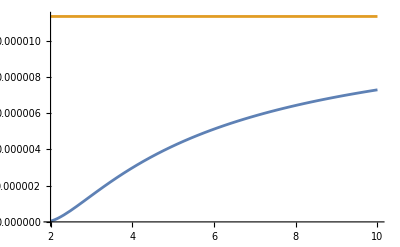

Csc[1/2 ArcCos[-1/3]]^2/(54000 √6)

```mathematica
Genhnn/.𝓂->0/.HertzRule/.Hertz†Rule/.PDNPSpinCoefFuncRules/.functionRulesNP/.sYinBLRule/.SpinCoefFuncRules//.SpinCoefFuncRules/.SpinCoefFuncRules//FullSimplify
%*Σ^2/Δ^2//FullSimplify
%%/.{𝒶->1/2,M->1,m2->1/2,bp->10,θ[]->ArcCos[-1/3]/2}//Simplify
Plot[{%,Evaluate[Limit[%,r[]->Infinity]]},{r[],2,10}]
Limit[%%,r[]->Infinity]
```

```mathematica
-(ρDyad†[]^2/2SpinRaise[#]+2τDyad[]ρDyad†[]/Sqrt[2]#)&@SpinRaise[#]&@HertzΨ[LI[ℓ],LI[𝓂]]/.HertzRule
%+Dagger[-(ρDyad†[]^2/2SpinRaise[#]+2τDyad[]ρDyad†[]/Sqrt[2]#)&@SpinRaise[#]&@HertzΨ†[LI[ℓ],LI[𝓂]]]/.Hertz†Rule//FullSimplify
%/. Λ->0(*/.𝓆->0*)/.ℓ->2//FullSimplify
%/.SpinCoefFuncRules//.SpinCoefFuncRules/.SpinCoefFuncRules//FullSimplify
%/.𝓂->0/.functionRulesBL//FullSimplify
%*Σ^2/Δ^2//FullSimplify
%%/.{𝒶->1/2,M->1,m2->1/2,bp->10,θ[]->ArcCos[-1/3]/2}//Simplify
Plot[{%,Evaluate[Limit[%,r[]->Infinity]]},{r[],2,10}]
Limit[%%,r[]->Infinity]
```

-1/2 (-1)^(2+2 𝓂) √(ℓ (1+ℓ)) √((-1+ℓ) (2+ℓ)) Gr | 𝓆
  sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   zu | ℓ | -𝓂
  |   (ρ̄)^2-(-1)^(2+2 𝓂) √2 √((-1+ℓ) (2+ℓ)) Gr | 𝓆
  sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   zu | ℓ | -𝓂
  |   ρ̄ τ

-1/2 √(-2+ℓ+ℓ^2) Gr | 𝓆
  (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   zu | ℓ | 𝓂
  |   ρ^2+zu | ℓ | -𝓂
  |   ρ̄ (√(ℓ (1+ℓ)) sY | {-4 + 𝓆, -4 + 𝓆} | ℓ | -𝓂
  |   |   ρ̄+2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | ℓ | -𝓂
  |   |   τ)-2 √2 sY | {-2 + 𝓆, -4 + 𝓆} | ℓ | 𝓂
  |   |   zu | ℓ | 𝓂
  |   ρ τ̄)

-√2 Gr | 𝓆
  (zu | 2 | -𝓂
  |   ρ̄ (√3 sY | {-4 + 𝓆, -4 + 𝓆} | 2 | -𝓂
  |   |   ρ̄+2 sY | {-4 + 𝓆, -2 + 𝓆} | 2 | -𝓂
  |   |   τ)+zu | 2 | 𝓂
  |   ρ (√3 sY | {-4 + 𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |   ρ-2 sY | {-2 + 𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |   τ̄))

1/((𝒶^2 Cos[θ]^2+r^2)^2)Gr | 𝓆
  (√6 (𝒶 Cos[θ]+ⅈ r)^2 sY | {-4 + 𝓆, -4 + 𝓆} | 2 | -𝓂
  |   |   zu | 2 | -𝓂
  |  -2 𝒶 (𝒶 Cos[θ]+ⅈ r) Sin[θ] sY | {-4 + 𝓆, -2 + 𝓆} | 2 | -𝓂
  |   |   zu | 2 | -𝓂
  |  +(𝒶 Cos[θ]-ⅈ r) (√6 (𝒶 Cos[θ]-ⅈ r) sY | {-4 + 𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |  +2 𝒶 Sin[θ] sY | {-2 + 𝓆, -4 + 𝓆} | 2 | 𝓂
  |   |  ) zu | 2 | 𝓂
  |  )

(m2 (𝒶^2 Cos[θ]^2 (3+Cos[2 θ])-(1+3 Cos[2 θ]) r^2) (𝒶^2+r (-2 M+r))^2)/(4 √6 bp^3 (𝒶^2 Cos[θ]^2+r^2)^2)

(m2 (𝒶^2 Cos[θ]^2 (3+Cos[2 θ])-(1+3 Cos[2 θ]) r^2))/(4 √6 bp^3)

(Csc[1/2 ArcCos[-1/3]]^2 (1-8 r+4 r^2)^2)/(6000 √6 (1+12 r^2)^2)

-Graphics-

Csc[1/2 ArcCos[-1/3]]^2/(54000 √6)

```mathematica
hnnFunc[mp_,sep_,rad_,th_,ph_]:=Genhnn/.functionRulesBL/.{𝒶->.5,M->1,m2->mp,bp->sep,r[]->rad,θ[]->th,ϕ[]->ph}//ToValues//Simplify
```

```mathematica
hnnFunc[1/2,10,3.31,0.11,3.99]
hnnFunc[1/2,10,2.45,0.53,2.99]
hnnFunc[1/2,10,8.18,0.75,0.24]
```

```mathematica
hnmbar[]/.hijℓ𝓂Rules/.KerrGHPDerivsOfSpinCoeffRules/.ThirdDerivsofGRules/.SecondDerivsofGRules/.DerivsofGRules/. Λ->0/.ℓ->2//Simplify
%/.SpinCoefFuncRules//.SpinCoefFuncRules/.SpinCoefFuncRules/.HertzRule//Simplify;
%/.𝓂->0/.functionRulesBL//FullSimplify
hnmbar[]/.hijℓ𝓂Rulesdag/.KerrGHPDerivsOfSpinCoeffRules/.ThirdDerivsofGRules/.SecondDerivsofGRules/.DerivsofGRules/. Λ->0/.ℓ->2//Simplify
Genhnmbar=%/.SpinCoefFuncRules//.SpinCoefFuncRules/.SpinCoefFuncRules//Simplify;
%/.𝓂->0/.functionRulesBL//FullSimplify
```

1/2 (-8 HertzΨ | 2 | 𝓂
  |   β ρ-2 (4 β-π̄+τ) (DHertzΨ | 2 | 𝓂
  |  )-DδHertzΨ | 2 | 𝓂
  |  -2 ρ (δHertzΨ | 2 | 𝓂
  |  )-ρ̄ (δHertzΨ | 2 | 𝓂
  |  )-δDHertzΨ | 2 | 𝓂
  |  )

** DefTensor: Defining tensor ChristoffelPDBLCPDNP[a,-b,-c].

$Aborted

-1/2 zu | 2 | -𝓂
  |   ((2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | 2 | -𝓂
  |   |   ρ̄-2 sY | {-4 + 𝓆, 𝓆} | 2 | -𝓂
  |   |   (π̄-τ)) (þGr | 𝓆
 )+Gr | 𝓆
  (2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | 2 | -𝓂
  |   |   ρ̄ (ρ+ρ̄)+ⅈ 𝓂 l | 3
  (-2 √2 sY | {-4 + 𝓆, -2 + 𝓆} | 2 | -𝓂
  |   |   ρ̄+sY | {-4 + 𝓆, 𝓆} | 2 | -𝓂
  |   |   (π̄-2 τ))-ⅈ 𝓂 sY | {-4 + 𝓆, 𝓆} | 2 | -𝓂
  |   |   (ðl | 3
 )))

(ⅈ m2 (-M 𝒶^2 (3+Cos[2 θ])+2 𝒶^2 Cos[θ]^2 r+2 r^3) (𝒶^2+r (-2 M+r)) Sin[2 θ])/(8 √3 bp^3 (𝒶 Cos[θ]-ⅈ r)^2 (𝒶 Cos[θ]+ⅈ r))

```mathematica
hmbarmbar[]/.hijℓ𝓂Rules/.KerrGHPDerivsOfSpinCoeffRules/.ThirdDerivsofGRules/.SecondDerivsofGRules/.DerivsofGRules/. Λ->0/.ℓ->2//Simplify;
Genhmbarmbar=%/.SpinCoefFuncRules//.SpinCoefFuncRules/.SpinCoefFuncRules//Simplify;
```

Function::fpct: Too many parameters in {a,r,M,m2,b,costheta,sintheta2,cosphi,sinphi} to be filled from Function[{a,r,M,m2,b,costheta,sintheta2,cosphi,sinphi},hnn1[a,r,M,m2,b,costheta,sintheta2,cosphi,sinphi]+hnn2[a,r,M,m2,b,costheta,sintheta2,cosphi,sinphi]][].

sY | {-4 + 𝓆, 𝓆} | 2 | -𝓂
  |   |   zu | 2 | -𝓂
  |   (2 ⅈ 𝓂 l | 3
  (þGr | 𝓆
 )+(2 (þGr | 𝓆
 ))/(-ⅈ 𝒶 Cos[θ]+r)+𝓂 Gr | 𝓆
  (𝓂 (l | 3)^2+(2 l | 3)/(𝒶 Cos[θ]+ⅈ r)+ⅈ (þl | 3
 ))-þþGr | 𝓆
 )

(m2 (-2 M 𝒶^2+2 M^2 r+(𝒶-r) r (𝒶+r)+ⅈ 𝒶 Cos[θ] (2 M^2+𝒶^2-6 M r+3 r^2)) Sin[θ]^2)/(2 √6 bp^3 (-ⅈ 𝒶 Cos[θ]+r))

{-(m2 (𝒶^2 Cos[θ]^2 (2 M^2+𝒶^2-6 M r+3 r^2)+r (2 M 𝒶^2-(2 M^2+𝒶^2) r+r^3)) Sin[θ]^2)/(2 √6 bp^3 (𝒶^2 Cos[θ]^2+r^2)),-(m2 𝒶 Cos[θ] (M-r) (𝒶^2+r (-2 M+r)) Sin[θ]^2)/(√6 bp^3 (𝒶^2 Cos[θ]^2+r^2))}

{-(√(3/2) (3-32 r^2+16 r^4) Sin[1/2 ArcCos[-1/3]]^2)/(16000 (1+12 r^2)),((-1+r) (1-8 r+4 r^2) Sin[1/2 ArcCos[-1/3]])/(4000 √3 (1+12 r^2))}

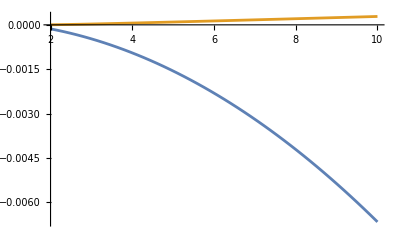

{-∞,∞}

```mathematica
Genhmbarmbar
%/.𝓂->0/.functionRulesBL//FullSimplify
ComplexExpand[{Re[%],Im[%]},TargetFunctions->{Re, Im}]//FullSimplify
%/.{𝒶->1/2,M->1,m2->1/2,bp->10,θ[]->ArcCos[-1/3]/2}//Simplify
Plot[{%(*,Evaluate[Limit[%,r->Infinity]]*)},{r[],2,10}]
Limit[%%,r[]->Infinity]
```

```mathematica
hOK/.hijℓ𝓂Rules/.KerrGHPDerivsOfSpinCoeffRules/.ThirdDerivsofGRules/.SecondDerivsofGRules/.DerivsofGRules/. Λ->0/.𝓆->0/.ℓ->2//Simplify;
%/.SpinCoefFuncRules//.SpinCoefFuncRules/.SpinCoefFuncRules//Simplify;
hOKsummed=Sum[%,{𝓂,-2,2}];
```

$Aborted

```mathematica
hOKFunc[mp_,sep_,rad_,th_,ph_]:=hOKsummed/.functionRulesOK/.{𝒶->.5,M->1,m2->mp,bp->sep,r[]->rad,θ[]->th,ψplus[]->ph}
```

```mathematica
hOKFunc[1/2,10,3.31,0.11,3.99]
hOKFunc[1/2,10,2.45,0.53,2.99]
hOKFunc[1/2,10,8.18,0.75,0.24]
```

5 hOK

5 hOK

5 hOK

```mathematica
(*Outgoing deriv*)
{{-0.000437624288109876-3.459967349522274*^-20 ⅈ,0,-0.0005287988594289661+1.1057190999986623*^-19 ⅈ,-0.00012894757920560128-2.9502374696555464*^-21 ⅈ},{0,0,0,0},{-0.0005287988594289661+1.1057190999986623*^-19 ⅈ,0,-0.017469348712908728+0. ⅈ,0.0067083542421821+0. ⅈ},{-0.00012894757920560128-2.96392357677297*^-21 ⅈ,0,0.0067083542421821+0. ⅈ,0.00021209780343586071+6.116450461644764*^-23 ⅈ}};
```

```mathematica
(*Outgoing deriv*)
{{-0.00012825341810714856+1.1125595759623007*^-20 ⅈ,0,0.0006951675114212099-9.271190117137642*^-20 ⅈ,4.067061851038465*^-6-2.73197667068678*^-20 ⅈ},{0,0,0,0},{0.0006951675114212099-9.271190117137642*^-20 ⅈ,0,-0.01104087906024391+0. ⅈ,-0.004791325564144909+0. ⅈ},{4.067061851038463*^-6-2.740501733990754*^-20 ⅈ,0,-0.004791325564144909+0. ⅈ,0.0028227055216774894-1.29953118360233*^-20 ⅈ}};
```

```mathematica
(*Outgoing deriv*)
{{-0.016802913026378978-4.477178486867554*^-19 ⅈ,0,0.0658216128746307+1.0274357614250062*^-17 ⅈ,-0.05582490928190407+3.6998864141557814*^-18 ⅈ},{0,0,0,0},{0.0658216128746307+1.0274357614250062*^-17 ⅈ,0,-2.248625120587855+0. ⅈ,0.3926418473767399+0. ⅈ},{-0.05582490928190407+3.547364277444597*^-18 ⅈ,0,0.3926418473767399+0. ⅈ,1.0716267047203776-4.468874160530462*^-18 ⅈ}};
```

```mathematica
hBL/.hijℓ𝓂Rules/.KerrGHPDerivsOfSpinCoeffRules/.ThirdDerivsofGRules/.SecondDerivsofGRules/.DerivsofGRules/. Λ->0/.𝓆->0/.ℓ->2//Simplify;
%/.SpinCoefFuncRules//.SpinCoefFuncRules/.SpinCoefFuncRules//Simplify;
hBLsummed=Sum[%,{𝓂,-2,2}];
```

```mathematica
hBLFunc[mp_,sep_,rad_,th_,ph_]:=hBLsummed/.functionRulesBL/.{𝒶->.5,M->1,m2->mp,bp->sep,r[]->rad,θ[]->th,ϕ[]->ph}//ToValues//Simplify
```

```mathematica
hBLFunc[1/2,10,3.31,0.11,3.99]
hBLFunc[1/2,10,2.45,0.53,2.99]
hBLFunc[1/2,10,8.18,0.75,0.24]
```

```mathematica
(*BL Deriv*)
{{-0.0004367311049496752-2.668153783851046*^-20 ⅈ,0.0010823615112233373+0. ⅈ,-0.0005952841103851606+0. ⅈ,-0.0001395313828895848+1.3689077181327367*^-23 ⅈ},{0.0010823615112233373+5.275565821162461*^-22 ⅈ,-0.0026790861481140365-1.8070036208091746*^-20 ⅈ,0.0006033642137969786+0. ⅈ,0.0003150113058918786+0. ⅈ},{-0.0005952841103851606+0. ⅈ,0.0006033642137969786+0. ⅈ,-0.019596363460010886+0. ⅈ,0.007807449296985651+0. ⅈ},{-0.0001395313828895848+0. ⅈ,0.0003150113058918786-7.41302594306419*^-21 ⅈ,0.007807449296985651+0. ⅈ,0.00023785855969646395+0. ⅈ}};
```

```mathematica
(*BL Deriv*)
{{-0.00012713967086234548+1.6940658945086007*^-21 ⅈ,0.0005999172969399296+0. ⅈ,0.0008201021453319569+0. ⅈ,-0.00003289470408887967+5.352542449200692*^-23 ⅈ},{0.0005999172969399296+8.095803741233667*^-22 ⅈ,-0.002341280605747396-6.324512672832112*^-20 ⅈ,-0.001597817976832705+0. ⅈ,-0.0011688017596871133+0. ⅈ},{0.0008201021453319569+0. ⅈ,-0.001597817976832705+0. ⅈ,-0.01393965870778249+0. ⅈ,-0.005933279700043656+0. ⅈ},{-0.000032894704088879634+0. ⅈ,-0.0011688017596871133-1.3096635888142579*^-20 ⅈ,-0.005933279700043656+0. ⅈ,0.00357295703458508+0. ⅈ}};
```

```mathematica
(*BL Deriv*)
{{-0.016775714448812602+5.421010862427522*^-20 ⅈ,0.02274774351991687+0. ⅈ,0.06772800444290342+0. ⅈ,-0.05788544259858659+0. ⅈ},{0.02274774351991687-1.8742149750616407*^-19 ⅈ,-0.030716533928769593-5.059610138265685*^-19 ⅈ,-0.09367844069440054+0. ⅈ,0.06536118776172048+0. ⅈ},{0.06772800444290342+0. ⅈ,-0.09367844069440054+0. ⅈ,-2.3817574584160086+0. ⅈ,0.42062857987431684+0. ⅈ},{-0.05788544259858659+0. ⅈ,0.06536118776172048+3.2704961833425434*^-17 ⅈ,0.42062857987431684+0. ⅈ,1.1344400896745686+0. ⅈ}};
```

```mathematica
hIK/.hijℓ𝓂Rules/.KerrGHPDerivsOfSpinCoeffRules/.ThirdDerivsofGRules/.SecondDerivsofGRules/.DerivsofGRules/. Λ->0/.𝓆->0/.ℓ->2//Simplify;
%/.SpinCoefFuncRules//.SpinCoefFuncRules/.SpinCoefFuncRules//Simplify;
hIKsummed=Sum[%,{𝓂,-2,2}];
```

```mathematica
hIKFunc[mp_,sep_,rad_,th_,ph_]:=hIKsummed/.functionRulesIK/.{𝒶->.5,M->1,m2->mp,bp->sep,r[]->rad,θ[]->th,ψmin[]->ph}//ToValues//Simplify
```

```mathematica
hIKFunc[1/2,10,3.31,0.11,3.99]
hIKFunc[1/2,10,2.45,0.53,2.99]
hIKFunc[1/2,10,8.18,0.75,0.24]
```

```mathematica
(*IK Deriv*)
{{-0.0004380579080136759+2.35577109810264*^-22 ⅈ,0.0021655208796830298+6.3423026501783556*^-21 ⅈ,-0.0008388014072530946+0. ⅈ,-0.00011345386033023336-2.9625674804576966*^-21 ⅈ},{0.0021655208796830298+6.3423026501783556*^-21 ⅈ,-0.010716344592456146-7.228014483236698*^-20 ⅈ,0.0026075186495494837-2.3622141171304554*^-19 ⅈ,0.0006121408758311219+0. ⅈ},{-0.0008388014072530946+0. ⅈ,0.0026075186495494837-2.3622141171304554*^-19 ⅈ,0.022070015298772658+0. ⅈ,0.006841043620938919+0. ⅈ},{-0.00011345386033023336-2.975546806485805*^-21 ⅈ,0.0006121408758311219+0. ⅈ,0.006841043620938919+0. ⅈ,-0.0002645886621558513-9.509125000796387*^-20 ⅈ}}
```

```mathematica
(*IK Deriv*){{-0.00009162724403660431-2.9826217267047485*^-21 ⅈ,0.0010562375562831426+2.803822265546597*^-20 ⅈ,0.00043964514099943653+0. ⅈ,-0.0002827626081952144+2.886039670470434*^-22 ⅈ},{0.0010562375562831426+2.803822265546597*^-20 ⅈ,-0.009365122422989584-2.529805069132845*^-19 ⅈ,-0.005054708584560369-1.0424633263678031*^-18 ⅈ,-0.0005419225642272893+0. ⅈ},{0.00043964514099943653+0. ⅈ,-0.005054708584560369-1.0424633263678031*^-18 ⅈ,-0.016415212286323387+0. ⅈ,0.0013387308724199447+6.851254334976885*^-21 ⅈ},{-0.00028276260819521445+0. ⅈ,-0.0005419225642272893+0. ⅈ,0.0013387308724199447+6.851254334976885*^-21 ⅈ,0.004268896683598563-2.338785267389849*^-19 ⅈ}}
```

```mathematica
(*IK Deriv*)
{{-0.016605950381040707-2.2951359929023675*^-19 ⅈ,0.04525962016625548-4.929191804343152*^-19 ⅈ,0.058023166159406586+0. ⅈ,-0.068706363790962-2.1812049394055573*^-18 ⅈ},{0.04525962016625548-4.929191804343152*^-19 ⅈ,-0.12286613571507837-2.023844055306274*^-18 ⅈ,-0.16697435002104016+0. ⅈ,0.16240514614346266+0. ⅈ},{0.058023166159406586+0. ⅈ,-0.16697435002104016+0. ⅈ,-2.035114315180306+0. ⅈ,0.6887475297798308+0. ⅈ},{-0.06870636379096201-2.3649095182963977*^-18 ⅈ,0.16240514614346266+0. ⅈ,0.6887475297798308+0. ⅈ,0.9783973785095667-7.939164142675694*^-17 ⅈ}}
```